## Definitions

```mathematica
NbName = "805";(*Needs["MaTeX`"];*)
(*Js={0.}; Ks={-1.}; Γs=Table[γ,{γ,0.,.0,.2}]; hV={  {0.10,0,0}  };*)
Ls =Range[20,20,2]; 	    
tV={0};	  
hV={{.001,0,0}};
steps=150;
acuracy=3;    
dmax=.5; s0=1;
ΔeV=0.1; ξs=Join[Table[ ξ, {ξ,0,.9,ΔeV} ] ,{.95}]; 
eVs=Table[ 1700Abs[ξ], {ξ,ξs} ][[1;;-3]]
(*ηs=Join[
Table[η+.02,{η,-1.5,0.5,0.1}],
Table[η+.04,{η,-1.5,0.5,0.1}],
Table[η+.06,{η,-1.5,0.5,0.1}],
Table[η+.08,{η,-1.5,0.5,0.1}],
Table[η+.08,{η,-1.5,0.5,0.1}]   ];*)
```

#### Constants

```mathematica
ReverseSort[x_]:=Reverse@Sort@x;
```

```mathematica
one[i_,j_,N_]:= SparseArray[ {i,j} -> 1, {N,N}];  block[i_,j_] := one[i,j,8];
hc=1/(√3){1,1,1};hb=1/(√2){1,-1,0};ha=1/(√6){1,1,-2};hx={1,0,0};
 hAngle[θ_,ϕ_]:= ha Cos[ϕ π/180] Sin[θ π/180]+hb Sin[ϕ π/180] Sin[θ π/180]+ hc Cos[θ π/180] ;  (* Magnetic field directions a, b, c*)
nx={1/2,(√3)/2};  ny={-1/2,(√3)/2};                                                                                           (* Honeycomb Bravais basis  *)

δx={-√3/2,-1/2}/√3;      δy={√3/2,-1/2}/√3;        δz={0,1}/√3;   

asites[m_,n_]:=m nx+n ny;
bsites[m_,n_]:=m nx+n ny-δz;
σsites[m_,n_,σ_]:=m nx+n ny-σ δz;
Gmat=  {KroneckerProduct[  PauliMatrix[0],-ⅈ PauliMatrix[2] ],KroneckerProduct[- ⅈ PauliMatrix[2],PauliMatrix[3] ],KroneckerProduct[-ⅈ PauliMatrix[2],  PauliMatrix[1] ]};
Mmat=  {KroneckerProduct[  PauliMatrix[3],ⅈ PauliMatrix[2] ],KroneckerProduct[ ⅈ PauliMatrix[2],PauliMatrix[0] ],KroneckerProduct[  PauliMatrix[1],ⅈ PauliMatrix[2] ]};
Nmat=(Mmat-Gmat)/2;
toλ[h_,Δv_:0.262]:= {h[[1]]^2,h[[2]]^2,h[[3]]^2}/Δv;
toKappa[h_,Δv_:0.262]:=8h[[1]]h[[2]]h[[3]]/(  3 Δv^2 );
KappaToH[κ_,d_,Δv_:0.262]:=Module[{C=d[[1]]d[[2]]d[[3]]},If[C==0,{0,0,0},  d CubeRoot[3  Δv^2 κ/(8C)]   ]] ;
χGx = {{0.5249,0,0,0},{0,-1,0,0},{0,0,0,0},{0,0,0,0}};χGy = {{0.5249,0,0,0},{0,0,0,0},{0,0,-1,0},{0,0,0,0}};χGz ={{0.5249,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,-1}};
ωGA = ⅈ IdentityMatrix[4]+10^-6 Sum[Mmat[[γ]],{γ,1,3}]; 
ωGB = ωGA;
Uguess=-{χGx,χGy,χGz};
Vguess={ωGA,ωGB};
to3digits[list0_]:=Module[{list=list0},If[ Length@list>=3, list, list=Flatten[{{0},list},1]; If[ Length@list>=3, list,  list=Flatten[{{0},list},1] ] ]; StringJoin[ToString/@list]     ];
round[x_,pow_:1000000]:=N[Round[pow(x)]/pow];
(* Module[{V=Table[v[[i,j]],{i,1,4},{j,1,4}]  },Table[Tr[V^ᵀ.Nmat[[γ]]],{γ,1,3}]] *)
sumtraceG[v_]:=-v⟦1,2⟧-v⟦1,3⟧-v⟦1,4⟧+v⟦2,1⟧-v⟦2,3⟧+v⟦2,4⟧+v⟦3,1⟧+v⟦3,2⟧-v⟦3,4⟧+v⟦4,1⟧-v⟦4,2⟧+v⟦4,3⟧;
traceG[v_]:={-v⟦1,2⟧+v⟦2,1⟧-v⟦3,4⟧+v⟦4,3⟧,-v⟦1,3⟧+v⟦2,4⟧+v⟦3,1⟧-v⟦4,2⟧,-v⟦1,4⟧-v⟦2,3⟧+v⟦3,2⟧+v⟦4,1⟧};
sumtraceM[v_]:=v⟦1,2⟧-v⟦2,1⟧-v⟦3,4⟧+v⟦4,3⟧+v⟦1,3⟧+v⟦2,4⟧-v⟦3,1⟧-v⟦4,2⟧+v⟦1,4⟧-v⟦2,3⟧+v⟦3,2⟧-v⟦4,1⟧;
traceM[v_]:={v⟦1,2⟧-v⟦2,1⟧-v⟦3,4⟧+v⟦4,3⟧,v⟦1,3⟧+v⟦2,4⟧-v⟦3,1⟧-v⟦4,2⟧,v⟦1,4⟧-v⟦2,3⟧+v⟦3,2⟧-v⟦4,1⟧};
sumtraceN[v_]:=v⟦1,2⟧+v⟦1,3⟧+v⟦1,4⟧-v⟦2,1⟧-v⟦3,1⟧-v⟦4,1⟧;
traceN[v_]:={v⟦1,2⟧-v⟦2,1⟧,v⟦1,3⟧-v⟦3,1⟧,v⟦1,4⟧-v⟦4,1⟧};
traceUNUN[u_]:=2{{u⟦1,2⟧ u⟦2,1⟧-u⟦1,1⟧ u⟦2,2⟧,u⟦1,3⟧ u⟦2,1⟧-u⟦1,1⟧ u⟦2,3⟧,u⟦1,4⟧ u⟦2,1⟧-u⟦1,1⟧ u⟦2,4⟧},
{u⟦1,2⟧ u⟦3,1⟧-u⟦1,1⟧ u⟦3,2⟧,u⟦1,3⟧ u⟦3,1⟧-u⟦1,1⟧ u⟦3,3⟧,u⟦1,4⟧ u⟦3,1⟧-u⟦1,1⟧ u⟦3,4⟧},{u⟦1,2⟧ u⟦4,1⟧-u⟦1,1⟧ u⟦4,2⟧,u⟦1,3⟧ u⟦4,1⟧-u⟦1,1⟧ u⟦4,3⟧,u⟦1,4⟧ u⟦4,1⟧-u⟦1,1⟧ u⟦4,4⟧}};
```

```mathematica
(*Module[{V=Table[u[[i,j]],{i,1,4},{j,1,4}]  },Table[Tr[1/2V^ᵀ.Nmat[[α]].V.Nmat[[β]]],{α,1,3},{β,1,3}]] *)
```

```mathematica
(*UpperLeft8x8[matrice_]:={
{0,0,0,0,matrice⟦1,1⟧,matrice⟦1,2⟧,matrice⟦1,3⟧,matrice⟦1,4⟧},{0,0,0,0,matrice⟦2,1⟧,matrice⟦2,2⟧,matrice⟦2,3⟧,matrice⟦2,4⟧},{0,0,0,0,matrice⟦3,1⟧,matrice⟦3,2⟧,matrice⟦3,3⟧,matrice⟦3,4⟧},{0,0,0,0,matrice⟦4,1⟧,matrice⟦4,2⟧,matrice⟦4,3⟧,matrice⟦4,4⟧},
{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0} };
UpperRight8x8[matrice_]:={
{matrice⟦1,1⟧,matrice⟦1,2⟧,matrice⟦1,3⟧,matrice⟦1,4⟧,0,0,0,0},{matrice⟦2,1⟧,matrice⟦2,2⟧,matrice⟦2,3⟧,matrice⟦2,4⟧,0,0,0,0},{matrice⟦3,1⟧,matrice⟦3,2⟧,matrice⟦3,3⟧,matrice⟦3,4⟧,0,0,0,0},{matrice⟦4,1⟧,matrice⟦4,2⟧,matrice⟦4,3⟧,matrice⟦4,4⟧,0,0,0,0},
{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}};
LowerLeft8x8[matrice_]:={
{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},
{matrice⟦1,1⟧,matrice⟦1,2⟧,matrice⟦1,3⟧,matrice⟦1,4⟧,0,0,0,0},{matrice⟦2,1⟧,matrice⟦2,2⟧,matrice⟦2,3⟧,matrice⟦2,4⟧,0,0,0,0},{matrice⟦3,1⟧,matrice⟦3,2⟧,matrice⟦3,3⟧,matrice⟦3,4⟧,0,0,0,0},{matrice⟦4,1⟧,matrice⟦4,2⟧,matrice⟦4,3⟧,matrice⟦4,4⟧,0,0,0,0}};
LowerRight8x8[matrice_]:={
{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},
{0,0,0,0,matrice⟦1,1⟧,matrice⟦1,2⟧,matrice⟦1,3⟧,matrice⟦1,4⟧},{0,0,0,0,matrice⟦2,1⟧,matrice⟦2,2⟧,matrice⟦2,3⟧,matrice⟦2,4⟧},{0,0,0,0,matrice⟦3,1⟧,matrice⟦3,2⟧,matrice⟦3,3⟧,matrice⟦3,4⟧},{0,0,0,0,matrice⟦4,1⟧,matrice⟦4,2⟧,matrice⟦4,3⟧,matrice⟦4,4⟧}};*)
```

### Pure Kitaev model definitions

#### file

```mathematica
(*dataToFilePure[ parameters_,L_,acuracy_,gauge_,data_] :=
Module[ {path,f},		createDir@FileNameJoin[  {NotebookDirectory[], "Files","pure", gauge}] ;
		path = toPathPure[parameters,L,acuracy,gauge];		
		f = OpenWrite[path];
		 Write[ f, data];
		 Close[f];                ];
(*toPathPure[κ_,L_,K_,gauge_]:=  
FileNameJoin[  {NotebookDirectory[], "Files","pure", gauge,"data", StringReplace["K=Z-L=Y-kappa=M.txt",     {"Y"-> ToString[L], "M"->  ToString@N[Round[10000κ]/10000]  , "Z"-> ToString[K]}   ] }];*)

toPathPure[parameters0_,L_,acuracy_,gauge_]:= Module[{h ,hS,parameters=parameters0, r,ϕ,θ},h=parameters[[4]] ;hS=parameters[[8]]; {r,θ,ϕ}=hS;   
parameters[[1]]=0;parameters[[3]]=0;parameters[[5]]=0;parameters[[7]]=0;
FileNameJoin[{       NotebookDirectory[]   , "Files" ,"pure",gauge,StringReplace["t=X1_eV=X2_JKG=X3_JKGmod=X4",{"X1"->  ToString[parameters[[9]]],"X2"->  ToString[parameters[[10]]],"X3"->  ToString[parameters[[1;;3]]  ],"X4"->  ToString[parameters[[5;;7]]]   }] , "data"  , 
StringReplace["h=(M,N,T)_L=Y_A=Z.txt",{"Y"-> ToString[L], "Z"-> ToString[acuracy],"M"->  ToString[r,InputForm] ,"N"->ToString@ϕ,"T"->ToString@θ}   ] 
   }]];

loadDataPure[ path_]:= Module[{(*path,*)f,data}, 
(*path= toPathPure[κ,L,K,gauge];*)
f = OpenRead[path];
data=ReadList[ f];
Close[f];
data[[-1]]  ];*)
```

```mathematica
dataToFilePure[ parameters0_,L_,acuracy_,gauge_,data_] :=
Module[ {path,parameters=parameters0,f},		
(*createDir@FileNameJoin[{NotebookDirectory[],"Files","pure", gauge}] ;*)
parameters[[1]]=0;parameters[[3]]=0;parameters[[5]]=0;parameters[[7]]=0;
createDir@FileNameJoin[{NotebookDirectory[],"Files","pure",gauge, StringReplace["t=X1_eV=X2_JKG=X3_JKGmod=X4",
{"X1"->  ToString[parameters[[9]]],"X2"->  ToString[parameters[[10]]],"X3"->  ToString[parameters[[1;;3]]  ],"X4"->  ToString[parameters[[5;;7]]]   }]
           }] ;
		path = toPathPure[parameters,L,acuracy,gauge];		
		Print["Pure path=",path];Print[];
		f = OpenWrite[path];
		 Write[ f, data];
		 Close[f];                ];

toPathPure[parameters0_,L_,acuracy_,gauge_]:= Module[{h ,hS,parameters=parameters0, r,ϕ,θ},h=parameters[[4]] ;hS=parameters[[8]]; {r,θ,ϕ}=hS;   
parameters[[1]]=0;parameters[[3]]=0;parameters[[5]]=0;parameters[[7]]=0;
FileNameJoin[{NotebookDirectory[], "Files" ,"pure",gauge,StringReplace["t=X1_eV=X2_JKG=X3_JKGmod=X4",
{"X1"->  ToString[parameters[[9]]],"X2"->  ToString[parameters[[10]]],"X3"->  ToString[parameters[[1;;3]]  ],
"X4"->  ToString[parameters[[5;;7]]]   }] , "data"  , 
StringReplace["h=(M,N,T)_L=Y_A=Z.txt",{"Y"-> ToString[L], "Z"-> ToString[acuracy],"M"->  ToString[r,InputForm] ,"N"->ToString@ϕ,"T"->ToString@θ}   ] 
   }]];

loadDataPure[path_]:=Module[ {f,data},
f = OpenRead[path];
If[f==$Failed, Print["Failed to OpenRead file at: "]; Print[ path ]; Abort[] ];
data=ReadList[f];
Close[f];			
data[[-1]]
];
createDir[path_] :=
Module[ {l=Length@FileNames[path]},		
	If[ l==0,  CreateDirectory@File@FileNameJoin[{path,"data" }]; CreateDirectory@File@FileNameJoin[{path ,"graph" }]; 
,Null]  ];
```

#### Auxiliary matrices for the Hamiltonian [2x2 matrices]

we define Z2 gauge field u[r] for each unit cell r as a three component vector which each component correspond α to the gauge field in the α bond for the A site in the unit cell r.

```mathematica
toR[m0_,n0_,L_,M_]:= Module[{Δn=⌊n0/L⌋,n,m},n=Mod[n0 ,L]; m=Mod[m0+M Δn,L]; m + n L+1];
```

```mathematica
HNN[K_,κ_,λ_,u_,m_,n_,L_,M_]:=Module[{r=toR[m,n ,L,M]},Table[{{0,(-K⟦r,α⟧+λ[[α]]) u⟦r,α⟧ },{0,0}},{α,1,3}]]; 
HNNNA[K_,κ_,λ_,u_,m_,n_,L_,M_]:=Module[{
r1={toR[m,n ,L,M],toR[m,n ,L,M],toR[m,n,L,M]},
r2={toR[m+1,n-1 ,L,M],toR[m,n+1 ,L,M],toR[m-1,n,L,M]}        }      ,
Table[{{κ u[[r1[[α]],α]] u[[r2[[α]],Mod[α+1,3,1] ]],0},{0,0 }},{α,1,3}]
];
HNNNB[K_,κ_,λ_,u_,m_,n_,L_,M_]:=Module[{
r1={toR[m-1,n ,L,M],toR[m,n -1,L,M],toR[m,n,L,M]},
r2={toR[m-1,n ,L,M],toR[m,n-1 ,L,M],toR[m,n,L,M]}        }      ,
Table[{{0,0},{0,κ u[[r1[[α]],α]] u[[r2[[α]],Mod[α+1,3,1] ]]}},{α,1,3}]
];
					
Hreal[K_,κ_,λ_,u_,L_,M_,δk_] := Module[{Nc=L^2,H },

 H= ⅈ Sum[Module[{Hnn,HnnnA,HnnnB, φ=δk.(m nx+n ny),
r={toR[m+1,n ,L,M],toR[m,n+1 ,L,M],toR[m,n ,L,M]},
RA={toR[m+1,n-1 ,L,M],toR[m,n+1 ,L,M],toR[m-1,n,L,M]},
RB={toR[m-1,n+1 ,L,M],toR[m,n-1 ,L,M],toR[m+1,n,L,M]}    },

Hnn=HNN[K,κ,λ,u,m,n,L,M] ;HnnnA=HNNNA[K,κ,λ,u,m,n,L,M] ;HnnnB=HNNNB[K,κ,λ,u,m,n,L,M] ;

Sum[       KroneckerProduct[ one[r[[3]],r[[α]],Nc],Hnn[[α]]]   +
KroneckerProduct[ one[r[[3]],RA[[α]],Nc],HnnnA[[α]]]   +
KroneckerProduct[ one[r[[3]],RB[[α]],Nc],HnnnB[[α]]]   ,{α,1,3}] Exp[ⅈ φ]      ] 
,{m,0,L-1},{n,0,L-1}];

 H+H†];

TmatPure[L_] :=KroneckerProduct[   IdentityMatrix[L^2],  {{1,1},{ⅈ,-ⅈ}} ];
UmatPure[H_]:= Module[ {R=Quiet@Eigensystem@N[H]},ReverseSort[Rᵀ]ᵀ⟦2⟧ᵀ ];
EandUPure[H_]:= Module[ {R=Transpose@ReverseSort@Transpose@Quiet@Eigensystem@N[H]},{R[[1]],R⟦2⟧ᵀ }];
𝕌occupiedPure[TU_,Nc_]:= Drop[Take[TUᵀ,-Nc-1],{2}]ᵀ;


correlations[U_,u_,L_,M_] :=Module[  { Nc=L^2,𝕌,𝕌h,icc,SS },
𝕌=TmatPure[L].U;𝕌h=𝕌[[;;,-Nc;;-1]];icc=Chop[ⅈ  𝕌h.𝕌h† ];

SS[[3]]=ArrayFlatten[ # ,1]& @ Table[ 
Module[{ rz,Io,J},rz=m+(n-1)L-1; Io=Mod[α+2rz,2 L^2,1];J=Mod[β + 4 +2rz,2 L^2,1];
-u[[m,n]] icc[[J,Io]]    ], {m,1,L},{n,1,L},  {α,1,4},{β,1,4} ];

SS[[1]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,rx,mx,Io,J},mx=Mod[m+1,L,1]; rz=m+(n-1)L-1;rx=mx+(n-1)L-1;Io=Mod[α+2rz,2 L^2,1];J=Mod[β + 4+2rx,2 L^2,1];
icc[[J,Io]]      ]   , {m,1,L},{n,1,L},  {α,1,4},{β,1,4} ];
SS[[2]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,ry,my,ny,Io,J}, 
ny=Mod[n+1,L,1];my=If[ny==1,Mod[m-M,L,1] , m];  ry=my+(ny-1)L-1;rz=m+(n-1)L-1;Io=Mod[α+2rz,2 L^2,1];J=Mod[β + 4+2ry,2 L^2,1];
icc[[J,Io]]    ]    , {m,1,L},{n,1,L},  {α,1,4},{β,1,4} ];
SS
];
```

#### to MF pure + gauge

```mathematica
χgauge4v[χ0_,L_]:= Module[{d1,d2,χ=χ0,mS,nS,mN,nN,r2 },   r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;d1=L-d2;  mS=r2-1;nS=r2-1;mN=L-r2-1;nN=L-r2-1;
Do[  Module[{r,m,n}, m =mS ; n=nS+i ;       r = m+n L+1;    χ[[1,r]][[2,2]] =-χ0[[1,r]][[2,2]];      ]   , {i,1,d1}];   
Do[  Module[{r,m,n}, m =mN ; n=nN-i+1; r = m+n L+1;    χ[[1,r]][[2,2]] =-χ0[[1,r]][[2,2]];       ]   , {i,1,d1}];       χ ];
```

```mathematica
toMFparametersPure[U_,u_,L_,M_] :=Module[  { Nc=L^2,𝕌,𝕌h,icc,SS=Array[Null,3]  },
𝕌=TmatPure[L].U;𝕌h=𝕌[[;;,-Nc;;-1]];icc=Chop[ⅈ  𝕌h.𝕌h† ];

SS[[3]]=ArrayFlatten[ # ,1]& @ Table[ 
Module[{ rz,Io,J},rz=m+n L; Io=Mod[1+2rz,2 L^2,1];J=Mod[1 + 1 +2rz,2 L^2,1];
 {{   -u[[rz+1,3]]  1/2(icc[[J,Io]]-icc[[Io,J]] ),0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,-1 }}    ],{n,0,L-1} , {m,0,L-1}];

SS[[1]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,rx,mx,Io,J},mx=Mod[m+1,L]; rz=m+n L;rx= mx+n L ;Io=Mod[1+2rz,2 L^2,1];J=Mod[1 + 1+2rx,2 L^2,1];
 {{ -u[[ rz+1 ,1]]  1/2(icc[[J,Io]]-icc[[Io,J]] ) ,0,0,0},{0,-1 ,0,0},{0,0,0,0},{0,0,0,0}}     ] ,{n,0,L-1} , {m,0,L-1}];
SS[[2]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,ry,my,ny,Io,J}, ny=Mod[n+1,L];my=If[ny==0,Mod[m-M,L] , m];  ry= my+ny L;
rz=m+n L;Io=Mod[1+2rz,2 L^2,1];J=Mod[1+ 1+2ry,2 L^2,1];
 {{   -u[[rz+1,2]]  1/2(icc[[J,Io]]-icc[[Io,J]] ),0,0,0},{0,0,0,0},{0,0,-1 ,0},{0,0,0,0}}        ],{n,0,L-1} , {m,0,L-1}];
SS        ];
```

```mathematica
toMFparametersPure[U_,u_,L_,M_] :=Module[  { Nc=L^2,𝕌,𝕌h,icc,SS=Array[Null,3]  },
𝕌=TmatPure[L].U;𝕌h=𝕌[[;;,-Nc;;-1]];icc=Chop[ⅈ  𝕌h.𝕌h† ];

SS[[3]]=ArrayFlatten[ # ,1]& @ Table[ 
Module[{ rz,Io,J},rz=m+n L; Io=Mod[1+2rz,2 L^2,1];J=Mod[1 + 1 +2rz,2 L^2,1];
 {{     1/2(icc[[J,Io]]-icc[[Io,J]] ),0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,u[[rz+1,3]] }}    ],{n,0,L-1} , {m,0,L-1}];

SS[[1]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,rx,mx,Io,J},mx=Mod[m+1,L]; rz=m+n L;rx= mx+n L ;Io=Mod[1+2rz,2 L^2,1];J=Mod[1 + 1+2rx,2 L^2,1];
 {{  1/2(icc[[J,Io]]-icc[[Io,J]] ) ,0,0,0},{0,u[[ rz+1 ,1]]  ,0,0},{0,0,0,0},{0,0,0,0}}     ] ,{n,0,L-1} , {m,0,L-1}];
SS[[2]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,ry,my,ny,Io,J}, ny=Mod[n+1,L];my=If[ny==0,Mod[m-M,L] , m];  ry= my+ny L;
rz=m+n L;Io=Mod[1+2rz,2 L^2,1];J=Mod[1+ 1+2ry,2 L^2,1];
 {{     1/2(icc[[J,Io]]-icc[[Io,J]] ),0,0,0},{0,0,0,0},{0,0,u[[rz+1,2]] ,0},{0,0,0,0}}        ],{n,0,L-1} , {m,0,L-1}];
SS        ];
```

```mathematica
gaugeConfigUPure[σ_,L1_,L2_]:=Module[{bonds,linethick=.012 (Log[49]/Log[L1 L2]),lattice,size}, size = 0.01 (Log[49]/Log[L1 L2])^2 ;
lattice=Flatten[Table[{  {Black,PointSize[4 size],Point[asites[m,n]]},{Black,PointSize[4 size],Point[bsites[m,n]]}  , {Gray,PointSize[2  size ],Point[asites[m,n]]},{White,PointSize[2  size],Point[bsites[m,n]]}     },{m,0,L1-1},{n,0,L2-1} ], 2    ];
bonds=Flatten[Table[
{    
{ If[σ[[m+n L1+1,3]]>= 0, Cyan ,Darker@Blue],Thickness[linethick],Line[{asites[m,n],bsites[m,n]}]},                   (*z-bonds*)
{If[σ[[m+n L1+1,1]]>= 0, Magenta ,Darker@Red],Thickness[linethick],Line[{asites[m,n],bsites[m+1,n]}]},             (*x-bonds*)
{If[σ[[m+n L1+1,2]]>= 0, Darker@Yellow ,Darker@Green],Thickness[linethick],Line[{asites[m,n],bsites[m,n+1]}]}              (*y-bonds*)
},{m,0,L1-1},{n,0,L2-1} ], 2    ];
Graphics[{bonds,lattice},ImageSize->300]            ];  

uniformU[u_,L1_,L2_]:=Table[   {u,u,u}     ,L1 L2];
flipUoneZbond[u0_,L1_,L2_]:= Module[{R1,u=u0,m0=⌈L1/2⌉ -1,n0=⌈(L2+1)/2⌉-1 }, R1= { m0,n0};
  Module[{r,m,n}, m =Mod[R1[[1]],L1] ; n=Mod[R1[[2]],L2] ; r = m+n L1+1;    u[[r, 3 ]] =-u0[[r,3 ]];      ]   ;  u           ];
flipUZMaxSpaced[u0_,L1_,L2_]:= Module[{R1,d,u=u0,m0=⌈L1/2⌉ -1,n0=⌈(L2+1)/2⌉-1 }, d=⌊(L1-1)/2⌋; R1= { m0,n0};
Do[  Module[{r,m,n}, m =Mod[R1[[1]]+i,L1] ; n=Mod[R1[[2]]-i,L2] ; r = m+n L1+1;    u[[r, 3 ]] =-u0[[r,3 ]];      ]   , {i,0,d-1}];  u           ];
```

consider other gauge configurations:

```mathematica
uniformU[u_,L_]:=Table[ {u,u,u},{i,1,L^2} ];
gauge4v[u0_,L_]:= Module[{d1,d2,u=u0,mS,nS,mN,nN,r2 },   r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;d1=L-d2;  
mS=r2-1;nS=r2-1;mN=L-r2-1;nN=L-r2-1;
Do[  Module[{r,m,n}, m =mS ; n=nS+i ;       r = m+n L+1;    u[[r,1]] =-u0[[r,1]];      ]   , {i,1,d1}];   
Do[  Module[{r,m,n}, m =mN ; n=nN-i+1; r = m+n L+1;    u[[r,1]] =-u0[[r,1]];      ]   , {i,1,d1}];               u           ];
```

```mathematica
positionVortex[v_,L_]:=Module[{d1,d2,r2,mS,nS,mW,nW,mE,nE,mN,nN},
		 r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;d1=L-d2; 

		 mS=r2-1;           nS=r2-1;
		 mW=r2-1;           nW=L-r2-1;
		 mE=L-r2-1;     nE=r2-1;
		 mN=L-r2-1;     nN=L-r2-1;

		{{mS,nS},{mW,nW},{mE,nE},{mN,nN}}[[v]]
]
```

v=1  South, v=2 West, v=3 East, v=4 North

```mathematica
gauge2v[u0_,L_,α_]:= Module[{d1,d2,u=u0,m0,n0,r2 ,v},   r2= ⌊1/2 ⌈L/2⌉⌋;   Do[  Module[{r,m,n},
							m={r2-1,             r2-1+i,              r2-1+i   }⟦α⟧; 
							n={r2-1+i,       L-r2-1,             L-r2-i   }⟦α⟧;
 r = m+n L+1;    u[[r,α]] =-u0[[r,α]];      ]   , {i,1,d1}];                u           ];
```

```mathematica
gaugeConfig[χ_,L1_,L2_]:=Module[{bonds,linethick=.012 (Log[49]/Log[L1 L2]),lattice,size}, size = 0.01 (Log[49]/Log[L1 L2])^2 ;
lattice=Flatten[Table[{  {Black,PointSize[4 size],Point[asites[m,n]]},{Black,PointSize[4 size],Point[bsites[m,n]]}  , {Gray,PointSize[2  size ],Point[asites[m,n]]},{White,PointSize[2  size],Point[bsites[m,n]]}     },{m,0,L1-1},{n,0,L2-1} ], 2    ];
bonds=Flatten[Table[
{    
{ If[χ[[3,m+n L1+1]][[4,4]]>= 0, Darker@Yellow ,Darker@Blue],If[χ[[3,m+n L1+1]][[4,4]]>= 0,  Thickness[1.5linethick] ,Thickness[linethick] ] ,Line[{asites[m,n],bsites[m,n]}]},                   (*z-bonds*)
{If[χ[[1,m+n L1+1]][[2,2]]>= 0, Cyan,Darker@Red],If[χ[[1,m+n L1+1]][[2,2]]>= 0,Thickness[1.5 linethick] ,Thickness[linethick] ],Line[{asites[m,n],bsites[m+1,n]}]},             (*x-bonds*)
{If[χ[[2,m+n L1+1]][[3,3]]>= 0, Magenta ,Darker@Green],If[χ[[2,m+n L1+1]][[3,3]]>= 0, Thickness[1.5linethick] ,Thickness[linethick] ],Line[{asites[m,n],bsites[m,n+1]}]}              (*y-bonds*)
},{m,0,L1-1},{n,0,L2-1} ], 2    ];
Graphics[{bonds,lattice},ImageSize->300]             ];
```

#### electric field

```mathematica
uniform[K_,L1_,L2_]:=Table[   {K,K,K}     ,{i,1,L1 L2} ];  

addVortex[ Ko_,K0_, R_,L1_,L2_]:= Module[ {m=R[[1]],n=R[[2]],K=Ko,r=Table[0,6]},
K[[ m+n L1 +1,3    ]]=K0;  
K[[ Mod[m+1,L1]+Mod[n-1,L2] L1 +1  ,2    ]]=K0;
K[[ Mod[m+1,L1]+n L1 +1,1    ]]=K0;
K[[ Mod[m+1,L1]+Mod[n+1,L2] L1 +1  ,3   ]]=K0;
K[[ m+Mod[n+1,L2] L1+1   ,2    ]]=K0;
K[[ Mod[m-1,L1]+Mod[n+1,L2] L1 +1  ,1   ]]=K0;
K];

add2Vortices[ Ko_,K1_,K2_, R1_,R2_,L1_,L2_] :=Module[ {K}, K = addVortex[ Ko,K1, R1,L1,L2]; addVortex[ K,K2, R2,L1,L2]];
add4Vortices[ K0_,Kmod_, R1_,R2_, R3_,R4_,L_] :=Module[ {K}, K = addVortex[ K0,Kmod, R1,L,L]; K = addVortex[ K,Kmod, R2,L,L]; K = addVortex[ K,Kmod, R3,L,L]; addVortex[ K,Kmod, R4,L,L]];
add2VorticesMaxSpaced[ Ko_,K1_,K2_,L1_,L2_] := Module[{R1,R2,d}, d=⌊(L1-1)/2⌋; R1= {⌊L1/2⌋ ,⌊(L2+1)/2⌋ };R2= {⌊L1/2⌋   +d,⌊(L2+1)/2⌋ -d};
	add2Vortices[ Ko,K1,K2, R1,R2,L1,L2]];
add4VorticesMaxSpaced[ K0_,Kmod_,L_] :=Module[ {RS,RE,RW,RN,r2},   r2= ⌊1/2 ⌈L/2⌉⌋;
		RS={(r2-1),(r2-1)};
		RW={(r2-1),(L-r2-1)};
		RE={(L-r2-1),(r2-1)};
		RN={(L-r2-1),(L-r2-1)};
add4Vortices[ K0,Kmod, RS,RW, RE,RN,L] ];
```

### Momentum

#### consts

```mathematica
mx= 2π {1 , 1/Sqrt[3]}; my= 2π {-1 , 1/Sqrt[3]};
(*toMomentum[n_,Nb_]:= If[FractionalPart[Sqrt@Nb] ≠ 0, Print["Nb=",Nb,", is not a perfect square."];Abort[],
				Module[ {L = IntegerPart[Sqrt@Nb],p1,p2},  p1 =  Mod[n-1,L]+1; p2 =   (n-p1)/L+1;   mxp1/L +myp2/L]      ];*)
toMomentum[n_,Nb_]:= Module[ {L = IntegerPart[Sqrt@Nb],p1,p2},  p1 =  Mod[n,L,1]; p2 =   (n-p1)/L+1;   mx p1/L +my p2/L];
toMomentumTable[L_]:=Table[Module[{p1,p2},p1=Mod[n,L,1];p2=(n-p1)/L+1;{(2(p1-p2)π)/L,(2 (p1+p2) π)/(Sqrt[3] L)}],{n,1,L^2}];
toMomentumTable[L_]:=Table[Module[{m,n},m=Mod[r-1,L];n=⌊(r-1)/L⌋;{(2π(m-n))/L,(2π (m+n))/(Sqrt[3] L)}],{r,1,L^2}];
toMomentumInverse[k_,Nb_]:= If[FractionalPart[Sqrt@Nb] != 0, Print["Nb=",Nb,", is not a perfect square."];Abort[],    
Module[ {M = IntegerPart[Sqrt@Nb],p1,p2},   p1=k . nx M/(2π); p2=k . ny M/(2π);  Round[p1 + (p2-1)M ]  ]];
kD2=1/3 mx+2/3 my;
kD1=2/3 mx+1/3 my;
Γpoint={0,0};
Kpoint=2/3 mx+1/3 my;
KPpoint=1/3 mx+2/3 my;
Mpoint=1/2 (Kpoint+KPpoint);
MPpoint=1/2 (Kpoint-mx+KPpoint);
MPPpoint=1/2 (Kpoint+KPpoint-my);
```

```mathematica
toLineΓKKΓ0[M_]:=Module[ {ki=my,kf=mx},  Table[ ki+t(kf-ki),{t,0,1,1/M}]    ] ;
toLineΓKMΓ[M_]:=Module[ {ks,Ne,Δt},(* 1: Γ=0, 2: K=(1/3,2/3), 3: K'=(2/3,3/3), 4: Γ=0,  *)
ks={ Γpoint,Kpoint,MPpoint,Γpoint }; 
Ne=Length[ks]-1; (* number of edges making the path in the BZ*) 
Flatten[ Table[ Table[ ks[[i]]+t(  ks[[i+1]]-ks[[i]]  ),{t,0,1-Ne/M(1-KroneckerDelta[i,Ne]),Ne/M}],{i,1,Ne}],1]       ] ;
```

```mathematica
toLineΓKMΓ[M_]:=Module[ {ks,Ne,Δt},(* 1: Γ=0, 2: K=(1/3,2/3), 3: K'=(2/3,3/3), 4: Γ=0,  *)
ks={ Γpoint,Kpoint,MPpoint,Γpoint }; 
Ne=Length[ks]-1; (* number of edges making the path in the BZ*) 
Flatten[ Table[ Table[ ks[[i]]+t(  ks[[i+1]]-ks[[i]]  ),{t,Ne/M(1-KroneckerDelta[i,1]),1,Ne/M}],{i,1,Ne}],1]      ] ;
```

```mathematica
toLineΓKMΓKMM[M_]:=Module[ {ks,Ne,Δt},(* 1: Γ=0, 2: K=(1/3,2/3), 3: K'=(2/3,3/3), 4: Γ=0,  *)
ks={ Γpoint,KPpoint,MPpoint,Γpoint,Kpoint,Mpoint,MPPpoint }; 
Ne=Length[ks]-1; (* number of edges making the path in the BZ*) 
Flatten[ Table[ Table[ ks[[i]]+t(  ks[[i+1]]-ks[[i]]  ),{t,Ne/M(1-KroneckerDelta[i,1]),1,Ne/M}],{i,1,Ne}],1]
    ] ;
```

#### ham

```mathematica
(*Tmom[k_]:=Module[{kx=k.mx,ky=k.my},{{1,0,0,0,1,0,0,0},{0,1,0,0,0,1,0,0},{0,0,1,0,0,0,1,0},{0,0,0,1,0,0,0,1},{ⅈ,0,0,0,-ⅈ,0,0,0},{0,ⅈ ⅇ^(ⅈ kx),0,0,0,-ⅈ ⅇ^(ⅈ kx),0,0},{0,0,ⅈ ⅇ^(ⅈ ky),0,0,0,-ⅈ ⅇ^(ⅈ ky),0},{0,0,0,ⅈ,0,0,0,-ⅈ}}];*)
Tkmom=KroneckerProduct[ {{1,1},{I,-I}}, SparseArray[{Band[{1,1}]-> {1,1,1,1}},{4,4}] ]; 
AMFmom[Jm_,U_]:=Module[{AMF,N=Nmat},  AMF=Table[    Sum[   2 Jm[[γ]][[α,β]] N[[α]].U[[γ]].N[[β]] ,{α,1,3},{β,1,3}]    ,{γ,1,3}];   KroneckerProduct[ {{0,1},{0,0}},#]&/@Re@AMF];
BMFmom[Jm_,h_,λ_,V_]:=Module[{Ba,Bb,M=Mmat,N=Nmat,G=Gmat},
Ba=Sum[    Sum[    Jm[[γ]][[α,β]] N[[α]] traceN[ V[[2]] ][[β]] ,{α,1,3},{β,1,3}] -2 h[[γ]] N[[γ]] + λ[[1]][[γ]] G[[γ]]        ,{γ,1,3}];
Bb=Sum[    Sum[    Jm[[γ]][[α,β]] N[[α]] traceN[ V[[1]] ][[β]] ,{α,1,3},{β,1,3}] -2 h[[γ]] N[[γ]] + λ[[2]][[γ]] G[[γ]]         ,{γ,1,3}];
{KroneckerProduct[ {{1,0},{0,0}},Re@Ba],KroneckerProduct[ {{0,0},{0,1}},Re@Bb] }];

cMFmom[Jm_,U_,V_]:=Module[{N=Nmat}, Sum[ 1/8  Jm[[γ]][[α,β]] (traceN[ V[[1]] ][[α]]  traceN[ V[[2]] ][[β]] +2  Tr[ U[[γ]]ᵀ.N[[α]].U[[γ]].N[[β]] ]   ),{α,1,3},{β,1,3},{γ,1,3}]          ];
enMFmom[Jm_,U_,V_,h_,η_:0]   :=Module[{M=Mmat,N=Nmat,G=Gmat,λ},λ=η {h,h}+ λeffmom[Jm,h,V];  cMFmom[Jm,U,V]+1/4  Sum[-2h[[γ]] traceN[ V[[σ]] ][[γ]] + λ[[σ,γ]] traceG[ V[[σ]] ][[γ]]
,{σ,1,2},{γ,1,3}]        ];
enSUMmom[Jm_,U_,V_,h_,L_:30,η_:0]:=Module[{λ,mT=toMomentumTable[L]},(*λ=η {h,h}+ λeffmom[Jm,h,V];*)-cMFmom[Jm,U,V]+1/(2 L^2)Sum[Total@Select[Eigenvalues@N@HmfMomentum[Jm,h,U,V,mT[[i]],η  ] ,#<=0& ] , {i,1,L^2}] ];

HmfMomentum[Jmatrice_,h_,U_,V_, k_,η_:0] := Module[{Ax,Ay,Az,BA,BB, hx,hy,hz, kx,ky,ha,HA,HB,λ}, kx=k . nx;ky=k . ny;
λ=η {h,h}+ λeffmom[Jmatrice,h,V];
{Ax,Ay,Az}=ⅈ AMFmom[Jmatrice,U];  ha= Exp[ ⅈ kx]  Ax + Exp[ ⅈ ky] Ay + Az;   
 (*ha=Exp[-I k.δx] Ax + Exp[-I k.δy] Ay +Exp[-I k.δz] Az;*)   HA=N@( ha+ConjugateTranspose@ha );
{BA,BB}= ⅈ BMFmom[Jmatrice,h,λ,V];   HB=BA+BB ; (*  HB=N[   ( HB+ConjugateTranspose@HB )/2 ];*)
1/2(HA+HB)   ];
UmatK[H_]:= Module[ {R=Eigensystem@N[H]},ReverseSort[ Rᵀ ]ᵀ[[ 2 ]]ᵀ ];
λeffmom[Jmat_,h_,V_]:=Module[{M},M=Table[1/2 traceN[V[[σ]] ],{σ,1,2} ];  Table[- h+1/2 Sum[ Jmat[[γ]].M⟦  Mod[σ+1,2,1]  ⟧  ,{γ,1,3}],    {σ,1,2}]     ];
HmfMomentumVec[Jmatrice_,h_,U_,V_, kTable_,η_:0] :=Table[HmfMomentum[Jmatrice,h,U,V, kTable[[l]],η],{l,1,Length@kTable}];
UmatVec[Jmatrice_,h_,U_,V_, kTable_,Tk_,η_:0] :=UmatK/@Table[ Tk† .HmfMomentum[Jmatrice,h,U,V, kTable[[l]],η].Tk,{l,1,Length@kTable}];
```

```mathematica
(*(FullSimplify@λeffmom[Jmat[{0,0,0},K{1,1,1}],{h1,h2,h3},Table[Sum[ v[γ]Mmat[[γ]]+vbar[γ] Gmat[[γ]],{γ,1,3}] ,{σ,1,2}  ]          ] )[[1]]
FullSimplify@(λeffmom[Jmat[{0,0,0},K{1,1,1}],{h1,h2,h3},Table[Sum[ hc[[γ]] Mmat[[γ]],{γ,1,3}] ,{σ,1,2}  ]          ] [[1]]) *)
```

### MF model definitions

#### Saving and Loading data

To create a given NotebookDirectory  “path” if it does not exist:

```mathematica
(*
FullSimplify@fromJmat[Jmat[J{1,1,1},K{1,1,1},Γ{1,1,1},Γp {1,1,1},DM {1,1,1} ] ]
Jm=Jmat[J{1,1,1},K{1,1,1},Γ{1,1,1},Γp {1,1,1},DM {1,1,1} ] ; MatrixForm/@jm
((    cyclicPermutation[Jm[[1]] ,2] + cyclicPermutation[Jm[[2]] ,1] + Jm[[3]] )/3)
MatrixForm@(    cyclicPermutation[jm[[1]] ,2] + cyclicPermutation[jm[[2]] ,1] + jm[[3]] )
*)
```

```mathematica
cyclicPermutation[A_,s_:1]:= If[ Length[A]==3 ∧ Length[A[[1]]]==3, Table[ A[[Mod[i-s,3,1],Mod[j-s,3,1]]],{i,1,3},{j,1,3}]  ];
```

```mathematica
fromJmat[Jm_]:= Module[{J,K,Γ,Γp,DM,jm}, jm=(  cyclicPermutation[Jm[[1]] ,2] + cyclicPermutation[Jm[[2]] ,1] + Jm[[3]] )/3; 
Γp=(jm[[1,3]]+jm[[2,3]]+jm[[3,1]]+jm[[3,2]])/4; 
K=( jm[[3,3]]-(jm[[2,2]] +jm[[1,1]] )/2); J=(jm[[3,3]]-K);DM=(jm[[1,2]]-jm[[2,1]])/2;Γ=(jm[[1,2]]+jm[[2,1]])/2;
Chop[N@{J,K,Γ,Γp,DM},.00000999]    ];
```

```mathematica
createDir[path_] :=
Module[ {l=Length@FileNames[path]},		
	If[ l==0,  CreateDirectory@File@FileNameJoin[{path,"data" }]; CreateDirectory@File@FileNameJoin[{path ,"graph" }]; 
,Null]  ];
```

to read the data at “pathData” :

```mathematica
loadData[pathData_]:=
Module[ {f,data},
		        f = OpenRead[pathData];
If[f==$Failed, Print["Failed to OpenRead file at: "]; Print[ pathData ]; Abort[] ];
		        data=ReadList[f];
		        Close[f];			data[[-1]]
];
```

```mathematica
loadDataALL[pathData_]:=
Module[ {f,data},
		        f = OpenRead[pathData];
If[f==$Failed, Print["Failed to OpenRead file at: "]; Print[ pathData ]; Abort[] ];
		        data=ReadList[f];
		        Close[f];			data
];
```

```mathematica
(*toPath800 [parameters0_,L_,acuracy_,gauge_,NbName_]:= Module[{h ,hS,parameters=parameters0, filename,r,ϕ,θ,},h=parameters[[2]] ;hS=parameters[[4]]; {r,θ,ϕ}=hS;   
If[gauge=="free",parameters[[3]]=parameters0[[1]];parameters[[6]]=0;];
filename="t=X1_eV=X2_JKG=X3_JKGmod=X4";
If[gauge=="free_lambda",parameters[[3]]=parameters0[[1]];filename="lambda_X2_JKG=X3"; ];
FileNameJoin[{       NotebookDirectory[]   , "Files" ,NbName,gauge,StringReplace[filename,{"X1"->  ToString[parameters[[5]]],"X2"->  ToString[parameters[[6]]],
"X3"->  ToString[NumberForm[#,{4,4}]&/@fromJmat@parameters[[1]]  ],
"X4"->  ToString[NumberForm[#,{4,4}]&/@fromJmat@parameters[[3]]]   }] , "data"  , 
StringReplace["h=(M,N,T)_L=Y_A=Z.txt",{"Y"-> ToString[L], "Z"-> ToString[acuracy],"M"->  ToString[r,InputForm] ,"N"->ToString@θ,"T"->ToString@ϕ}   ] 
   }]];
dataToFile800[ parameters0_,L_,acuracy_,data_,gauge_,NbName_] :=
Module[ {path,f,filename,parameters=parameters0}, 
If[gauge=="free",parameters[[3]]=parameters0[[1]];parameters[[6]]=0;];
filename="t=X1_eV=X2_JKG=X3_JKGmod=X4";
If[gauge=="free_lambda",parameters[[3]]=parameters0[[1]];filename="lambda_X2_JKG=X3"; ];
		createDir@FileNameJoin[{ NotebookDirectory[] ,"Files",  NbName,gauge, StringReplace[filename,
{"X1"->  ToString[parameters[[5]]],"X2"->  ToString[parameters[[6]]],"X3"->  ToString[NumberForm[#,{4,4}]&/@fromJmat@parameters[[1]]  ],"X4"->  ToString[NumberForm[#,{4,4}]&/@fromJmat@parameters[[3]]]   }]     }] ;
		path = toPath800[ parameters,L,acuracy,gauge,NbName];		
		f = OpenAppend[path];
		 Write[ f, data];
		 Close[f];                ];*)
```

```mathematica
cyclicPermutation[A_,s_:1]:= If[ Length[A]==3 ∧ Length[A[[1]]]==3, Table[ A[[Mod[i-s,3,1],Mod[j-s,3,1]]],{i,1,3},{j,1,3}]  ];
fromJmat[Jm_]:= Module[{J,K,Γ,Γp,DM,jm}, jm=(  cyclicPermutation[Jm[[1]] ,2] + cyclicPermutation[Jm[[2]] ,1] + Jm[[3]] )/3; 
Γp=(jm[[1,3]]+jm[[2,3]]+jm[[3,1]]+jm[[3,2]])/4; 
K=( jm[[3,3]]-(jm[[2,2]] +jm[[1,1]] )/2); J=(jm[[3,3]]-K);DM=(jm[[1,2]]-jm[[2,1]])/2;Γ=(jm[[1,2]]+jm[[2,1]])/2;
N@{J,K,Γ,Γp,DM}    ];
createDir[path_] :=
Module[ {l=Length@FileNames[path]},		
	If[ l==0,  CreateDirectory@File@FileNameJoin[{path,"data" }]; CreateDirectory@File@FileNameJoin[{path ,"graph" }]; 
,Null]  ];
loadData[pathData_]:=
Module[ {f,data},
		        f = OpenRead[pathData];
If[f==$Failed, Print["Failed to OpenRead file at: "]; Print[ pathData ]; Abort[] ];
		        data=ReadList[f];
		        Close[f];			data[[-1]]
];

toPath800 [parameters0_,L_,acuracy_,gauge_,NbName_]:= Module[{h ,hS,parameters=parameters0, filename,r,ϕ,θ},
h=parameters[[2]] ;hS=parameters[[4]]; {r,θ,ϕ}=hS;   
filename="t=X1_eV=X2_JKG=X3_JKGmod=X4";
If[gauge=="free",parameters[[3]]=parameters0[[1]];parameters[[6]]=0;filename="free_X2_JKG=X3";];
If[gauge=="free_lambda",parameters[[3]]=parameters0[[1]];filename="lambda_X2_JKG=X3"; ];
FileNameJoin[{       NotebookDirectory[]   , "Files" ,NbName,gauge,StringReplace[filename,{"X1"->  ToString[parameters[[5]]],"X2"->  ToString[parameters[[6]]],
"X3"->  ToString[NumberForm[#,{4,4}]&/@fromJmat@parameters[[1]]  ],
"X4"->  ToString[NumberForm[#,{4,4}]&/@fromJmat@parameters[[3]]]   }] , "data"  , 
StringReplace["h=(M,N,T)_L=Y_A=Z.txt",{"Y"-> ToString[L], "Z"-> ToString[acuracy],"M"->  ToString[r,InputForm] ,"N"->ToString@θ,"T"->ToString@ϕ}   ] 
   }]];
dataToFile800[ parameters0_,L_,acuracy_,data_,gauge_,NbName_] :=
Module[ {path,f,filename,parameters=parameters0}, 
filename="t=X1_eV=X2_JKG=X3_JKGmod=X4";
If[gauge=="free",parameters[[3]]=parameters0[[1]];parameters[[6]]=0;filename="free_X2_JKG=X3";];
If[gauge=="free_lambda",parameters[[3]]=parameters0[[1]];filename="lambda_X2_JKG=X3"; ];
		createDir@FileNameJoin[{ NotebookDirectory[] ,"Files",  NbName,gauge, StringReplace[filename,
{"X1"->  ToString[parameters[[5]]],"X2"->  ToString[parameters[[6]]],"X3"->  ToString[NumberForm[#,{4,4}]&/@fromJmat@parameters[[1]]  ],"X4"->  ToString[NumberForm[#,{4,4}]&/@fromJmat@parameters[[3]]]   }]     }] ;
		path = toPath800[ parameters,L,acuracy,gauge,NbName];		
		f = OpenAppend[path];
		 Write[ f, data];
		 Close[f];                ];


loadDataTry[pathData_]:=
Module[ {f,data,path=FindFile[pathData]},
If[path==$Failed,(*Print["New entry at:",pathData];*)Return[$Failed]];
		        f = OpenRead[pathData];
(*If[f==$Failed, Print["Failed to OpenRead file at: ", pathData ]; Abort[] ];*)
		        data=ReadList[f];
		        Close[f];			data[[-1]]
];
```

create a function that automatically creates a path name given a set of values [  parameters = { J, K, Γ, {hx,hy,hz} }  ]

```mathematica
loadDataTry[pathData_]:=
Module[ {f,data,path=FindFile[pathData]},
If[path==$Failed,(*Print["New entry at:",pathData];*)Return[$Failed]];
		        f = OpenRead[pathData];
(*If[f==$Failed, Print["Failed to OpenRead file at: ", pathData ]; Abort[] ];*)
		        data=ReadList[f];
		        Close[f];			data[[-1]]
];
```

```mathematica
dataToFilePure800[ parameters0_,L_,acuracy_,gauge_,data_,NbName_] :=
Module[ {path,parameters=parameters0,f},		
(*createDir@FileNameJoin[{NotebookDirectory[],"Files","pure", gauge}] ;*)
createDir@FileNameJoin[{NotebookDirectory[],"Files",ToString@NbName,"pure",gauge, StringReplace["t=X1_eV=X2_JKG=X3_JKGmod=X4",
{"X1"->  ToString[parameters[[5]]],"X2"->  ToString[parameters[[6]]],
"X3"->  ToString[NumberForm[#,{4,4}]&/@N@fromJmat@parameters[[1]]  ],
"X4"->  ToString[NumberForm[#,{4,4}]&/@N@fromJmat@parameters[[3]]] }]
           }] ;
		path = toPathPure800[parameters,L,acuracy,gauge,NbName];		
		Print["Pure path=",path];Print[];
		f = OpenWrite[path];
		 Write[ f, data];
		 Close[f];                ];

toPathPure800[parameters0_,L_,acuracy_,gauge_,NbName_]:= Module[{h ,hS,parameters=parameters0, r,ϕ,θ},
h=parameters[[2]] ;hS=parameters[[4]]; {r,θ,ϕ}=hS; 
FileNameJoin[{NotebookDirectory[], "Files" ,ToString@NbName,"pure",gauge, StringReplace["t=X1_eV=X2_JKG=X3_JKGmod=X4",
{"X1"->  ToString[parameters[[5]]],"X2"->  ToString[parameters[[6]]],
"X3"->  ToString[NumberForm[#,{4,4}]&/@N@fromJmat@parameters[[1]]  ],
"X4"->  ToString[NumberForm[#,{4,4}]&/@N@fromJmat@parameters[[3]]] } ] , "data"  , 
StringReplace["h=(M,N,T)_L=Y_A=Z.txt",{"Y"-> ToString[L], "Z"-> ToString[acuracy],"M"->  ToString[r,InputForm] ,"N"->ToString@ϕ,"T"->ToString@θ}   ] 
   }]];
```

#### Hamiltonian matrices

```mathematica
(*FullSimplify@Det[   Total@Jmat[J{1,1,1},K{1,1,1},Γ{1,1,1},0 {1,1,1},DM {1,1,1} ]  ]*)
```

```mathematica
(*MatrixForm/@Jmat[J{1,1,1},K{1,1,1},Γ{1,1,1},0 {1,1,1},DM {1,1,1} ]  *)
```

```mathematica
Jmat[J_,K_,G_:{0,0,0},Gp_:{0,0,0},D_:{0,0,0}]:={
{{J[[1]]+K[[1]],Gp[[1]],Gp[[1]]},{Gp[[1]],J[[1]],G[[1]]+D[[1]]},{Gp[[1]],G[[1]]-D[[1]],J[[1]]}},
{{J[[2]],Gp[[2]],G[[2]]-D[[2]]},{Gp[[2]],J[[2]]+K[[2]],Gp[[2]]},{G[[2]]+D[[2]],Gp[[2]],J[[2]]}},
{{J[[3]],G[[3]]+D[[3]],Gp[[3]]},{G[[3]]-D[[3]],J[[3]],Gp[[3]]},{Gp[[3]],Gp[[3]],J[[3]]+K[[3]]}}   
 };
```

```mathematica
(*
AMF[Jm_,U_]:=Module[{AMF,N=Nmat},  AMF=Table[    Sum[   2 Jm[[γ]][[α,β]] N[[α]].U[[γ]].N[[β]] ,{α,1,3},{β,1,3}]    ,{γ,1,3}];   KroneckerProduct[ {{0,1},{0,0}},#]&/@Re@AMF];
BMF[Jm_,h_,λ_,W_]:=Module[{Ba,Bb,M=Mmat,N=Nmat,G=Gmat},
Ba=Sum[    Sum[    Jm[[γ]][[α,β]] N[[α]] Tr[W[[2]]^ᵀ.N[[β]] ],{α,1,3},{β,1,3}] -2 h[[γ]] N[[γ]] + λ[[1]][[γ]] G[[γ]]        ,{γ,1,3}];
Bb=Sum[    Sum[    Jm[[γ]][[α,β]] N[[α]] Tr[W[[1]]^ᵀ.N[[β]] ],{α,1,3},{β,1,3}] -2 h[[γ]] N[[γ]] + λ[[2]][[γ]] G[[γ]]         ,{γ,1,3}];
KroneckerProduct[ {{1,0},{0,0}},Re@Ba]+KroneckerProduct[ {{0,0},{0,1}},Re@Bb] ];
cMF[Jm_,U_,W_]:=Module[{N=Nmat}, Sum[ 1/8  Jm[[γ]][[α,β]] (Tr[W[[1]]ᵀ.N[[α]] ] Tr[W[[2]]ᵀ.N[[β]]]+2  Tr[ U[[γ]]ᵀ.N[[α]].U[[γ]].N[[β]] ]   ),{α,1,3},{β,1,3},{γ,1,3}]          ];
enMF[Jm_,U_,W_,h_,λ_]:=Module[{M=Mmat,N=Nmat,G=Gmat},    cMF[Jm,U,W] +1/4  Sum[   -2 h[[γ]] Tr[W[[σ]]ᵀ.N[[γ]] ] +    λ[[σ,γ]] Tr[W[[σ]]ᵀ.G[[γ]] ]       ,{σ,1,2},{γ,1,3}]        ];
*)
```

```mathematica
Hmf[Jmat_,h_,U_,V_,L_,η_:0] := Module[{Nc=L^2,H,Hmat,λ}, 
λ=η Table[{h,h},Nc]+λeff[Jmat,h,V,L];
Hmat=Haux[Jmat,h,U,V,λ,L];
H= ⅈ Sum[Module[{rx,ry,rz,mx,ny}, mx=Mod[m+1,L];ny=Mod[n+1,L];
 rx=mx+n L+1;ry=m+ny L+1;rz=m+n L+1;
  KroneckerProduct[ one[rz,rx,Nc],Hmat[[rz,1]]      ]+ 
KroneckerProduct[ one[rz,ry,Nc],Hmat[[rz,2]]    ]+ 
KroneckerProduct[ one[rz,rz,Nc],Hmat[[rz,3]]    ]
] ,{m,0,L-1},{n,0,L-1}];  1/2(H+H†)];
```

```mathematica
Haux[Jmat_,h_,U_,V_,λ_,L_]:=Module[{M=Mmat,Nm=Nmat,G=Gmat},Table[Module[{ Ax,Ay,Az,BA,BB},
{Ax,Ay,Az}= 2  ⅈ KroneckerProduct[ {{0,1},{0,0}},#]&/@Re@Table[    Sum[   2  Jmat[[r,γ]][[α,β]] Nm[[α]].U[[r,γ]].Nm[[β]] ,{α,1,3},{β,1,3}], {γ,1,3}]   ;
{BA,BB}        =ⅈ{
KroneckerProduct[ {{1,0},{0,0}},Re@Sum[Sum[ Jmat[[r,γ]][[α,β]] Nm[[α]] Tr[Transpose[V[[r,2]]].Nm[[β]] ],{α,1,3},{β,1,3}] -2 h[[γ]] Nm[[γ]]+λ[[r,1]][[γ]] G[[γ]],{γ,1,3}]],
KroneckerProduct[ {{0,0},{0,1}},Re@Sum[Sum[ Jmat[[r,γ]][[α,β]] Nm[[α]] Tr[Transpose[V[[r,1]]].Nm[[β]] ],{α,1,3},{β,1,3}] -2 h[[γ]] Nm[[γ]]+λ[[r,2]][[γ]] G[[γ]],{γ,1,3}]]   };
1/2{Ax,Ay,Az+BA+BB} ],{r,1,L^2}]                  ];
```

```mathematica
UmatK[H_]:= Module[ {R=Eigensystem@N[H]},(*Reverse*) Sort[Rᵀ]ᵀ[[2]]ᵀ ];
```

```mathematica
(*Heff[Jmat_,h_,W_,L_]:=Module[{Nm=Nmat,M},  
M=Table[1/2 Tr[W[[r,σ]]^ᵀ.Nm[[γ]]],{r,1,L^2},{σ,1,2},{γ,1,3} ] ;
 Table[ h-1/2 Sum[ Jmat[[r,γ]].
M⟦   Mod[r+{ Mod[r,L]-Mod[r-1(2σ-3),L] ,(Mod[⌊(r-1)/L⌋+1(2σ-3),L]-Mod[⌊(r-1)/L⌋,L])  L,0 }[[γ]]  ,L^2,1],Mod[σ+1,2,1]⟧  ,{γ,1,3}],{r,1,L^2},{σ,1,2}]    ];*)
```

```mathematica
(*m=r-1-⌊(r-1)/L⌋L;  n=⌊(r-1)/L⌋;       δ={ (Mod[r-1-⌊(r-1)/L⌋L+1,L]-Mod[r-1-⌊(r-1)/L⌋L,L]        ),(Mod[⌊(r-1)/L⌋+1,L]-⌊(r-1)/L⌋) L,0 };*)
```

```mathematica
λeff[Jmat_,h_,V_,L_]:=Module[{M},  M=Table[1/2 traceN[V[[r,σ]] ],{r,1,L^2},{σ,1,2} ] ; Table[ -h+1/2 Sum[ 
Jmat[[r,γ]].M⟦   Mod[r+{ Mod[r,L]-Mod[r-1(2σ-3),L] ,(Mod[⌊(r-1)/L⌋+1(2σ-3),L]-Mod[⌊(r-1)/L⌋,L])  L,0 }[[γ]]  ,L^2,1],Mod[σ+1,2,1]⟧  ,{γ,1,3}],{r,1,L^2},{σ,1,2}]    ];
```

#### Mean field parameters

```mathematica
Tx = KroneckerProduct[ {{1,1},{ⅈ,-ⅈ}}, SparseArray[{Band[{1,1}]-> {0,1,0,0}},{4,4}]  ]; 
Ty = KroneckerProduct[ {{1,1},{ⅈ,-ⅈ}}, SparseArray[{Band[{1,1}]-> {0,0,1,0}},{4,4}]  ];
Tz = KroneckerProduct[ {{1,1},{ⅈ,-ⅈ}}, SparseArray[{Band[{1,1}]-> {1,0,0,1}},{4,4}]  ]; 
Tmat[L1_,L2_] := Module[{Nc=L1 L2,T}, T=Sum[Module[{rx,ry,rz,mx,ny},
 mx=Mod[m+1,L1,1];ny=Mod[n+1,L2,1]; rx=mx+(n-1)L1;ry=m+(ny-1)L1;rz=m+(n-1)L1;
 KroneckerProduct[ one[rz,rx,Nc],Tx]+  KroneckerProduct[ one[rz,ry,Nc],Ty]+ KroneckerProduct[ one[rz,rz,Nc],Tz ]] ,{m,1,L1},{n,1,L2}];T];
```

```mathematica
bilinears[U_,L_] :=Module[  { Nc=L^2,TU,TUh,u,χ=Array[Null,3],ω=Array[Null,2],ξ=Array[Null,6]},
TU=Tmat[L,L].U;TUh=TU[[;;,-4Nc;;-1]];u=ⅈ  TUh.TUh† ;
χ[[3]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,Io,J},rz=m+n L; Io=Mod[α+8rz,8 L^2,1];J=Mod[β + 4 +8rz,8 L^2,1];
1/2( u[[J,Io]] -u[[Io,J]] )   ],{n,0,L-1}, {m,0,L-1},  {α,1,4},{β,1,4} ];
χ[[1]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,rx,mx,Io,J},mx=Mod[m+1,L ]; rz=m+n L;rx=mx+n L;Io=Mod[α+8rz,8 L^2,1];J=Mod[β + 4+8rx,8 L^2,1];
1/2( u[[J,Io]] -u[[Io,J]] )    ]   ,{n,0,L-1}, {m,0,L-1},  {α,1,4},{β,1,4} ];
χ[[2]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,ry,ny,Io,J}, ny=Mod[n+1,L];  ry=m+ny L;rz=m+n L;Io=Mod[α+8rz,8 L^2,1];J=Mod[β + 4+8ry,8 L^2,1];
1/2( u[[J,Io]] -u[[Io,J]])  ]    , {n,0,L-1}, {m,0,L-1},{α,1,4},{β,1,4} ];
ω[[1]]= ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,Io,J},rz=m+n L; Io=Mod[α+8rz,8 L^2,1];J=Mod[β +8rz,8 L^2,1];
ⅈ Io,J  + 1/2( u[[J,Io]] -u[[Io,J]]) (*+ 1/2(u[[J,Io]] -u[[Io,J]])  u[[J,Io]]  *)   ], {n,0,L-1}, {m,0,L-1},{α,1,4},{β,1,4} ];
ω[[2]]= ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,Io,J},rz=m+n L; Io=Mod[α+4+8rz,8 L^2,1];J=Mod[β +4+8rz,8 L^2,1];
ⅈ Io,J +1/2( u[[J,Io]] -u[[Io,J]]) (*+ 1/2(u[[J,Io]] -u[[Io,J]])  u[[J,Io]]  *)  ], {n,0,L-1}, {m,0,L-1},  {α,1,4},{β,1,4} ];
ξ[[1]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,r,Io,J}, rz=m+n L;r=m+Mod[n+1,L ] L;Io=Mod[α+8rz,8 L^2,1];J=Mod[β +8r,8 L^2,1];
1/2( u[[J,Io]] -u[[Io,J]])         ]    , {n,0,L-1}, {m,0,L-1},{α,1,4},{β,1,4} ];
ξ[[2]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,r,Io,J}, rz=m+n L;r=Mod[m-1,L ]+n L;Io=Mod[α+8rz,8 L^2,1];J=Mod[β +8r,8 L^2,1];
1/2( u[[J,Io]] -u[[Io,J]])           ]   ,{n,0,L-1}, {m,0,L-1},  {α,1,4},{β,1,4} ];
ξ[[3]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,r,Io,J}, rz=m+n L;  r=Mod[m+1,L ]+Mod[n-1,L] L; Io=Mod[α+8rz,8 L^2,1];J=Mod[β +8r,8 L^2,1];
1/2( u[[J,Io]] -u[[Io,J]])            ]    , {n,0,L-1}, {m,0,L-1},{α,1,4},{β,1,4} ];
ξ[[4]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,r,Io,J},  rz=m+n L;r=m+Mod[n-1,L ] L;Io=Mod[α+ 4+8rz,8 L^2,1];J=Mod[β + 4+8r,8 L^2,1];
1/2( u[[J,Io]] -u[[Io,J]])            ]    , {n,0,L-1}, {m,0,L-1},{α,1,4},{β,1,4} ];
ξ[[5]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,r,Io,J},  rz=m+n L;r=Mod[m+1,L ]+n L;Io=Mod[α+ 4+8rz,8 L^2,1];J=Mod[β + 4+8r,8 L^2,1];
1/2( u[[J,Io]] -u[[Io,J]])            ]   ,{n,0,L-1}, {m,0,L-1},  {α,1,4},{β,1,4} ];
ξ[[6]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,r,mx,ny,Io,J},
r=Mod[m-1,L ]+Mod[n+1,L] L;rz=m+n L; Io=Mod[α+4+8rz,8 L^2,1];J=Mod[β+4 +8r,8 L^2,1];
1/2( u[[J,Io]] -u[[Io,J]])           ]    , {n,0,L-1}, {m,0,L-1},{α,1,4},{β,1,4} ];
Chop[{χ[[1]],χ[[2]],χ[[3]],ω⟦1⟧,ω⟦2⟧,{ξ[[1]],ξ[[2]],ξ[[3]]},{ξ[[4]],ξ[[5]],ξ[[6]]} ,u },10^-16]
];
```

```mathematica
(*χgauge4v[χ0_,L_]:= Module[{d1,d2,χ=χ0,mS,nS,mN,nN,r2 },   r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;d1=L-d2;  mS=r2-1;nS=r2-1;mN=L-r2-1;nN=L-r2-1;
Do[  Module[{r,m,n}, m =mS ; n=nS+i ;       r = m+n L+1;    χ[[1,r]][[2,2]] =-χ0[[1,r]][[2,2]];      ]   , {i,1,d1}];   
Do[  Module[{r,m,n}, m =mN ; n=nN-i+1; r = m+n L+1;    χ[[1,r]][[2,2]] =-χ0[[1,r]][[2,2]];       ]   , {i,1,d1}];       χ ];*)

Ugauge4v[U0_,L_]:= Module[{d1,d2,U=U0,mS,nS,mN,nN,r2 },   r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;d1=L-d2;  mS=r2-1;nS=r2-1;mN=L-r2-1;nN=L-r2-1;
Do[  Module[{r,m,n}, m =mS ; n=nS+i ;       r = m+n L+1;    U[[r,1]][[1,1]] =-U0[[r,1]][[1,1]]; U[[r,1]][[2,2]] =-U0[[r,1]][[2,2]];      ]   , {i,1,d1}];   
Do[  Module[{r,m,n}, m =mN ; n=nN-i+1; r = m+n L+1;     U[[r,1]][[1,1]] =-U0[[r,1]][[1,1]];U[[r,1]][[2,2]] =-U0[[r,1]][[2,2]];       ]   , {i,1,d1}];     U];

(*χfixgauge[χ0_,u0_,L_]:= Module[{χ=χ0 }, 
Do[  χ[[α,r]][[α+1,α+1]] = u0[[r,α]]Abs@χ0[[α,r]][[α+1,α+1]];      ,{α,1,3} , {r,1,L^2}];   
   χ ];*)
icc[U_,L_,T_]:=Module[  { Nc=L^2,TUh,icc}, TUh=Chop[(T . U)[[;;,-4Nc;;-1]],10^(-12)];icc= ⅈ  TUh .TUh† (*; (icc-ConjugateTranspose[icc] )/2*) ];
```

#### Energy MF

Define energy

```mathematica
(*cMF[Jm_,U_,V_,L_]:=Module[{N=Nmat},
1/(8 L^2)Sum[ Jm[[r,γ]][[α,β]] (Tr[V[[r,1]]ᵀ.N[[α]] ] Tr[V[[r,2]]ᵀ.N[[β]]]+2  Tr[ U[[r,γ]]ᵀ.N[[α]].U[[r,γ]].N[[β]] ]   ),{α,1,3},{β,1,3},{γ,1,3},{r,1,L^2}] ];
enMF[Jm_,U_,V_,h_,λ_,L_]:=Module[{M=Mmat,N=Nmat,G=Gmat},    cMF[Jm,U,V,L] +(1/(4 L^2))  Sum[   -2h[[γ]] Tr[V[[r,σ]]ᵀ.N[[γ]] ] +  λ[[r,σ,γ]] Tr[V[[r,σ]]ᵀ.G[[γ]] ],{σ,1,2},{γ,1,3},{r,1,L^2}]        ];*)
```

```mathematica
constantMF[Jmat_,U_,V_,L_]:= Module[{Nc=L^2,C}, C=Sum[Module[{r,rA,rB,mx,ny,N,G}, 	 mx=Mod[m+1,L];ny=Mod[n+1,L]; r=m+n L+1;    rA={mx+n L+1,m+ny L+1,m+n L+1}; mx=Mod[m-1,L];ny=Mod[n-1,L]; rB={mx+n L+1,m+ny L+1,m+n L+1};
 1/8 Sum[ traceN[V⟦rA[[3]],1⟧].Jmat⟦rA[[3]],γ⟧.traceN[V⟦rA[[γ]],2⟧]+  traceN[V⟦rB[[3]],2⟧].Jmat⟦rB[[γ]],γ⟧.traceN[V⟦rB[[γ]],1⟧],{γ,1,3}] +1/4 Sum[    2 Tr[Transpose[Jmat⟦r,γ⟧].traceUNUN[ U[[r,γ]] ]]  ,{γ,1,3}]      ],{m,0,L-1},{n,0,L-1} ];   Re@(C/(2 L^2))   ];
EnMF[Jmat_,h_,U_,V_,L_,η_:1]:= Module[{Nc=L^2,E,λ}, If[η==1,λ=λeff[Jmat,h,V,L],λ=η λeff[Jmat,h,V,L]  ];
E=Sum[Module[{r,rA,rB,mx,ny,N,G}, 	mx=Mod[m+1,L];ny=Mod[n+1,L];r=m+n L+1;   rA={mx+n L+1,m+ny L+1,m+n L+1};mx=Mod[m-1,L];ny=Mod[n-1,L];rB={mx+n L+1,m+ny L+1,m+n L+1};
1/4( λ⟦r,1⟧.traceN[V⟦r,1⟧]+λ⟦r,2⟧.traceN[V⟦r,2⟧]  ) -1/2 h.(   traceN[V⟦r,1⟧]+traceN[V⟦r,2⟧]  )  + 1/8 Sum[ traceN[V⟦rA[[3]],1⟧].Jmat⟦rA[[3]],γ⟧.traceN[V⟦rA[[γ]],2⟧]+ traceN[V⟦rB[[3]],2⟧].Jmat⟦rB[[γ]],γ⟧.traceN[V⟦rB[[γ]],1⟧],{γ,1,3}]+1/4 Sum[    2 Tr[Transpose[Jmat⟦r,γ⟧].traceUNUN[ U[[r,γ]] ]]  ,{γ,1,3}] 
   ],{m,0,L-1},{n,0,L-1} ];  Re@(E/(2 L^2))   ];
eigenvaluesEmf[Jmat_,h_,U_,V_,L_,λ_]:=-constantMF[Jmat,U,V,L]+1/(2 L^2)Total@Select[Quiet@Eigenvalues@N@Hmf[Jmat,h,U,V,L,λ] ,#<=0& ];
```

```mathematica
(*Table[{L,
AbsoluteTiming@Module[{Nc},Nc=L^2;
Jarray=Table[ Jmat[{0,0,0},-{1,1,1},{0,0,0},{0,0,0},{0,0,0}],Nc];
EnMF[ Jarray,0hc,Table[Uguess,Nc],Table[Vguess,Nc], L,1]],
AbsoluteTiming@Module[{Nc},Nc=L^2;
Jarray=Table[ Jmat[{0,0,0},-{1,1,1},{0,0,0},{0,0,0},{0,0,0}],Nc];
eigenvaluesEmf[ Jarray,0hc,Table[Uguess,Nc],Table[Vguess,Nc], L,1]]
},{L,20,22}]*)
```

the factor of   2 in the U-term is due to change the sum over i,j -> sum over bonds 
(the same is accounted for the V term, but it is not symmetric ij->ji so I wrote it explicitly)

```mathematica
(*EnMF[J_,K_,Γ_,h_,χ_,ω_,L1_,L2_] := Module[{Nc=L1 L2,E},
E= Sum[Module[{r,mx,ny,ε=Abs@LeviCivitaTensor[3]}, 	mx=Mod[m+1,L1];ny=Mod[n+1,L2];   r={mx+n L1+1,m+ny L1+1,m+n L1+1};
-h[[ γ]] (   ω⟦1,r[[3]], γ+1,1⟧+ω⟦2,r[[ 3]] , γ+1,1⟧    )         

+J ⟦r[[3]],γ⟧  Sum[    ω⟦1,r[[3]],β+1,1⟧ω⟦2,r[[ γ]] ,β+1,1⟧  - χ⟦ γ,r[[3]],β+1,β+1⟧   χ⟦ γ,r[[3]],1,1⟧  +χ⟦ γ,r[[3]],β+1,1⟧   χ⟦ γ,r[[3]],1,1+β⟧      ,{β,1,3}] 

+K[[r[[3]], γ]] (  ω⟦1,r[[3]], γ+1,1⟧ω⟦2,r[[ γ]] , γ+1,1⟧  - χ⟦ γ,r[[3]], γ+1, γ+1⟧   χ⟦ γ,r[[3]],1,1⟧  +χ⟦ γ,r[[3]], γ+1,1⟧   χ⟦ γ,r[[3]],1,1+ γ⟧    )

+Sum[    Γ⟦r[[3]],γ⟧  ε[[α,β,γ]] (  ω⟦1,r[[3]], α+1,1⟧ω⟦2,r[[ γ]] , β+1,1⟧  - χ⟦ γ,r[[3]], α+1, β+1⟧   χ⟦ γ,r[[3]],1,1⟧  +χ⟦ γ,r[[3]], α+1,1⟧   χ⟦ γ,r[[3]],1,1+ β⟧    )
,     {α,1,3},  {β,1,3}]    ]

,     { γ,1,3},{m,0,L1-1},{n,0,L2-1} ]; Re@E/Nc   ];
EnLagMF[J_,K_,Γ_,h_,χ_,ω_,L1_,L2_,λ_:λ0] := Module[{Nc=L1 L2,E},
E= λ Sum[Module[{r,mx,ny}, 	mx=Mod[m+1,L1];ny=Mod[n+1,L2];   r={mx+n L1+1,m+ny L1+1,m+n L1+1};
      h[[1]] (   ω⟦σ,r[[3]],1+1,1⟧+ω⟦σ,r[[3]] , 2+1,3+1⟧    )  
+h[[2]] (   ω⟦σ,r[[3]],2+1,1⟧+ω⟦σ,r[[3]] , 3+1,1+1⟧    )  
+h[[3]] (   ω⟦σ,r[[3]],3+1,1⟧+ω⟦σ,r[[3]] , 1+1,2+1⟧    )         
  ], {σ,1,2},   {m,0,L1-1},{n,0,L2-1} ]; E/Nc   ];
EnMF0[J_,K_,Γ_,h_,χ_,ω_,L1_,L2_] := Module[{Nc=L1 L2,E},
E= Sum[Module[{r,mx,ny,ε=Abs@LeviCivitaTensor[3]}, 	mx=Mod[m+1,L1];ny=Mod[n+1,L2];   r={mx+n L1+1,m+ny L1+1,m+n L1+1};
-2 h[[ γ]] (   ω⟦1,r[[3]], γ+1,1⟧+ω⟦2,r[[ 3]] , γ+1,1⟧    )         

+J ⟦r[[3]],γ⟧  Sum[    ω⟦1,r[[3]],β+1,1⟧ω⟦2,r[[ γ]] ,β+1,1⟧  - χ⟦ γ,r[[3]],β+1,β+1⟧   χ⟦ γ,r[[3]],1,1⟧    +χ⟦ γ,r[[3]],β+1,1⟧   χ⟦ γ,r[[3]],1,1+β⟧      ,{β,1,3}] 

+K[[r[[3]], γ]] (  ω⟦1,r[[3]], γ+1,1⟧ω⟦2,r[[ γ]] , γ+1,1⟧ +Abs[ - χ⟦ γ,r[[3]], γ+1, γ+1⟧   χ⟦ γ,r[[3]],1,1⟧ ] +χ⟦ γ,r[[3]], γ+1,1⟧   χ⟦ γ,r[[3]],1,1+ γ⟧    )

+Sum[    Γ⟦r[[3]],γ⟧  ε[[α,β,γ]] (  ω⟦1,r[[3]], α+1,1⟧ω⟦2,r[[ γ]] , β+1,1⟧  - χ⟦ γ,r[[3]], α+1, β+1⟧   χ⟦ γ,r[[3]],1,1⟧  +χ⟦ γ,r[[3]], α+1,1⟧   χ⟦ γ,r[[3]],1,1+ β⟧    )
,     {α,1,3},  {β,1,3}]    ]

,     { γ,1,3},{m,0,L1-1},{n,0,L2-1} ]; Re@E/Nc   ];*)
```

#### Wilson loop

```mathematica
WilsonLoop[U_,V_,L_]:=Module[{cyc}, cyc={{4,3},{2,4},{3,2}};
Table[Module[{m,n,R,Wilson={0,0,0,0}},  n=⌊p/L⌋;m=p-n L; 
R={    (*  r,σ,γ -> ext *)
{m+n L +1,0,3  },
{ Mod[m+1,L]+Mod[n,L] L +1  ,1,2 },
{Mod[m+1,L]+n L +1,0,1    },
{Mod[m+1,L]+Mod[n+1,L] L +1  ,1,3  },
{ m+Mod[n+1,L] L+1   ,0,2   },
{ Mod[m,L]+Mod[n+1,L] L +1  ,1,1 }
};
Wilson[[1]]= Product[   Extract[    V[[ R[[i]][[1]], R[[i,2]]+1  ]],cyc[[  R[[i,3]]  ]]    ]  ,{i,1,6}];
Wilson[[2]]= Product[   Module[{γ=cyc[[R[[i,3]]]] ⟦g⟧         },           U[[ R[[i]][[1]] , γ-1  ]][[γ,γ]]
]  ,{i,{1,3,5}},{g,1,2}];
(Wilson[[1]]+Wilson[[2]])
],{p,0,L^2-1}]  ];
```

```mathematica
setP[x_,p_]:=N[ Round[10^p x]/10^p];
setP1[x_]:=N[ Round[10 x]/10];
```

```mathematica
applyHueP[x_,p_]:=Hue@@Table[ setP[x[[n]],p[[n]] ],{n,1,4}]
```

```mathematica
WilsonLoopGraphicsZoom[U_,V_,L_]:=Module[{cyc,linethick=.01 (Log[7]/Log[L]) },(* cyc={{3,4},{4,2},{2,3}};*)cyc={{4,3},{2,4},{3,2}};
Flatten[#,1]&@Table[Module[{R,Wilson={0,0,0,0}},  
R={    (*  r,σ,γ -> ext *)
{m+n L +1,0,3  },
{ Mod[m+1,L]+n L +1  ,1,2 },
{Mod[m+1,L]+n L +1,0,1    },
{Mod[m+1,L]+Mod[n+1,L] L +1  ,1,3  },
{ m+Mod[n+1,L] L+1   ,0,2   },
{ m+Mod[n+1,L] L +1  ,1,1 }
};
Wilson[[1]]= Product[   Extract[    V[[ R[[i]][[1]], R[[i,2]]+1  ]],cyc[[  R[[i,3]]  ]]    ]  ,{i,1,6}];
Wilson[[2]]= Product[   Module[{γ=cyc[[R[[i,3]]]] ⟦g⟧         },           U[[ R[[i]][[1]] , γ-1  ]][[γ,γ]]
]  ,{i,{1,3,5}},{g,1,2}];
{applyHueP[#,{3,1,3,1}] & @ Blend[{ Hue[0.97,0.3,0.96], Hue[0.5,0,0.5,0.7] ,Hue[0.65,1,1,0.4]},(1/2+1/2(Wilson[[2]] ) )  ]   ,EdgeForm[{Thickness[5linethick],Hue[0.5,0.0,1,0.9]}  ], 
Polygon[{σsites[m+1,n,0],   σsites[m+1,n+1,1],σsites[m,n+1,0],σsites[m,n+1,1] ,σsites[m,n,0],σsites[m+1,n,1]}  ]
}  ],{m,0,L/2-1},{n,L/2,L-1}]  ];
```

```mathematica
MFgaugeConfigZoom[U0_,V_,L_,title_:"",comment_:{"",""}]:=Module[{bonds,linethick=.012 (Log[7]/Log[L]),lattice,size,U,rt=0.8,max,plaquettes}, size = 0.01 (Log[7]/Log[L])^2 ; max=Max@Abs@U0; U=U0/max;
lattice=Flatten[Table[{  {Black,PointSize[4 size],Point[asites[m,n]]},{Black,PointSize[4 size],Point[bsites[m,n]]}  , {Gray,PointSize[2  size ],Point[asites[m,n]]},{White,PointSize[2  size],Point[bsites[m,n]]}     },{m,0,L/2-1},{n,L/2,L-1} ], 2    ];
bonds=Flatten[Table[
{{ Blend[{ Cyan, Gray ,Darker@Magenta},1/2(1-root[#,rt]&@U[[m+n L+1,3]][[4,4]])  ],Thickness[(0.5+0.5root[#,rt]&@Abs@U[[m+n L+1,3]][[4,4]])linethick],Line[{asites[m,n],bsites[m,n]}]},                   (*z-bonds*)
{ Blend[{ Cyan, Gray ,Darker@Magenta},1/2(1-root[#,rt]&@U[[m+n L+1,1]][[2,2]])  ],Thickness[(0.5+0.5root[#,rt]&@Abs@χ[[1,m+n L+1]][[2,2]])linethick],Line[{asites[m,n],bsites[m+1,n]}]},             (*x-bonds*)
{ Blend[{ Cyan, Gray ,Darker@Magenta},1/2(1-root[#,rt]&@U[[m+n L+1,2]][[3,3]])  ],Thickness[(0.5+0.5root[#,rt]&@Abs@U[[m+n L+1,2]][[3,3]])linethick],Line[{asites[m,n],bsites[m,n+1]}]}              (*y-bonds*)
},{m,0,L/2-1},{n,L/2,L-1} ], 2    ];
plaquettes=WilsonLoopGraphicsZoom[U,V,L];
Graphics[{plaquettes,bonds,lattice},ImageSize->500,ContentSelectable->True,Epilog->{Inset[ MaTeX[title,Magnification->1.8] ,Scaled[{0,0.95}],{Left,Center}],Inset[ MaTeX[comment[[1]],Magnification->1.5] ,Scaled[{1.0,0.95}],{Right,Center}]
,Inset[ MaTeX[comment[[2]],Magnification->1.35] ,Scaled[{1.0,0.88}],{Right,Center}]}
]  ];
```

#### Couplings

```mathematica
Jc[eV0_,JH_,U_,t_]:=1/54 ((2 (t[[1]]-t[[3]])^2)/(eV0-JH+U)-(2 (t[[1]]-t[[3]])^2)/(eV0+JH-U)-(6 t[[1]] (t[[1]]+2 t[[3]]))/(eV0+3 JH-U)+(6 t[[1]] (t[[1]]+2 t[[3]]))/(eV0-3 JH+U)+(2 t[[1]]+t[[3]])^2/(-eV0+2 JH+U)+(2 t[[1]]+t[[3]])^2/(eV0+2 JH+U));
Kc[eV0_,JH_,U_,t_]:=(2JH)/9( (t[[1]]-t[[3]])^2-3 t[[2]]^2 ) (eV0^2+3 JH^2-4 JH U+U^2)/((eV0+JH-U) (eV0+3 JH-U) (eV0-3 JH+U) (eV0-JH+U));
Γc[eV0_,JH_,U_,t_]:= (4 JH t[[2]] (t[[1]]-t[[3]]))/9(eV0^2+3 JH^2-4 JH U+U^2)/((eV0+JH-U) (eV0+3 JH-U) (eV0-3 JH+U) (eV0-JH+U));
Jr[eV0_,JH_,U_,t_]:=Jc[eV0,JH,U,t]/Abs[Kc[0,JH,U,t]];
Kr[eV0_,JH_,U_,t_]:=Kc[eV0,JH,U,t]/Abs[Kc[0,JH,U,t]];
Γr[eV0_,JH_,U_,t_]:= Γc[eV0,JH,U,t]/Abs[Kc[0,JH,U,t]];
DMr[eV0_,JH_,U_,t_,Dmax_:1,s_:1]:=Dmax(*eV0/Abs[s(3 JH-U)]*)Abs[ Kc[eV0,JH,U,t]/Kc[0,JH,U,t]];
JmatMicro[eV0_,JH_,U_,t_,Dmax_:1,s_:1]:=Jmat[Jr[eV0,JH,U,t]{1,1,1},Kr[eV0,JH,U,t]{1,1,1},Γr[eV0,JH,U,t]{1,1,1},{0,0,0},DMr[eV0,JH,U,t,Dmax,s]{1,1,1}];
addVortexJarray[ Ko_,K0_, R_,L1_,L2_]:= Module[ {m=R[[1]],n=R[[2]],K=Ko,r=Table[0,6]},
K[[ m+n L1 +1,3    ]]=K0[[3]];  
K[[ Mod[m+1,L1]+Mod[n-1,L2] L1 +1  ,2    ]]=K0[[2]];
K[[ Mod[m+1,L1]+n L1 +1,1    ]]=K0[[1]];
K[[ Mod[m+1,L1]+Mod[n+1,L2] L1 +1  ,3   ]]=K0[[3]];
K[[ m+Mod[n+1,L2] L1+1   ,2    ]]=K0[[2]];
K[[ Mod[m-1,L1]+Mod[n+1,L2] L1 +1  ,1   ]]=K0[[1]];
K];
add4VorticesJarray[ K0_,Kmod_, R1_,R2_, R3_,R4_,L_] :=Module[ {K}, K = addVortexJarray[ K0,Kmod, R1,L,L]; K = addVortexJarray[ K,Kmod, R2,L,L]; K = addVortexJarray[ K,Kmod, R3,L,L]; addVortexJarray[ K,Kmod, R4,L,L]];
Jarray4v[Jarray_,JmatMicro_,L_]:=Module[ {RS,RE,RW,RN,r2},   r2= ⌊1/2 ⌈L/2⌉⌋;
		RS={(r2-1),(r2-1)};
		RW={(r2-1),(L-r2-1)};
		RE={(L-r2-1),(r2-1)};
		RN={(L-r2-1),(L-r2-1)};
add4VorticesJarray[ Jarray,JmatMicro, RS,RW, RE,RN,L] ];
```

```mathematica
(*Module[{legends,plots,K05,Kc05},
legends=Table[ StringReplace[(*"J=Y1,\\;\\Gamma=Y2,\\; t_1=X1,\\;t_2=X2,\\;t_3=X3"*)"J(0)=Y1,\\;\\Gamma(0)=Y2",{"Y1"-> ToString[N@Round[100Jr[0,JH,U,ts[[i]] ]]/100],"Y2"->ToString[N@Round[100Γr[0,JH,U,ts[[i]] ]]/100],
"X1"-> ToString[ts[[i,1]]],"X2"-> ToString[ts[[i,2]]],"X3"-> ToString[ts[[i,3]]]    }    ],{i,1,Length@ts}];
K05=Table[{0.5,Kr[(U-3JH)0.5,JH,U,ts[[i]]]    },{i,1,Length@ts}];
Kc05=Table[{0.5,Kc[(U-3JH)0.5,JH,U,ts[[i]]]    },{i,1,Length@ts}];
plots={
Plot[  Evaluate@Table[Jr[(U-3JH)ξ,JH,U,ts[[i]] ],{i,1,Length@ts}]  ,{ξ,0,1},  Frame->True,ImageSize->800,PlotRange->Automatic,FrameLabel->(MaTeX[#,Magnification->2.2]&)/@{" \\xi=eV_0/(U-3J_H) \\; ", "J(V_0)/K(0) "}, FrameStyle->Directive[Black,20],
  PlotLabel->MaTeX["\\text{Heisenberg coupling dependence on electrical potential}",Magnification->1.42],
PlotStyle->{{Darker[Orange],Opacity[0.8],Thickness[0.0023]},{Darker[Red],Opacity[0.8],Thickness[0.0023]},{Darker[Green],Opacity[0.8],Thickness[0.0023]},{Darker[Blue],Opacity[0.8],Thickness[0.0023]}   } ,PlotLegends-> Placed[ MaTeX[#,Magnification->1.2]&/@legends , {Scaled[{0.04,.05}],{0,0} } ] ],
Plot[  Evaluate@Table[Kr[(U-3JH)ξ,JH,U,ts[[i]] ],{i,1,Length@ts}]  ,{ξ,0,1},Epilog-> {Inset[MaTeX[ StringReplace["K(\\xi=0.5)=Z1 \\, K(0)","Z1"-> ToString[N@Round[100K05[[1,2]]    ]/100]    ]  ,Magnification->1.2 ],K05[[1]],Scaled[{-0.1,-0.15}]  ] , {PointSize[Large],Point[K05]}},
  Frame->True,ImageSize->800,PlotRange->Automatic,FrameLabel->(MaTeX[#,Magnification->2.2]&)/@{" \\xi=eV_0/(U-3J_H) \\; ", "K(V_0)/K(0) "}, FrameStyle->Directive[Black,20],
  PlotLabel->MaTeX["\\text{Kitaev coupling dependence on electrical potential}",Magnification->1.42],
PlotStyle->{{Darker[Orange],Opacity[0.8],Thickness[0.0023]},{Darker[Red],Opacity[0.8],Thickness[0.0023]},{Darker[Green],Opacity[0.8],Thickness[0.0023]},{Darker[Blue],Opacity[0.8],Thickness[0.0023]}   } ,PlotLegends-> Placed[ MaTeX[#,Magnification->1.2]&/@legends , {Scaled[{0.04,.05}],{0,0} } ] ],(*
Plot[  Evaluate@Table[Kc[(U-3JH)ξ,JH,U,ts[[i]] ],{i,1,Length@ts}]  ,{ξ,0,1},Epilog-> {Inset[MaTeX[ StringReplace["K(\\xi=0.5)=Z1","Z1"-> ToString[N@Round[100Kc05[[1,2]]    ]/100]    ]  ,Magnification->1.2 ],Kc05[[1]],Scaled[{-0.1,-0.15}]  ] , {PointSize[Large],Point[Kc05]}},
  Frame->True,ImageSize->800,PlotRange->Automatic,FrameLabel->(MaTeX[#,Magnification->2.2]&)/@{" \\xi=eV_0/(U-3J_H) \\; ", "K(V_0)/K(0) "}, FrameStyle->Directive[Black,20],
  PlotLabel->MaTeX["\\text{Kitaev coupling dependence on electrical potential}",Magnification->1.42],
PlotStyle->{{Darker[Orange],Opacity[0.8],Thickness[0.0023]},{Darker[Red],Opacity[0.8],Thickness[0.0023]},{Darker[Green],Opacity[0.8],Thickness[0.0023]},{Darker[Blue],Opacity[0.8],Thickness[0.0023]}   } ,PlotLegends-> Placed[ MaTeX[#,Magnification->1.2]&/@legends , {Scaled[{0.04,.05}],{0,0} } ] ],*)
Plot[  Evaluate@Table[Γr[(U-3JH)ξ,JH,U,ts[[i]] ],{i,1,Length@ts}]  ,{ξ,0,1},  Frame->True,ImageSize->800,PlotRange->Automatic,FrameLabel->(MaTeX[#,Magnification->2.2]&)/@{" \\xi=eV_0/(U-3J_H) \\; ", "\\Gamma(V_0)/K(0) "}, FrameStyle->Directive[Black,20],
  PlotLabel->MaTeX["\\Gamma\\text{ coupling dependence on electrical potential}",Magnification->1.42],
PlotStyle->{{Darker[Orange],Opacity[0.8],Thickness[0.0023]},{Darker[Red],Opacity[0.8],Thickness[0.0023]},{Darker[Green],Opacity[0.8],Thickness[0.0023]},{Darker[Blue],Opacity[0.8],Thickness[0.0023]}   } ,PlotLegends-> Placed[ MaTeX[#,Magnification->1.2]&/@legends , {Scaled[{0.04,.95}],{0,1} } ] ]
};    plots    ]*)
```

## Loop 0 - lag mult

```mathematica
ts = Table[ {5x,160,-12x,0,-60},{x,tV}];
hs =Table[  h[[1]]  hAngle[h[[2]],h[[3]]] , {h,hV}];  
eV0=0;U=2600;JH=300; dmax=.5; s0=1;

parametersMat=Table[Flatten[ Table[{
JmatMicro[     0,JH,U,ts[[t]],dmax,s0],hs[[h]],
JmatMicro[     0,JH,U,ts[[t]],dmax,s0],hV[[h]],tV[[t]],eVs[[ev]]
} , {t,1,Length@tV},  {h,1,Length@hV}],1] ,  {ev,1,Length@eVs} ];
```

#### test

```mathematica
Np=Length@parametersMat[[1]];
list00=loadDataALL[  toPath800[parametersMat[[1,1]],Ls[[1]],acuracy,"free",NbName ]    ][[-1]];
ΔVλ00=list00[[6,6,1]];
Δen00=list00[[6,6,2]];
ΔenSum00=list00[[6,6,3]];
ΔVλ1=Partition[ΔVλ00,21] ;
Δen1=Partition[Δen00,21] ;
ΔenSum1=Partition[ΔenSum00,21] ;
```

```mathematica
ΔVλ=Table[{},Np];
Δenλ=Table[{},Np];
ΔenSumλ=Table[{},Np];
Do[
list00= loadDataALL[  toPath800[parametersMat[[1,p]],Ls[[1]],acuracy,"free",NbName ]    ][[-1]];
ΔVλ[[p]]=list00[[6,6,1]];
Δenλ[[p]]=list00[[6,6,2]];
ΔenSumλ[[p]]=list00[[6,6,3]];
,{p,1,Np}]
```

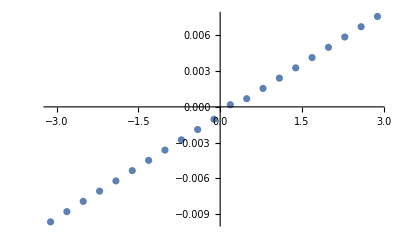

```mathematica
ListPlot@Module[{x=11,p=6},Join[{#[[1]],-#[[2]]}&/@ΔVλ1[[p]][[1;;x]]  , ΔVλ1[[p]][[x+1;;-1]] ]]
```

```mathematica
(*x,p*)
xList={{10,1},{11,2},{11,3},{11,4},{11,5},{11,6}};
```

```mathematica
(*x,p*)
xList={{2,1},{2,2},{2,3},{2,4},{2,5},{2,6}};
```

```mathematica
func=Array[Func0,Np];
fit=Array[Fit0,Np];
Do[
Δvλ= Module[{x=xList[[p,1]]},Join[{#[[1]],-#[[2]]}&/@ΔVλ1[[p]][[1;;x]]  , ΔVλ1[[p]][[x+1;;-1]] ]];
fit[[p]] =FindFit[ Δvλ, b (x-a),{a,b},x];
func[[p]]= b(x-a)/.fit[[p]];
,{p,1,Length@xList}]
```

```mathematica
(*fit1=FindFit[ ΔVλ[[1;;9]]  , b(x-a),{a,b},x]
fit2=FindFit[ ΔVλ[[10;;-1]] , b(x-a),{a,b},x]
func1= b(x-a)/.fit1;
func2= b(x-a)/.fit2;*)
```

```mathematica
p=1;N@fromJmat[parametersMat[[1,p]][[1]]]
```

```mathematica
βΓ=Table[  {fromJmat[parametersMat[[1,p,1]]][[3]],fit[[p]][[2,2]] },{p,1,Np}]
```

{{0.,0.00399671},{0.0711009,0.00347681},{0.143832,0.00315033},{0.219949,0.00294191},{0.301485,0.00283287},{0.390945,0.00287414}}

```mathematica
(*Show[
ListPlot[ βΓ, Joined->False ,Frame->True,ImageSize->600,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"\\Gamma","\\alpha"}, FrameStyle->Directive[Black,20], PlotRange->Automatic,   PlotLabel->MaTeX["\\text{Lagrange multiplier vs }\\Gamma",Magnification->1.8]   , PlotMarkers->"OpenMarkers"  , PlotStyle->Black,PlotLegends-> Placed[{  MaTeX[StringJoin["h=.01" ],Magnification->1.6] } , Scaled[{0.875,.3}] ]
],
Plot[αΓfunc,{Γ,0,.5},PlotStyle->{Black,Dashed},PlotLegends-> Placed[{  MaTeX[ TeXForm[ NumberForm[#,3]&/@αΓfunc],Magnification->1.6] } , Scaled[{0.82,.15}] ]
]]*)
```

```mathematica
func2=Array[Func0,Np];
fit2=Array[Fit0,Np];
Do[
Δvλ= Module[{x=xList[[p,1]]},Join[{#[[1]],-#[[2]]}&/@ΔVλ1[[p]][[1;;x]]  , ΔVλ1[[p]][[x+1;;-1]] ]];
fit2[[p]] =FindFit[ Δvλ, b (x-a),{a,b},x];
func2[[p]]= b(x-a)/.fit2[[p]];
,{p,1,Length@xList}]
```

```mathematica
αΓ2=Table[  {fromJmat[parametersMat[[1,p,1]]][[3]],fit[[p]][[1,2]] },{p,1,Np}]
```

{{0.,-0.205197},{0.0711009,-0.111597},{0.143832,-0.0304116},{0.219949,0.0482866},{0.301485,0.134251},{0.390945,0.24212}}

```mathematica
αΓ=Table[  {fromJmat[parametersMat[[1,p,1]]][[3]],fit[[p]][[1,2]] },{p,1,Np}]
```

{{0.,-0.228232},{0.0711009,-0.125766},{0.143832,-0.0441101},{0.219949,0.031526},{0.301485,0.109846},{0.390945,0.202074}}

```mathematica
αΓfit2=FindFit[ αΓ2, a + b x,{a,b},x];
αΓfunc2=( a + b Γ)/.αΓfit2;
```

```mathematica
αΓfit=FindFit[ αΓ, a + b x,{a,b},x];
αΓfunc=( a + b Γ)/.αΓfit;
Print["a=",a/.αΓfit,"; b=",b/.αΓfit];
```

a=-0.211148; b=1.07533

```mathematica
Export[ "C:\\User\\lucas\\Desktop\\Wolfram Mathematica\\PhD-codes\\Figures_PhD\\Lag multiplier\\lag-m-h.01_.3.pdf", % ]
```

C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\Figures_PhD\Lag multiplier\lag-m-h.01_.3.pdf

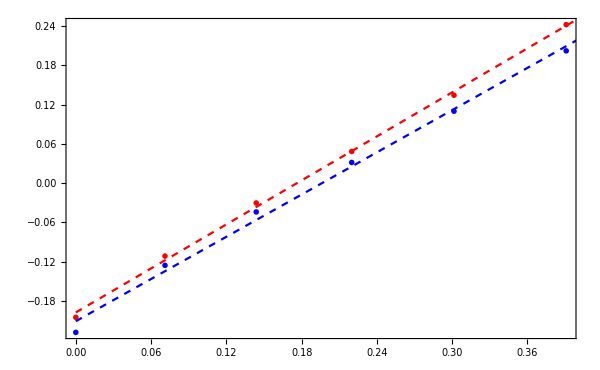

```mathematica
Show[
ListPlot[ {αΓ,αΓ2}, Joined->False ,Frame->True,ImageSize->600,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"\\Gamma","\\alpha"}, FrameStyle->Directive[Black,20], PlotRange->Automatic,   PlotLabel->MaTeX["\\text{Lagrange multiplier vs }\\Gamma",Magnification->1.8]   , PlotMarkers->"OpenMarkers"  , PlotStyle->{Blue,Red},PlotLegends-> Placed[{  MaTeX[StringJoin["h=.3" ],Magnification->1.6] ,MaTeX[StringJoin["h=.01" ],Magnification->1.6] } , Scaled[{0.875,.35}] ]
],
Plot[{αΓfunc,αΓfunc2},{Γ,0,.5},PlotStyle->{{Blue,Dashed},{Red,Dashed}},PlotLegends-> Placed[{  MaTeX[ TeXForm[ NumberForm[#,3]&/@αΓfunc],Magnification->1.6],
  MaTeX[ TeXForm[ NumberForm[#,3]&/@αΓfunc2],Magnification->1.6] } , Scaled[{0.82,.15}] ]
]]
```

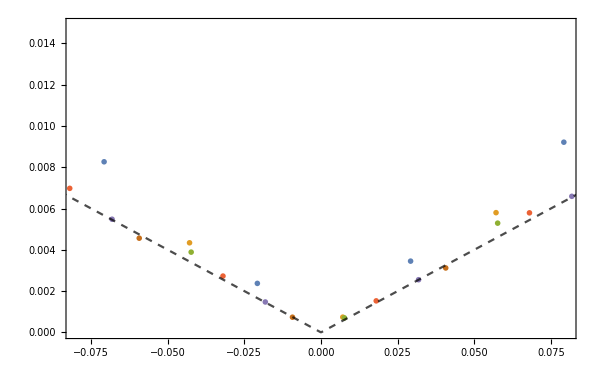

```mathematica
{min,max}=MinMax[ ΔVλ[[;;,;;,1]],.1];
Show[ 
ListPlot[ Table[{ΔVλ[[p,t,1]]-αΓ[[p,2]]  ,  ΔVλ[[p,t,2]]},{p,1,Np},{t,1,Length[ΔVλ[[1]] ]  }], Joined->False ,Frame->True,ImageSize->600,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"\\qquad \\alpha - \\alpha(\\Gamma)", " \\Delta \\mathrm{V}\\big(\\alpha - \\alpha(\\Gamma)\\, \\big) "}, FrameStyle->Directive[Black,20], PlotRange->{{-.08,.08},Full},Epilog->{Inset[MaTeX["\\alpha(\\Gamma)=-0.21+1.08\\,\\Gamma",Magnification->1.3] ,Scaled[{0.18,.9}] ]   },   PlotLabel->MaTeX["\\text{Constraint violation - } h=.3",Magnification->1.38]   , PlotMarkers->"OpenMarkers"  , PlotLegends-> Placed[
Table[  MaTeX[StringJoin["\\Gamma=",ToString[NumberForm[fromJmat[parametersMat[[1,p,1]]][[3]],{4,2}]]     ],Magnification->1.2] 
,{p,1,Np}] ,After ]   ]    ,
Plot[ .08Abs[x],{x,min,max} ,
PlotStyle->{Black,Dashed,Opacity[.7]},PlotLegends-> Placed[{  MaTeX[TeXForm[ NumberForm[#,2]&/@( .8Abs[α])   ],Magnification->1.3] } , Scaled[{0.85,.1}]   ]    ]
]
```

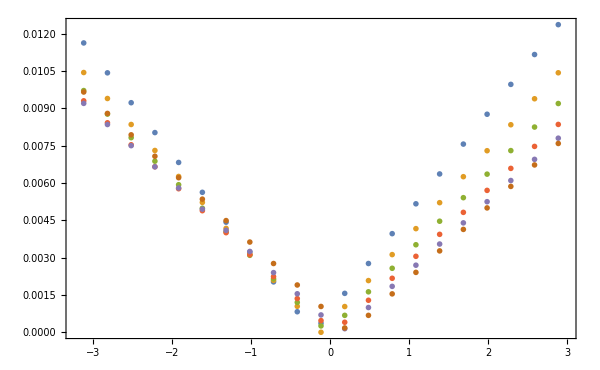

```mathematica
{min,max}=MinMax[ ΔVλ[[;;,;;,1]],.1];
Show[ 
ListPlot[ ΔVλ, Joined->False ,Frame->True,ImageSize->600,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"\\alpha \\quad [\\lambda = \\tilde{\\lambda}  + \\alpha \\mathbf{h}] ", " \\Delta \\mathrm{V} = || \\mathrm{tr}(\\mathrm{V}\\cdot\\mathrm{G}^\\gamma) || "}, FrameStyle->Directive[Black,20], PlotRange->{{min,max},Automatic},   PlotLabel->MaTeX["\\text{Constraint violation - } h=.01",Magnification->1.38]   , PlotMarkers->"OpenMarkers"  , PlotLegends-> Placed[
Table[  MaTeX[StringJoin["\\Gamma=",ToString[NumberForm[fromJmat[parametersMat[[1,p,1]]][[3]],{4,2}]]     ],Magnification->1.2] 
,{p,1,Np}] ,After ]   ]   (*  ,
Plot[ Abs[func[[3]] ],{x,min,max},PlotStyle->{Black,Dashed,Opacity[.7]},PlotLegends-> Placed[{  MaTeX[TeXForm[ NumberForm[#,2]&/@N@Abs[func[[p]]  ]],Magnification->1.3] } , Scaled[{0.82,.15}] ]]*)
]
```

```mathematica
{TeXForm[i],TeXForm[ⅈ Superscript[c,{x,y,z}[[1]] ] Superscript[c,{x,y,z}[[2]] ]  ],TeXForm[c^2]}
```

{i,i c^x c^y,c^2}

```mathematica
ClearAll[w]
Do[     
        (*If[j<i, *)w[i,j]=StringJoin[{ "\\left<", StringJoin[ ToString/@(TeXForm/@ {ⅈ, Superscript[c,{"0","x","y","z"}[[i]] ], Superscript[c,{"0","x","y","z"}[[j]]  ]  })   ], "\\right>"   } ]        (*];   *)  ;
If[i<j, w[i,j]=-w[j,i]];
If[i==j,w[i,j]=0]; 
,{i,1,4},{j,1,4}]

(*Print@Array[w,{4,4}]*)

wmat={{0,-w[2,1],-w[3,1],-w[4,1]},{w[2,1],0,-w[3,2],-w[4,2]},{w[3,1],w[3,2],0,-w[4,3]},{w[4,1],w[4,2],w[4,3],0}}
(*FullSimplify[   With[{γ=1},(traceM[wmat][[γ]])^2 + (traceG[wmat][[γ]])^2  ] ]
wmat=Sum[ hc[[γ]] Gmat[[γ]],{γ,1,3}]
FullSimplify[   Sum[ (traceM[wmat][[γ]])^2  + (traceG[wmat][[γ]])^2 , {γ,1,3}] ]*)

(*Export[ "C:\\User\\lucas\\Desktop\\Wolfram Mathematica\\PhD-codes\\Figures_PhD\\Lag multiplier\\constraint-violation-Gamma0.3-rescaled.pdf", % ]*)
```

{{0,-\left<ic^{\text{x}}c^0\right>,-\left<ic^{\text{y}}c^0\right>,-\left<ic^{\text{z}}c^0\right>},{\left<ic^{\text{x}}c^0\right>,0,-\left<ic^{\text{y}}c^{\text{x}}\right>,-\left<ic^{\text{z}}c^{\text{x}}\right>},{\left<ic^{\text{y}}c^0\right>,\left<ic^{\text{y}}c^{\text{x}}\right>,0,-\left<ic^{\text{z}}c^{\text{y}}\right>},{\left<ic^{\text{z}}c^0\right>,\left<ic^{\text{z}}c^{\text{x}}\right>,\left<ic^{\text{z}}c^{\text{y}}\right>,0}}

```mathematica
FullSimplify[    1/4 Sum[ (*(traceM[wmat][[γ]])^2  +*) (traceG[wmat][[γ]])^2 , {γ,1,3}]    ]
```

(\left<ic^{\text{y}}c^{\text{x}}\right>+\left<ic^{\text{z}}c^0\right>)^2+(\left<ic^{\text{y}}c^0\right>-\left<ic^{\text{z}}c^{\text{x}}\right>)^2+(\left<ic^{\text{x}}c^0\right>+\left<ic^{\text{z}}c^{\text{y}}\right>)^2

```mathematica
(*Table[{min,max}=MinMax[ ΔVλ[[p]][[;;,1]],.1];
Show[ ListPlot[ {ΔVλ[[p]]}, Joined->False ,Frame->True,ImageSize->600,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"\\alpha \\quad [\\lambda = \\tilde{\\lambda}  + \\alpha \\mathbf{h}] ", " \\Delta \\mathrm{V} = || \\mathrm{tr}(\\mathrm{V}\\cdot\\mathrm{G}^\\gamma) || "}, FrameStyle->Directive[Black,20], PlotRange->{{min,max},Automatic}, PlotLabel->MaTeX["\\text{Constraint violation - } h=.01",Magnification->1.8], PlotMarkers->"OpenMarkers", 
PlotLegends-> Placed[{  MaTeX[StringJoin["\\Gamma=", ToString[NumberForm[fromJmat[parametersMat[[1,p,1]]][[3]],{4,2}]]   ],Magnification->1.6] } , Scaled[{0.875,.3}] ] ],
Plot[ Abs[func[[p]] ],{x,min,max},PlotLegends-> Placed[{  MaTeX[TeXForm[ NumberForm[#,2]&/@N@Abs[func[[p]]  ]],Magnification->1.6] } , Scaled[{0.82,.15}] ]]
],{p,1,Np}]*)
```

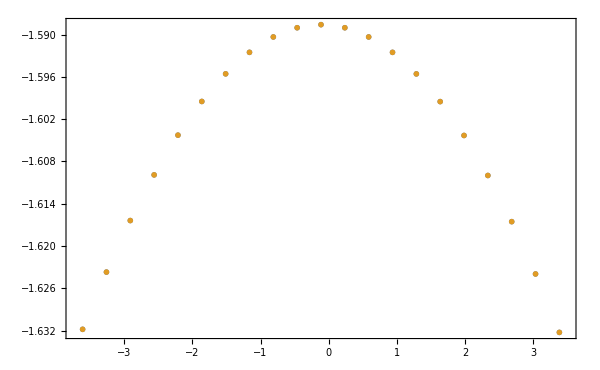

```mathematica
ListPlot[ {{#[[1]],2#[[2]]}&/@ΔenSumλ,{#[[1]],2#[[2]]}&/@ΔenSum2}, Joined->False ,Frame->True,ImageSize->600,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"\\alpha \\quad [\\lambda = \\tilde{\\lambda}  + \\alpha \\mathbf{h}] ", " \\left< H \\right>_{\\mathrm{MF}} "}, FrameStyle->Directive[Black,20], PlotRange->{{min,max},Automatic},   PlotLabel->MaTeX["\\text{Energy vs Lagrange multiplier}",Magnification->1.8]   , PlotMarkers->"OpenMarkers"  , PlotLegends-> Placed[{    MaTeX["h=0.1",Magnification->1.6] ,  MaTeX["h=0.2",Magnification->1.6] } , Scaled[{0.659,.15}] ]
]
```

```mathematica
(*list00= loadDataALL[toPath800[parametersMat[[1,1]],Ls[[1]],acuracy,"free",NbName ]  ];
ΔVλ=Sort@Flatten[ Table[list00[[i,6,6,1;;3]][[1]],{i,1,1}], 1];
Δenλ=Sort@Flatten[ Table[list00[[i,6,6,1;;3]][[2]],{i,1,1}], 1];
ΔenSumλ=Sort@Flatten[ Table[list00[[i,6,6,1;;3]][[3]],{i,1,1}], 1];*)
```

#### lagrange multiplier

```mathematica
ΔVλ={};Δenλ={};ΔenSumλ={};
```

```mathematica
ηs={-1.1,-.9,-.8};
```

```mathematica
Do[Module[{ L,Jmat,Nc,h,Λ,T,H,ξ,EnG0,En,EnList={{},{},{}},u,u2,U,V,j,Δ1=1,Δ2=1,ES,gap,Δt,ΔtHours,ΔtMin,ΔtSec,kTable,ΔV,ΔVseq={},Δseq={},EMF,Esum,cMF,η,hp ,Tk=1/(√2)Tkmom,Umatvec,l=1,p=1}, L=Ls[[l]]; hp=Mod[p,Length@hV,1];
η=ηs[[η0]];
{Jmat,h}=parametersMat[[1,p]][[1;;2]];Nc=L^2;(*If[ p==1, UG=Uguess; VG=Vguess; ];*)  
UG=Uguess; VG=Vguess;  U=UG; V=VG;   kTable=toMomentumTable[L];
For[j=1,( ( j<(steps))∧(Chop[ Δ1,10^(-acuracy) ]!= 0) ), j++,  
	Umatvec=UmatVec[Jmat,h,U,V, kTable,Tk,η] ;
u=Chop@Sum [  Module[{k,𝕌,𝕌less,𝕌gtr},k=kTable[[l]];𝕌=Tk . Umatvec[[l]];𝕌less=𝕌[[;;,5;;8]]; 𝕌gtr=𝕌[[;;,1;;4]];
(ⅈ/Nc)Conjugate@Chop@{Conjugate[𝕌gtr] . Transpose[𝕌gtr] Exp[ⅈ k . nx]+𝕌less . 𝕌less† Exp[-ⅈ k . nx], Conjugate[𝕌gtr] . Transpose[𝕌gtr] Exp[ⅈ k . ny]+𝕌less . 𝕌less† Exp[-ⅈ k . ny], Conjugate[𝕌gtr] . Transpose[𝕌gtr]+ 𝕌less . 𝕌less†} 
  ],{l,1,Nc} ]; 

U[[1]]=u[[1]][[1;;4,5;;8]] ;U[[2]]=u[[2]][[1;;4,5;;8]];U[[3]]=u[[3]][[1;;4,5;;8]];V[[1]]=u[[3]][[1;;4,1;;4]];V[[2]]=u[[3]][[5;;8,5;;8]];
ΔV=1/12 Sum[Sqrt@ Total[Power[#,2]&/@traceG[V[[σ]]]  ],{σ,1,2}]; ΔVseq={ΔVseq,{j,ΔV}} ;   
If[j>=2,Δ2=Δ1; Δ1=Max[ Abs@(u-u2) ];Δseq={Δseq,{j,Δ1}}  ;   ]; u2=u;                    
Print["j=",j,"; ΔV=",ΔV,"; Δ=",Δ1];
                             ];
t1=AbsoluteTime[]; Δt=UnitConvert[ Quantity[t1 -t0, "Seconds" ], "Minutes" ]; t0=t1;
Δseq=Partition[Flatten[Δseq],2]; ΔVseq=Partition[Flatten[ΔVseq],2];
	EMF   = enMFmom[Jmat,U,V,h];
Esum =enSUMmom[Jmat,U,V,h,L];
cMF   =cMFmom[Jmat,U,V];

	(*dataToFile800[parametersMat[[1,p]],L,acuracy,{j,L,U,V,{0,0},{{EMF},{Esum},{cMF},Δseq,ΔVseq}},"free",NbName]; 
Print["Max Step = ", j,"; Delta=",round@Δ1,(*,"; Δt = ",IntegerPart[Δt],IntegerPart@UnitConvert[FractionalPart[Δt], "Seconds" ]*)"; E=",{EMF,Esum,cMF},
";  p=",p,"/",Length@parametersMat[[1]]];
{jG,LG,UG,UG,ξG,EnG}= loadData[toPath800[parametersMat[[1,p]],L,acuracy,"free",NbName ]  ];*)
AppendTo[ΔVλ,{η,ΔV}];AppendTo[Δenλ,{η,EMF}];AppendTo[ΔenSumλ,{η,Esum}];

 ];  , {η0,1,Length@ηs}]
```

#### lagrange multiplier 2

```mathematica
ΔVλ={};Δenλ={};ΔenSumλ={};
```

```mathematica
ηs={-1.1,-.9,-.8};
```

```mathematica
Do[Module[{ L,Jmat,Nc,h,Λ,T,H,ξ,EnG0,En,EnList={{},{},{}},u,u2,U,V,j,Δ1=1,Δ2=1,ES,gap,Δt,ΔtHours,ΔtMin,ΔtSec,kTable,ΔV,ΔVseq={},Δseq={},EMF,Esum,cMF,η,hp ,Tk=1/(√2)Tkmom,Umatvec,l=1,p=1}, L=Ls[[l]]; hp=Mod[p,Length@hV,1];
η=ηs[[η0]];
{Jmat,h}=parametersMat[[1,p]][[1;;2]];Nc=L^2;(*If[ p==1, UG=Uguess; VG=Vguess; ];*)  
UG=Uguess; VG=Vguess;  U=UG; V=VG;   kTable=toMomentumTable[L];
For[j=1,( ( j<(steps))∧(Chop[ Δ1,10^(-acuracy) ]!= 0) ), j++,  
	Umatvec=UmatVec[Jmat,h,U,V, kTable,Tk,η] ;
u=Chop@Sum [  Module[{k,𝕌,𝕌less,𝕌gtr},k=kTable[[l]];𝕌=Tk . Umatvec[[l]];𝕌less=𝕌[[;;,5;;8]]; 𝕌gtr=𝕌[[;;,1;;4]];
(ⅈ/Nc)Conjugate@Chop@{Conjugate[𝕌gtr] . Transpose[𝕌gtr] Exp[ⅈ k . nx]+𝕌less . 𝕌less† Exp[-ⅈ k . nx], Conjugate[𝕌gtr] . Transpose[𝕌gtr] Exp[ⅈ k . ny]+𝕌less . 𝕌less† Exp[-ⅈ k . ny], Conjugate[𝕌gtr] . Transpose[𝕌gtr]+ 𝕌less . 𝕌less†} 
  ],{l,1,Nc} ]; 

U[[1]]=u[[1]][[1;;4,5;;8]] ;U[[2]]=u[[2]][[1;;4,5;;8]];U[[3]]=u[[3]][[1;;4,5;;8]];V[[1]]=u[[3]][[1;;4,1;;4]];V[[2]]=u[[3]][[5;;8,5;;8]];
ΔV=1/12 Sum[Sqrt@ Total[Power[#,2]&/@traceG[V[[σ]]]  ],{σ,1,2}]; ΔVseq={ΔVseq,{j,ΔV}} ;   
If[j>=2,Δ2=Δ1; Δ1=Max[ Abs@(u-u2) ];Δseq={Δseq,{j,Δ1}}  ;   ]; u2=u;                    
Print["j=",j,"; ΔV=",ΔV,"; Δ=",Δ1];
                             ];
t1=AbsoluteTime[]; Δt=UnitConvert[ Quantity[t1 -t0, "Seconds" ], "Minutes" ]; t0=t1;
Δseq=Partition[Flatten[Δseq],2]; ΔVseq=Partition[Flatten[ΔVseq],2];
	EMF   = enMFmom[Jmat,U,V,h];
Esum =enSUMmom[Jmat,U,V,h,L];
cMF   =cMFmom[Jmat,U,V];

	(*dataToFile800[parametersMat[[1,p]],L,acuracy,{j,L,U,V,{0,0},{{EMF},{Esum},{cMF},Δseq,ΔVseq}},"free",NbName]; 
Print["Max Step = ", j,"; Delta=",round@Δ1,(*,"; Δt = ",IntegerPart[Δt],IntegerPart@UnitConvert[FractionalPart[Δt], "Seconds" ]*)"; E=",{EMF,Esum,cMF},
";  p=",p,"/",Length@parametersMat[[1]]];
{jG,LG,UG,UG,ξG,EnG}= loadData[toPath800[parametersMat[[1,p]],L,acuracy,"free",NbName ]  ];*)
AppendTo[ΔVλ,{η,ΔV}];AppendTo[Δenλ,{η,EMF}];AppendTo[ΔenSumλ,{η,Esum}];

 ];  , {η0,1,Length@ηs}]
```

```mathematica
Do[
Γ0=fromJmat[parametersMat[[1,p]][[1]]][[3]];
α0=-0.2+1.13 Γ0;
ηs=Table[.01 η+α0,{η,-1,1,1}];
ηs={-0.2,.1,1};
ΔVλ={};Δenλ={};ΔenSumλ={};
Do[
Module[{ L,Jmat,Nc,h,Λ,T,H,ξ,EnG0,En,EnList={{},{},{}},u,u2,U,V,j,Δ1=1,Δ2=1,ES,gap,Δt,ΔtHours,ΔtMin,ΔtSec,kTable,ΔV,ΔVseq={},Δseq={},EMF,Esum,cMF,η,hp ,Tk=(1/Sqrt[2] )Tkmom,Umatvec,l=1}, L=Ls[[l]]; hp=Mod[p,Length@hV,1];
η=ηs[[η0]];
Print["Eta=",η];
{Jmat,h}=parametersMat[[1,p]][[1;;2]];Nc=L^2;(*If[ p==1, UG=Uguess; VG=Vguess; ];*)  
UG=0 Uguess; VG=Vguess;  U=UG; V=Table[Sum[h[[γ]]Mmat[[γ]],{γ,1,3}],2];   kTable=toMomentumTable[L];

For[j=1,( ( j<(steps))∧(Chop[ Δ1,10^(-acuracy) ]!= 0) ), j++,  

	Umatvec=UmatVec[Jmat,h,U,V, kTable,Tk,η] ;
u=Chop@Sum [  Module[{k,𝕌,𝕌less,𝕌gtr},k=kTable[[l]];𝕌=Tk . Umatvec[[l]];𝕌less=𝕌[[;;,5;;8]]; 𝕌gtr=𝕌[[;;,1;;4]];
(I/Nc)Conjugate@Chop@{Conjugate[𝕌gtr].Transpose[𝕌gtr] Exp[I k.nx]+𝕌less . 𝕌less† Exp[-I k . nx], 
Conjugate[𝕌gtr].Transpose[𝕌gtr] Exp[I k.ny]+𝕌less . 𝕌less† Exp[-I k . ny], 
Conjugate[𝕌gtr].Transpose[𝕌gtr]+ 𝕌less . 𝕌less†} 
  ],{l,1,Nc} ]; 

U[[1]]=u[[1]][[1;;4,5;;8]] ;U[[2]]=u[[2]][[1;;4,5;;8]];U[[3]]=u[[3]][[1;;4,5;;8]];V[[1]]=u[[3]][[1;;4,1;;4]];V[[2]]=u[[3]][[5;;8,5;;8]];
ΔV=1/12 Sum[Sqrt@ Total[Power[#,2]&/@traceG[V[[σ]]]  ],{σ,1,2}]; ΔVseq={ΔVseq,{j,ΔV}} ;   
If[j>=2,Δ2=Δ1; Δ1=Max[ Abs@(u-u2) ];Δseq={Δseq,{j,Δ1}}  ;   ]; u2=u;                    
Print["    j=",j,"; ΔV=",ΔV,"; Δ=",Δ1];
                             ];
t1=AbsoluteTime[]; Δt=UnitConvert[ Quantity[t1 -t0, "Seconds" ], "Minutes" ]; t0=t1;
Δseq=Partition[Flatten[Δseq],2]; ΔVseq=Partition[Flatten[ΔVseq],2];
EMF   = enMFmom[Jmat,U,V,h,η];
Esum  = enSUMmom[Jmat,U,V,h,L,η];
cMF   = cMFmom[Jmat,U,V];
Print[];
Print[MatrixForm/@round@U];Print[MatrixForm/@round@V]; V0=V;
Print[fromJmat[parametersMat[[1,p]][[1]]]];
Print["Eta=",η,(*"p=",p,"/",Length@parametersMat[[1]], *)"; j= ", j,"; Delta=",round@Δ1,"; EMF=",EMF,"; Esum=",Esum,"; EMF-Esum=",round[EMF-Esum]   ];
Print[];
	(*dataToFile800[parametersMat[[1,p]],L,acuracy,{j,L,U,V,{0,0},{{EMF},{Esum},{cMF},Δseq,ΔVseq}},"free",NbName]; 

{jG,LG,χG,ωG,ξG,EnG}= loadData[toPath800[parametersMat[[1,p]],L,acuracy,"free",NbName ]  ];*)
AppendTo[ΔVλ,{η,ΔV}];AppendTo[Δenλ,{η,EMF}];AppendTo[ΔenSumλ,{η,Esum}];

 ]; , {η0,1,Length@ηs}] ;
 
(*  dataToFile800[parametersMat[[1,p]],Ls[[1]],acuracy,
{fromJmat[parametersMat[[1,p]][[1]]],Ls[[1]],{0},{0},{0,0},{{0},{0},{0},{0},{0},{ΔVλ,Δenλ,ΔenSumλ,ηs}  }},
"free",NbName];  *)
 
 ,{p,1,Length@parametersMat[[1]] }]
```

## Loop 1

```mathematica
tV={.01,.01};
ts = Table[ {5x,160,-12x,0,-60},{x,tV}];
hs =Table[  h[[1]]  hAngle[h[[2]],h[[3]]] , {h,hV}];  
eV0=0;U=2600;JH=300; 
d0={.5,1};

parametersMat=
N@Table[Flatten[ Table[{
JmatMicro[              0,JH,U,ts[[t]],d0[[t]],s0],hs[[h]],
JmatMicro[eVs[[ev]],JH,U,ts[[t]],d0[[t]],s0],hV[[h]],tV[[t]],eVs[[ev]]
} , {t,1,Length@tV},  {h,1,Length@hV}],1] ,  {ev,1,Length@eVs} ];
```

```mathematica
(*parametersMat[[-1]]*)
```

#### lagrange multiplier 2

```mathematica
(*ΔVλ={};Δenλ={};ΔenSumλ={};
ηs={-1.1,-.9,-.8};*)
```

```mathematica
(*Do[Module[{ L,Jmat,Nc,h,Λ,T,H,ξ,EnG0,En,EnList={{},{},{}},u,u2,U,V,j,Δ1=1,Δ2=1,ES,gap,Δt,ΔtHours,ΔtMin,ΔtSec,kTable,ΔV,ΔVseq={},Δseq={},EMF,Esum,cMF,η,hp ,Tk=1/(√2)Tkmom,Umatvec,l=1,p=1}, L=Ls[[l]]; hp=Mod[p,Length@hV,1];
η=ηs[[η0]];
{Jmat,h}=parametersMat[[1,p]][[1;;2]];Nc=L^2;(*If[ p==1, UG=Uguess; VG=Vguess; ];*)  
UG=Uguess; VG=Vguess;  U=UG; V=VG;   kTable=toMomentumTable[L];
For[j=1,( ( j<(steps))∧(Chop[ Δ1,10^(-acuracy) ]!= 0) ), j++,  
	Umatvec=UmatVec[Jmat,h,U,V, kTable,Tk,η] ;
u=Chop@Sum [  Module[{k,𝕌,𝕌less,𝕌gtr},k=kTable[[l]];𝕌=Tk . Umatvec[[l]];𝕌less=𝕌[[;;,5;;8]]; 𝕌gtr=𝕌[[;;,1;;4]];
(ⅈ/Nc)Conjugate@Chop@{𝕌gtr^* . 𝕌gtr^ᵀ Exp[ⅈ k . nx]+𝕌less . 𝕌less† Exp[-ⅈ k . nx], 𝕌gtr^* . 𝕌gtr^ᵀ Exp[ⅈ k . ny]+𝕌less . 𝕌less† Exp[-ⅈ k . ny], 𝕌gtr^* . 𝕌gtr^ᵀ+ 𝕌less . 𝕌less†} 
  ],{l,1,Nc} ]; 

U[[1]]=u[[1]][[1;;4,5;;8]] ;U[[2]]=u[[2]][[1;;4,5;;8]];U[[3]]=u[[3]][[1;;4,5;;8]];V[[1]]=u[[3]][[1;;4,1;;4]];V[[2]]=u[[3]][[5;;8,5;;8]];
ΔV=1/12 Sum[Sqrt@ Total[Power[#,2]&/@traceG[V[[σ]]]  ],{σ,1,2}]; ΔVseq={ΔVseq,{j,ΔV}} ;   
If[j>=2,Δ2=Δ1; Δ1=Max[ Abs@(u-u2) ];Δseq={Δseq,{j,Δ1}}  ;   ]; u2=u;                    
Print["j=",j,"; ΔV=",ΔV,"; Δ=",Δ1];
                             ];
t1=AbsoluteTime[]; Δt=UnitConvert[ Quantity[t1 -t0, "Seconds" ], "Minutes" ]; t0=t1;
Δseq=Partition[Flatten[Δseq],2]; ΔVseq=Partition[Flatten[ΔVseq],2];
	EMF   = enMFmom[Jmat,U,V,h];
Esum =enSUMmom[Jmat,U,V,h,L];
cMF   =cMFmom[Jmat,U,V];

	(*dataToFile800[parametersMat[[1,p]],L,acuracy,{j,L,U,V,{0,0},{{EMF},{Esum},{cMF},Δseq,ΔVseq}},"free",NbName]; 
Print["Max Step = ", j,"; Delta=",round@Δ1,(*,"; Δt = ",IntegerPart[Δt],IntegerPart@UnitConvert[FractionalPart[Δt], "Seconds" ]*)"; E=",{EMF,Esum,cMF},
";  p=",p,"/",Length@parametersMat[[1]]];
{jG,LG,UG,UG,ξG,EnG}= loadData[toPath800[parametersMat[[1,p]],L,acuracy,"free",NbName ]  ];*)
AppendTo[ΔVλ,{η,ΔV}];AppendTo[Δenλ,{η,EMF}];AppendTo[ΔenSumλ,{η,Esum}];

 ];  , {η0,1,Length@ηs}] 
*)
```

```mathematica
(*Do[
Γ0=fromJmat[parametersMat[[1,p]][[1]]][[3]];
α0=-0.2+1.13 Γ0;
ηs=Table[.1 η+α0,{η,-1,1,.5}];
ΔVλ={};Δenλ={};ΔenSumλ={};
Do[
Module[{ L,Jmat,Nc,h,Λ,T,H,ξ,EnG0,En,EnList={{},{},{}},u,u2,U,V,j,Δ1=1,Δ2=1,ES,gap,Δt,ΔtHours,ΔtMin,ΔtSec,kTable,ΔV,ΔVseq={},Δseq={},EMF,Esum,cMF,η,hp ,Tk=1/Sqrt[2] Tkmom,Umatvec,l=1}, L=Ls[[l]]; hp=Mod[p,Length@hV,1];
η=ηs[[η0]];
Print["Eta=",η];
{Jmat,h}=parametersMat[[1,p]][[1;;2]];Nc=L^2;(*If[ p==1, UG=Uguess; VG=Vguess; ];*)  
UG=Uguess; VG=Vguess;  U=UG; V=VG;   kTable=toMomentumTable[L];

For[j=1,( ( j<(steps))∧(Chop[ Δ1,10^(-acuracy) ]!= 0) ), j++,  

	Umatvec=UmatVec[Jmat,h,U,V, kTable,Tk,η] ;
u=Chop@Sum [  Module[{k,𝕌,𝕌less,𝕌gtr},k=kTable[[l]];𝕌=Tk . Umatvec[[l]];𝕌less=𝕌[[;;,5;;8]]; 𝕌gtr=𝕌[[;;,1;;4]];
(2I/Nc)Conjugate@Chop@{(*Conjugate[𝕌gtr].Transpose[𝕌gtr] Exp[I k.nx]+*)𝕌less . 𝕌less† Exp[-I k . nx], 
(*Conjugate[𝕌gtr].Transpose[𝕌gtr] Exp[I k.ny]+*)𝕌less . 𝕌less† Exp[-I k . ny], 
(*Conjugate[𝕌gtr].Transpose[𝕌gtr]+ *)𝕌less . 𝕌less†} 
  ],{l,1,Nc} ]; 

U[[1]]=u[[1]][[1;;4,5;;8]] ;U[[2]]=u[[2]][[1;;4,5;;8]];U[[3]]=u[[3]][[1;;4,5;;8]];V[[1]]=u[[3]][[1;;4,1;;4]];V[[2]]=u[[3]][[5;;8,5;;8]];
ΔV=1/12 Sum[Sqrt@ Total[Power[#,2]&/@traceG[V[[σ]]]  ],{σ,1,2}]; ΔVseq={ΔVseq,{j,ΔV}} ;   
If[j>=2,Δ2=Δ1; Δ1=Max[ Abs@(u-u2) ];Δseq={Δseq,{j,Δ1}}  ;   ]; u2=u;                    
Print["    j=",j,"; ΔV=",ΔV,"; Δ=",Δ1];
                             ];
t1=AbsoluteTime[]; Δt=UnitConvert[ Quantity[t1 -t0, "Seconds" ], "Minutes" ]; t0=t1;
Δseq=Partition[Flatten[Δseq],2]; ΔVseq=Partition[Flatten[ΔVseq],2];
EMF   = enMFmom[Jmat,U,V,h,η];
Esum  = enSUMmom[Jmat,U,V,h,L,η];
cMF   = cMFmom[Jmat,U,V];
Print[];
Print[fromJmat[parametersMat[[1,p]][[1]]]];
Print["Eta=",η,(*"p=",p,"/",Length@parametersMat[[1]], *)"; j= ", j,"; Delta=",round@Δ1,"; EMF=",EMF,"; Esum=",Esum,"; EMF-Esum=",round[EMF-Esum]   ];
Print[];
	(*dataToFile800[parametersMat[[1,p]],L,acuracy,{j,L,U,V,{0,0},{{EMF},{Esum},{cMF},Δseq,ΔVseq}},"free",NbName]; 

{jG,LG,χG,ωG,ξG,EnG}= loadData[toPath800[parametersMat[[1,p]],L,acuracy,"free",NbName ]  ];*)
AppendTo[ΔVλ,{η,ΔV}];AppendTo[Δenλ,{η,EMF}];AppendTo[ΔenSumλ,{η,Esum}];

 ]; , {η0,1,Length@ηs}] ;
 
  dataToFile800[parametersMat[[1,p]],Ls[[1]],acuracy,
{fromJmat[parametersMat[[1,p]][[1]]],Ls[[1]],{0},{0},{0,0},{{0},{0},{0},{0},{0},{ΔVλ,Δenλ,ΔenSumλ,ηs}  }},
"free",NbName];  
 
 ,{p,1,Length@parametersMat[[1]] }] *)
```

#### pure loop w/out vortices

```mathematica
Print[];
```

```mathematica
Print[];

Print["    Pure and with vortices "];Print[];
Do[   Module[{gauge="g0",J,K,Γ,Jmod,Kmod,Γmod,Jmat,JmatMod,Jv,Kv,Γv,L=Ls[[l]],Nc,h,T,En,EMF,Eλ,EnList={{},{},{}},u0,ES,Δt,hv,hp=Mod[p,Length@hV,1] }, 
      (* {J,K,Γ,h,Jmod,Kmod,Γmod}=parameters[[ev,p]][[1;;2]];*) 
{Jmat,h}=parametersMat[[ev,p]][[1;;2]]; {JmatMod,hv}=parametersMat[[ev,p]][[3;;4]];
(* Print["Jmat[z] ",MatrixForm[ Jmat[[3]] ],"; L=",L,"; h=(", hV[[ ph,1 ]],",",hV[[ ph,2 ]],",",hV[[ ph,3]],"); "];*)
Nc=L^2;T=Tmat[L,L]; K=fromJmat[Jmat][[2]]; Kmod=fromJmat[JmatMod][[2]];
Kv=uniform[K,L,L];Kv=add4VorticesMaxSpaced[ Kv,Kmod,L];u0=uniformU[1,L];
(* for Pure Kitaev model: *)
Module[ {h0=Norm[h],κ0,κ,χ0,ω0,Hpure,Tpure,Epure,Upure},   κ=N@round@toKappa[h];   χ0={0,0,0};  (* ω0=Table[ωGA,2,{r,1,Nc} ];*)
Hpure=Hreal[Kv,κ,toλ[h],u0,L,0, {0,0}] ;   Tpure=TmatPure[L]; Upure=UmatPure[Tpure† . Hpure . Tpure]; 
Epure=Total[Select[Quiet@Eigenvalues[Hpure],#<0&]]/(Nc);
{χ0[[1]],χ0[[2]],χ0[[3]]}=toMFparametersPure[Upure,u0,L,0];   (*χ0=χgauge4v[χ0,L];*)
(*Print[MatrixForm/@(χ0[[;;,1 ]])];*)(*
Print[ " eV0=",round[  parametersMat[[ev,p]][[-1]]/1700  ] ," x 1700","; Epure=",Epure,"; "]; *) 
dataToFilePure800[parametersMat[[ev,p]],L,acuracy, gauge,{0,L,χ0,{{},{}},{{{},{},{}},{{},{},{}}},{Epure} },NbName ]; 
(*If[ ev==1, Print["Kappa=",κ,"; Lambda=",toλ[h], "; L=",L,"; h=(", hV[[ hp,1 ]],",",hV[[ hp,2 ]],",",hV[[ hp,3]],"); "]; ];*)
                       ]; 
        ]  , {ev,1,Length[parametersMat]}, {l,1,Length@Ls}, {p,1,Length[parametersMat[[1]] ]}  ]
```

Pure and with vortices

List::fstr: File specification File["/home/lucas.freitas/Desktop/Lucas/Mathematica2/Files/805/pure/g0/t=0.01_eV=0._JKG=             -7\n{-2.3400 \[Times] 10  , -1.0000, 0.0007, 0.0000, 0.5000}_JKGmod=             -7\n{-2.3400 \[Times] 10  , -1.0000, 0.0007, 0.0000, 0.5000}/data"] is not a string of one or more characters.

CreateDirectory::nffil: File not found during CreateDirectory[File["/home/lucas.freitas/Desktop/Lucas/Mathematica2/Files/805/pure/g0/t=0.01_eV=0._JKG=             -7\n{-2.3400 \[Times] 10  , -1.0000, 0.0007, 0.0000, 0.5000}_JKGmod=             -7\n{-2.3400 \[Times] 10  , -1.0000, 0.0007, 0.0000, 0.5000}/data"]].

List::fstr: File specification File["/home/lucas.freitas/Desktop/Lucas/Mathematica2/Files/805/pure/g0/t=0.01_eV=0._JKG=             -7\n{-2.3400 \[Times] 10  , -1.0000, 0.0007, 0.0000, 0.5000}_JKGmod=             -7\n{-2.3400 \[Times] 10  , -1.0000, 0.0007, 0.0000, 0.5000}/graph"] is not a string of one or more characters.

CreateDirectory::nffil: File not found during CreateDirectory[File["/home/lucas.freitas/Desktop/Lucas/Mathematica2/Files/805/pure/g0/t=0.01_eV=0._JKG=             -7\n{-2.3400 \[Times] 10  , -1.0000, 0.0007, 0.0000, 0.5000}_JKGmod=             -7\n{-2.3400 \[Times] 10  , -1.0000, 0.0007, 0.0000, 0.5000}/graph"]].

Pure path=/home/lucas.freitas/Desktop/Lucas/Mathematica2/Files/805/pure/g0/t=0.01_eV=0._JKG=             -7
{-2.3400 × 10  , -1.0000, 0.0007, 0.0000, 0.5000}_JKGmod=             -7
{-2.3400 × 10  , -1.0000, 0.0007, 0.0000, 0.5000}/data/h=(0.001,0.,0.)_L=20_A=3.txt

OpenWrite::noopen: Cannot open "/home/lucas.freitas/Desktop/Lucas/Mathematica2/Files/805/pure/g0/t=0.01_eV=0._JKG=             -7\n{-2.3400 \[Times] 10  , -1.0000, 0.0007, 0.0000, 0.5000}_JKGmod=             -7\n{-2.3400 \[Times] 10  , -1.0000, 0.0007, 0.0000, 0.5000}/data/h=(0.001,0.,0.)_L=20_A=3.txt".

Write::strml: $Failed is not a string, stream, or list of strings and streams.

Write::noopen: Cannot open $Failed.

General::stream: $Failed is not a string, InputStream[ ], or OutputStream[ ].

$Aborted

```mathematica
(*Print["    Pure and with vortices "];Print[];
Do[   Module[{gauge="g0",J,K,Γ,Jmod,Kmod,Γmod,Jmat,JmatMod,Jv,Kv,Γv,L=Ls[[l]],Nc,h,T,En,EMF,Eλ,EnList={{},{},{}},u0,ES,Δt,hp=Mod[p,Length@hV,1] }, 
      (* {J,K,Γ,h,Jmod,Kmod,Γmod}=parameters[[ev,p]][[1;;2]];*) 
{Jmat,h}=parametersMat[[ev,p]][[1;;2]]; {JmatMod,hv}=parametersMat[[ev,p]][[3;;4]];
(* Print["Jmat[z] ",MatrixForm[ Jmat[[3]] ],"; L=",L,"; h=(", hV[[ ph,1 ]],",",hV[[ ph,2 ]],",",hV[[ ph,3]],"); "];*)
Nc=L^2;T=Tmat[L,L]; K=fromJmat[Jmat][[2]]; Kmod=fromJmat[JmatMod][[2]];
Kv=uniform[K,L,L];Kv=add4VorticesMaxSpaced[ Kv,Kmod,L];u0=uniformU[1,L];
(* for Pure Kitaev model: *)
Module[ {h0=Norm[h],κ0,κ,χ0,ω0,Hpure,Tpure,Epure,Upure},   κ=N@round@toKappa[h];   χ0={0,0,0};  (* ω0=Table[ωGA,2,{r,1,Nc} ];*)
Hpure=Hreal[Kv,κ,toλ[h],u0,L,0, {0,0}] ;   Tpure=TmatPure[L]; Upure=UmatPure[Tpure† . Hpure . Tpure]; 
Epure=Total[Select[Quiet@Eigenvalues[Hpure],#<0&]]/(Nc);
{χ0[[1]],χ0[[2]],χ0[[3]]}=toMFparametersPure[Upure,u0,L,0];   (*χ0=χgauge4v[χ0,L];*)
(*Print[MatrixForm/@(χ0[[;;,1 ]])];*)
Print[ " eV0=",round[  parametersMat[[ev,p]][[-1]]/1700  ] ," x 1700","; Epure=",Epure,"; "];  
dataToFilePure800[parametersMat[[ev,p]],L,acuracy, gauge,{0,L,χ0,{{},{}},{{{},{},{}},{{},{},{}}},{Epure} },NbName ]; 
(*If[ ev==1, Print["Kappa=",κ,"; Lambda=",toλ[h], "; L=",L,"; h=(", hV[[ hp,1 ]],",",hV[[ hp,2 ]],",",hV[[ hp,3]],"); "]; ];*)
                       ]; 
        ]  , {ev,1,Length[parametersMat]}, {l,1,Length@Ls}, {p,1,Length[parametersMat[[1]] ]}  ]   *)
```

#### pure loop w/ vortices

```mathematica
Print[];Print["    Pure and with vortices "];Print[];
Do[   Module[{gauge="g4",J,K,Γ,Jmod,Kmod,Γmod,Jmat,JmatMod,Jv,Kv,Γv,L=Ls[[l]],Nc,h,hv,T,En,EMF,Eλ,EnList={{},{},{}},u0,ES,Δt,hp=Mod[p,Length@hV,1] }, 
{Jmat,h}=parametersMat[[ev,p]][[1;;2]]; {JmatMod,hv}=parametersMat[[ev,p]][[3;;4]];Nc=L^2;
T=Tmat[L,L];K=fromJmat[Jmat][[2]]; Kmod=fromJmat[JmatMod][[2]];
Kv=uniform[K,L,L];Kv=add4VorticesMaxSpaced[ Kv,Kmod,L];
u0=gauge4v[uniformU[1,L],L];
Module[ {h0=Norm[h],κ0,κ,χ0,ω0,Hpure,Tpure,Epure,Upure},   κ=round@toKappa[h]; χ0={0,0,0};  (* ω0=Table[ωGA,2,{r,1,Nc} ];*) 
Hpure=Hreal[Kv,κ,toλ[h],u0,L,0, {0,0}] ;   Tpure=TmatPure[L]; Upure=UmatPure[Tpure† . Hpure . Tpure]; 
Epure=Total[Select[Quiet@Eigenvalues[Hpure],#<0&]]/(Nc);
{χ0[[1]],χ0[[2]],χ0[[3]]}=toMFparametersPure[Upure,u0,L,0];   
χ0=χgauge4v[χ0,L];(*
Print[ " eV0=",round[  parametersMat[[ev,p]][[-1]]/1700  ] ," x 1700","; Epure=",Epure,"; "];  *)
dataToFilePure800[parametersMat[[ev,p]],L,acuracy, gauge,{0,L,χ0,{{},{}},{{{},{},{}},{{},{},{}}},{Epure} },NbName ]; 
       ]; 
        ]  , {ev,1,Length[parametersMat]}, {l,1,Length@Ls}, {p,1,Length[parametersMat[[1]] ]}  ]
```

Pure and with vortices

Pure path=C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\Mathematica2\Files\805\pure\g4\t=0.01_eV=0._JKG={0.0000, -1.0000, 0.0007, 0.0000, 0.0000}_JKGmod={0.0000, -1.0000, 0.0007, 0.0000, 0.0000}\data\h=(0.001,0.,0.)_L=12_A=3.txt

Pure path=C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\Mathematica2\Files\805\pure\g4\t=0.01_eV=0._JKG={0.0000, -1.0000, 0.0007, 0.0000, 0.0000}_JKGmod={0.0000, -1.0000, 0.0007, 0.0000, 0.0000}\data\h=(0.001,0.,0.)_L=12_A=3.txt

Pure path=C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\Mathematica2\Files\805\pure\g4\t=0.01_eV=170._JKG={0.0000, -1.0000, 0.0007, 0.0000, 0.0000}_JKGmod={0.0000, -1.0230, 0.0007, 0.0000, 0.0512}\data\h=(0.001,0.,0.)_L=12_A=3.txt

Pure path=C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\Mathematica2\Files\805\pure\g4\t=0.01_eV=170._JKG={0.0000, -1.0000, 0.0007, 0.0000, 0.0000}_JKGmod={0.0000, -1.0230, 0.0007, 0.0000, 0.1023}\data\h=(0.001,0.,0.)_L=12_A=3.txt

Pure path=C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\Mathematica2\Files\805\pure\g4\t=0.01_eV=340._JKG={0.0000, -1.0000, 0.0007, 0.0000, 0.0000}_JKGmod={0.0000, -1.0960, 0.0008, 0.0000, 0.1096}\data\h=(0.001,0.,0.)_L=12_A=3.txt

Pure path=C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\Mathematica2\Files\805\pure\g4\t=0.01_eV=340._JKG={0.0000, -1.0000, 0.0007, 0.0000, 0.0000}_JKGmod={0.0000, -1.0960, 0.0008, 0.0000, 0.2193}\data\h=(0.001,0.,0.)_L=12_A=3.txt

Pure path=C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\Mathematica2\Files\805\pure\g4\t=0.01_eV=510._JKG={0.0000, -1.0000, 0.0007, 0.0000, 0.0000}_JKGmod={0.0000, -1.2330, 0.0009, 0.0000, 0.1849}\data\h=(0.001,0.,0.)_L=12_A=3.txt

Pure path=C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\Mathematica2\Files\805\pure\g4\t=0.01_eV=510._JKG={0.0000, -1.0000, 0.0007, 0.0000, 0.0000}_JKGmod={0.0000, -1.2330, 0.0009, 0.0000, 0.3698}\data\h=(0.001,0.,0.)_L=12_A=3.txt

Pure path=C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\Mathematica2\Files\805\pure\g4\t=0.01_eV=680._JKG={0.0000, -1.0000, 0.0007, 0.0000, 0.0000}_JKGmod={0.0000, -1.4590, 0.0010, 0.0000, 0.2918}\data\h=(0.001,0.,0.)_L=12_A=3.txt

Pure path=C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\Mathematica2\Files\805\pure\g4\t=0.01_eV=680._JKG={0.0000, -1.0000, 0.0007, 0.0000, 0.0000}_JKGmod={0.0000, -1.4590, 0.0010, 0.0000, 0.5835}\data\h=(0.001,0.,0.)_L=12_A=3.txt

Pure path=C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\Mathematica2\Files\805\pure\g4\t=0.01_eV=850._JKG={0.0000, -1.0000, 0.0007, 0.0000, 0.0000}_JKGmod={0.0000, -1.8300, 0.0013, 0.0000, 0.4574}\data\h=(0.001,0.,0.)_L=12_A=3.txt

Pure path=C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\Mathematica2\Files\805\pure\g4\t=0.01_eV=850._JKG={0.0000, -1.0000, 0.0007, 0.0000, 0.0000}_JKGmod={0.0000, -1.8300, 0.0013, 0.0000, 0.9148}\data\h=(0.001,0.,0.)_L=12_A=3.txt

Pure path=C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\Mathematica2\Files\805\pure\g4\t=0.01_eV=1020._JKG={0.0000, -1.0000, 0.0007, 0.0000, 0.0000}_JKGmod={0.0000, -2.4630, 0.0017, 0.0000, 0.7388}\data\h=(0.001,0.,0.)_L=12_A=3.txt

Pure path=C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\Mathematica2\Files\805\pure\g4\t=0.01_eV=1020._JKG={0.0000, -1.0000, 0.0007, 0.0000, 0.0000}_JKGmod={0.0000, -2.4630, 0.0017, 0.0000, 1.4780}\data\h=(0.001,0.,0.)_L=12_A=3.txt

Pure path=C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\Mathematica2\Files\805\pure\g4\t=0.01_eV=1190._JKG={0.0000, -1.0000, 0.0007, 0.0000, 0.0000}_JKGmod={0.0000, -3.6470, 0.0026, 0.0000, 1.2770}\data\h=(0.001,0.,0.)_L=12_A=3.txt

Pure path=C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\Mathematica2\Files\805\pure\g4\t=0.01_eV=1190._JKG={0.0000, -1.0000, 0.0007, 0.0000, 0.0000}_JKGmod={0.0000, -3.6470, 0.0026, 0.0000, 2.5530}\data\h=(0.001,0.,0.)_L=12_A=3.txt

Pure path=C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\Mathematica2\Files\805\pure\g4\t=0.01_eV=1360._JKG={0.0000, -1.0000, 0.0007, 0.0000, 0.0000}_JKGmod={0.0000, -6.2920, 0.0045, 0.0000, 2.5170}\data\h=(0.001,0.,0.)_L=12_A=3.txt

Pure path=C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\Mathematica2\Files\805\pure\g4\t=0.01_eV=1360._JKG={0.0000, -1.0000, 0.0007, 0.0000, 0.0000}_JKGmod={0.0000, -6.2920, 0.0045, 0.0000, 5.0330}\data\h=(0.001,0.,0.)_L=12_A=3.txt

```mathematica
(*Print[];Print["    Pure and with vortices "];Print[];
Do[   Module[{gauge="g4",J,K,Γ,Jmod,Kmod,Γmod,Jmat,JmatMod,Jv,Kv,Γv,L=Ls[[l]],Nc,h,T,En,EMF,Eλ,EnList={{},{},{}},u0,ES,Δt,hp=Mod[p,Length@hV,1] }, 
{Jmat,h}=parametersMat[[ev,p]][[1;;2]]; {JmatMod,hv}=parametersMat[[ev,p]][[3;;4]];Nc=L^2;
T=Tmat[L,L];K=fromJmat[Jmat][[2]]; Kmod=fromJmat[JmatMod][[2]];
Kv=uniform[K,L,L];Kv=add4VorticesMaxSpaced[ Kv,Kmod,L];
u0=gauge4v[uniformU[1,L],L];
Module[ {h0=Norm[h],κ0,κ,χ0,ω0,Hpure,Tpure,Epure,Upure},   κ=round@toKappa[h]; χ0={0,0,0};  (* ω0=Table[ωGA,2,{r,1,Nc} ];*) 
Hpure=Hreal[Kv,κ,toλ[h],u0,L,0, {0,0}] ;   Tpure=TmatPure[L]; Upure=UmatPure[Tpure† . Hpure . Tpure]; 
Epure=Total[Select[Quiet@Eigenvalues[Hpure],#<0&]]/(Nc);
{χ0[[1]],χ0[[2]],χ0[[3]]}=toMFparametersPure[Upure,u0,L,0];   
χ0=χgauge4v[χ0,L];
Print[ " eV0=",round[  parametersMat[[ev,p]][[-1]]/1700  ] ," x 1700","; Epure=",Epure,"; "];  
dataToFilePure800[parametersMat[[ev,p]],L,acuracy, gauge,{0,L,χ0,{{},{}},{{{},{},{}},{{},{},{}}},{Epure} },NbName ]; 
       ]; 
        ]  , {ev,1,Length[parametersMat]}, {l,1,Length@Ls}, {p,1,Length[parametersMat[[1]] ]}  ]   *)
```

#### vortex free momentum

```mathematica
Print[" "];Print[" "];Print["    Starting free loop"];Print[" "];
t0=AbsoluteTime[]; 

Do[ Γ0=fromJmat[parametersMat[[1,p]][[1]]][[3]];  α0=-0.2+1.13 Γ0;
Module[{ L,Jmat,Nc,h,Λ,T,H,ξ,EnG0,En,EnList={{},{},{}},UG,VG,u,u2,U,V,j,Δ1=1,Δ2=1,ES,gap,Δt,ΔtHours,ΔtMin,ΔtSec,kTable,ΔV,ΔVseq={},Δseq={},EMF,Esum,cMF,η,hp ,Tk=1/Sqrt[2] Tkmom,Umatvec,l=1}, 
L=Ls[[l]]; hp=Mod[p,Length@hV,1];
η=α0;(* Print["Eta=",η];*)
{Jmat,h}=parametersMat[[1,p]][[1;;2]]; Nc=L^2;(*If[ p==1, UG=Uguess; VG=Vguess; ];*)  (*If[h==hs[[1]], UG=Uguess;  VG=Vguess;];*)  
UG=Uguess; VG=Vguess; U=UG;  V=VG;  kTable=toMomentumTable[L];

For[j=1,( (j<(steps))∧(Chop[Δ1,10^(-acuracy-1)]!=0) ), j++, Umatvec=UmatVec[Jmat,h,U,V,kTable,Tk,η];
u=Chop@Sum[Module[{k,𝕌,𝕌less,𝕌gtr},k=kTable[[l]];𝕌=Tk . Umatvec[[l]]; 𝕌less=𝕌[[;;,5;;8]]; (*𝕌gtr=𝕌[[;;,1;;4]];*)(2I/Nc)Chop@{𝕌less . 𝕌less† Exp[-I k . nx], 𝕌less . 𝕌less† Exp[-I k . ny],𝕌less . 𝕌less†} ],{l,1,Nc} ]; 
U[[1]]=u[[1]][[1;;4,5;;8]]; U[[2]]=u[[2]][[1;;4,5;;8]]; U[[3]]=u[[3]][[1;;4,5;;8]]; V[[1]]=u[[3]][[1;;4,1;;4]]; V[[2]]=u[[3]][[5;;8,5;;8]];
ΔV=1/(8 Sqrt[3]) Sum[Sqrt@Total[  Power[#,2]&/@traceG[V[[σ]]]  ],{σ,1,2}]; ΔVseq={ΔVseq,{j,ΔV}} ;   
If[j>=2,Δ2=Δ1; Δ1=Max[ Abs@(u-u2) ];Δseq={Δseq,{j,Δ1}};   ];  u2=u;                    
Print["    j=",j,"; ΔV=",ΔV,"; Δ=",Δ1];                          ];
t1=AbsoluteTime[]; Δt=UnitConvert[ Quantity[t1-t0, "Seconds" ], "Minutes" ]; t0=t1;
Δseq=Partition[Flatten[Δseq],2]; ΔVseq=Partition[Flatten[ΔVseq],2];
EMF   = enMFmom[Jmat,U,V,h,η];
Esum  = enSUMmom[Jmat,U,V,h,L,η];
cMF   = cMFmom[Jmat,U,V];
Print[];
Print[fromJmat[parametersMat[[1,p]][[1]]]]; Print[];
Print["Eta=",round@η,"; p=",p,"/",Length@parametersMat[[1]],"; j= ", j,"; Delta=",round@Δ1,"; EMF=",EMF,"; Esum=",Esum,"; EMF-Esum=",round[EMF-Esum]   ];
Print[];
	
dataToFile800[parametersMat[[1,p]],L,acuracy,{j,L,U,V,{0,0},{{EMF},{Esum},{cMF},Δseq,ΔVseq}},"free",NbName]; 
{jG,LG,χG,ωG,ξG,EnG}= loadData[toPath800[parametersMat[[1,p]],L,acuracy,"free",NbName ]  ];  
(*AppendTo[ΔVλ,{η,ΔV}];AppendTo[Δenλ,{η,EMF}];AppendTo[ΔenSumλ,{η,Esum}]; *)  ];   
,{p,1,Length@parametersMat[[1]]} ]; Print[" "];
```

Starting free loop

j=1; ΔV=0.0000737043; Δ=1

j=2; ΔV=0.0000419509; Δ=0.00010703

j=3; ΔV=0.0000231417; Δ=0.0000630913

{0,-1.,0.000708334,0,0}

Eta=-0.1992; p=1/2; j= 4; Delta=0.000063; EMF=-0.786549; Esum=-0.786548; EMF-Esum=-1.×10^-6

j=1; ΔV=0.0000737043; Δ=1

j=2; ΔV=0.0000419509; Δ=0.00010703

j=3; ΔV=0.0000231417; Δ=0.0000630913

{0,-1.,0.000708334,0,0}

Eta=-0.1992; p=2/2; j= 4; Delta=0.000063; EMF=-0.786549; Esum=-0.786548; EMF-Esum=-1.×10^-6

```mathematica
(*Print["    Starting free loop"]; Print[" "];
t0=AbsoluteTime[]; 
Do[ Γ0=fromJmat[parametersMat[[1,p]][[1]]][[3]];  α0=-0.2+1.13 Γ0;
Module[{ L,Jmat,Nc,h,Λ,T,H,ξ,EnG0,En,EnList={{},{},{}},UG,VG,u,u2,U,V,j,Δ1=1,Δ2=1,ES,gap,Δt,ΔtHours,ΔtMin,ΔtSec,kTable,ΔV,ΔVseq={},Δseq={},EMF,Esum,cMF,η,hp ,Tk=1/Sqrt[2] Tkmom,Umatvec,l=1}, 
L=Ls[[l]]; hp=Mod[p,Length@hV,1];
η=α0;(* Print["Eta=",η];*)
{Jmat,h}=parametersMat[[1,p]][[1;;2]]; Nc=L^2;(*If[ p==1, UG=Uguess; VG=Vguess; ];*)  (*If[h==hs[[1]], UG=Uguess;  VG=Vguess;];*)  
UG=Uguess; VG=Vguess; U=UG;  V=VG;  kTable=toMomentumTable[L];

For[j=1,( (j<(steps))∧(Chop[Δ1,10^(-acuracy)]!=0) ), j++, Umatvec=UmatVec[Jmat,h,U,V,kTable,Tk,η];
u=Chop@Sum[Module[{k,𝕌,𝕌less,𝕌gtr},k=kTable[[l]];𝕌=Tk . Umatvec[[l]]; 𝕌less=𝕌[[;;,5;;8]]; (*𝕌gtr=𝕌[[;;,1;;4]];*)
(2I/Nc)(*Conjugate@*)Chop@{𝕌less . 𝕌less† Exp[-I k . nx], 𝕌less . 𝕌less† Exp[-I k . ny],𝕌less . 𝕌less†} ],{l,1,Nc} ]; 
U[[1]]=u[[1]][[1;;4,5;;8]]; U[[2]]=u[[2]][[1;;4,5;;8]]; U[[3]]=u[[3]][[1;;4,5;;8]]; V[[1]]=u[[3]][[1;;4,1;;4]]; V[[2]]=u[[3]][[5;;8,5;;8]];
(*Print[MatrixForm/@round@U];*)
ΔV=1/(8 Sqrt[3]) Sum[Sqrt@Total[  Power[#,2]&/@traceG[V[[σ]]]  ],{σ,1,2}]; ΔVseq={ΔVseq,{j,ΔV}} ;   
If[j>=2,Δ2=Δ1; Δ1=Max[ Abs@(u-u2) ];Δseq={Δseq,{j,Δ1}};   ];  u2=u;                    
Print["    j=",j,"; ΔV=",ΔV,"; Δ=",Δ1];                          ];
t1=AbsoluteTime[]; Δt=UnitConvert[ Quantity[t1-t0, "Seconds" ], "Minutes" ]; t0=t1;
Δseq=Partition[Flatten[Δseq],2]; ΔVseq=Partition[Flatten[ΔVseq],2];
EMF   = enMFmom[Jmat,U,V,h,η];
Esum  = enSUMmom[Jmat,U,V,h,L,η];
cMF   = cMFmom[Jmat,U,V];
Print[];
Print[fromJmat[parametersMat[[1,p]][[1]]]]; Print[];
Print["Eta=",round@η,"; p=",p,"/",Length@parametersMat[[1]],"; j= ", j,"; Delta=",round@Δ1,"; EMF=",EMF,"; Esum=",Esum,"; EMF-Esum=",round[EMF-Esum]   ];
Print[];
	
dataToFile800[parametersMat[[1,p]],L,acuracy,{j,L,U,V,{0,0},{{EMF},{Esum},{cMF},Δseq,ΔVseq}},"free",NbName]; 
{jG,LG,χG,ωG,ξG,EnG}= loadData[toPath800[parametersMat[[1,p]],L,acuracy,"free",NbName ]  ];  
(*AppendTo[ΔVλ,{η,ΔV}];AppendTo[Δenλ,{η,EMF}];AppendTo[ΔenSumλ,{η,Esum}]; *)  ];   
,{p,1,Length@parametersMat[[1]]} ]; Print[" "]; 
*)
```

#### vortex free + electric field

```mathematica
Module[{Δt}, t0v=AbsoluteTime[];
Δt= UnitConvert[ Quantity[N[t0v-tvf], "Seconds" ], "Minutes" ];   
Print["Free loop timing= ", IntegerPart[Δt],IntegerPart@UnitConvert[FractionalPart[Δt], "Seconds" ]    ];t0=t0v;
Print[" "]; Print[" "];
];
Print["    Starting vortex free + electric field loop: "];Print[" "]
```

Free loop timing= IntegerPart[1/60 (3.90534×10^9-1. tvf)] minIntegerPart[60 FractionalPart[1/60 (3.90534×10^9-1. tvf)]] s

Starting vortex free + electric field loop:

```mathematica
minSteps=3;
Do[  Module[
{ L=Ls[[l]],Nc,h,En,EnList={{},{},{}},EMF,Esum,Econst,u0,u1,u2,U,ξ,V,j,Δ1=1,Δ2=1,ES,gap,Δt,ΔtHours,ΔtMin,ΔtSec,kTable,ΔV,ΔVseq={},Δseq={},η,p,Jmat,JmatMod,hv,gauge="g0",Jarray,T},
 p=Length[hV](pt-1)+ph;         Nc=L^2; T=Tmat[L,L]; 
{Jmat,h}=parametersMat[[ev,p]][[1;;2]]; {JmatMod,hv}=parametersMat[[ev,p]][[3;;4]];
Print["JmatMod ",fromJmat[JmatMod],"; L=",L,"; h=(", hV[[ ph,1 ]],",",hV[[ ph,2 ]],",",hV[[ ph,3]],"); "];
	u0=uniformU[1,L]; (* <-  the 2nd difference : gauge4v *) 	
η=-0.2 +1.13 fromJmat[Jmat][[3]];
{jG,LG,UG,VG,ξG,EnG}= loadData[toPath800[parametersMat[[1,p]],L,acuracy,"free",NbName ]  ];
	U=Table[UG,{r,1,Nc}];
	V=Table[VG,{r,1,Nc}];
Module[ {jpure,Lpure,χ0,ω0,ξ0,Epure}, 
{jpure,Lpure,χ0,ω0,ξ0,Epure}=Chop@loadDataPure[toPathPure800[parametersMat[[ev,p]],L,acuracy, gauge,NbName]    ];
Do[ U[[r,1]][[1,1]]=χ0[[1,r]][[1,1]]; U[[r,2]][[1,1]]=χ0[[2,r]][[1,1]]; U[[r,3]][[1,1]]=χ0[[3,r]][[1,1]]; ,{r,1,Nc}];           ]; 

Jmat0=Jmat;JmatMod0=JmatMod;
Jarray=Jarray4v[Table[Jmat,{r,1,L^2}],JmatMod,L];

For[j=1,  ( j<steps)∧((j<minSteps)∨(Chop[ Δ1, 10^(-acuracy+1)]!= 0)    ) , j++,   

Module[{H,u},  H=Hmf[Jarray,h,U,V,L,η] ;u=Quiet@UmatK[T† . H . T];  u1=Im@Chop@icc[u,L,T]; (*umat=u;*)

If[j>=2,Δ2=Δ1; Δ1=Max[ Abs@(u1-u2) ]; Δseq={Δseq,{j,Δ1}};  ΔV=1/(2 Nc) Sum[Abs[traceG[V[[r,σ]]]],{r,1,Nc},{σ,1,2}]; ΔVseq={ΔVseq,{j,ΔV}}    ]; 

EMF=EnMF[ Jarray,h,U,V, L,η];Esum=Quiet@eigenvaluesEmf[ Jarray,h,U,V, L,η];Econst=constantMF[Jarray,U,V,L];
EnList[[1]]={EnList[[1]],{j,EMF}};    EnList[[2]]={EnList[[2]],{j,Esum}};    EnList[[3]]={EnList[[3]],{j,Econst}};   

Do[ Module[{m,n,α,β,rz,rx,ry,Io}, rz=⌊R0/16⌋;β=⌊1+(R0-16rz)/4⌋;α=R0-16rz-4(β-1)+1;
    n=⌊rz/L⌋;m=rz-n L;rx=Mod[m+1,L]+n L;ry=m+Mod[n+1,L] L;Io=Mod[α+8rz,8Nc,1]; 
    U[[rz+1,1,α,β]]=u1[[Mod[β+4+8rx,8Nc,1],Io]];    U[[rz+1,2,α,β]]=u1[[Mod[β+4+8ry,8Nc,1],Io]];    U[[rz+1,3,α,β]]=u1[[Mod[β+4+8rz,8Nc,1],Io]];
    V[[rz+1,1,α,β]]=u1[[Mod[β+8rz,8Nc,1],Io]];    V[[rz+1,2,α,β]]=u1[[Mod[β+4+8rz,8Nc,1],Mod[Io+4,8Nc,1] ]];    ]; , {R0,0,16Nc-1}  ];    ]; 
(*u00=u1; *)
u2=u1;      Print[" j =",j, "/",steps, "; Delta V=",InputForm[ΔV], "; Delta=",InputForm[Δ1], ";  E=", round/@(2{EMF,Esum,Econst}),"; "  ];     
];  
(*Module[{H,u}, H=Hmf[Jarray,h,U,V,L,1]; u=Quiet@UmatK[T† . H . T]; {U,V,ξ,u1}=(*BiParallel*)bilinears[u,L,T];       ];  	*)    (*<-- rewrite bilinears   *)
Δseq=Partition[Flatten[Δseq],2];
	EnList[[1]]=Partition[Flatten[EnList[[1]]],2];
	EnList[[2]]=Partition[Flatten[EnList[[2]]],2];
	EnList[[3]]=Partition[Flatten[EnList[[3]]],2]; 
	ΔVseq=Partition[Flatten[ΔVseq],2]; 
	dataToFile800[parametersMat[[ev,p]],L,acuracy,{j,L,U,V,ξ,{EnList[[1]],EnList[[2]],EnList[[3]],Δseq,ΔVseq}},gauge,NbName];     

Print[ "ev=",ev ,"/", Length@eVs"; j MAX=",j, "/",steps, "; Delta=",Δ1, "; "   ]; 

 ]; , {ev,1      ,Length[parametersMat]} , {pt,1,Length@tV},  {ph,1,Length@hV}  ,{l,1,Length@Ls}];
Print[" "];
```

JmatMod {0,-1.,0.000708334,0,0}; L=12; h=(0.001,0,0);

j =1/150; Delta V=ΔV$1876023; Delta=1;  E={-1.5731,-1.5731,-1.5731};

j =2/150; Delta V={0, 0, 0}; Delta=0.00977573996306487;  E={-1.5731,-1.5731,-1.5731};

ev=1/9 ; j MAX=3/150; Delta=0.00977574;

JmatMod {0,-1.,0.000708334,0,0}; L=12; h=(0.001,0,0);

j =1/150; Delta V=ΔV$1882854; Delta=1;  E={-1.5731,-1.5731,-1.5731};

j =2/150; Delta V={0, 0, 0}; Delta=0.00977573996306487;  E={-1.5731,-1.5731,-1.5731};

ev=1/9 ; j MAX=3/150; Delta=0.00977574;

JmatMod {0,-1.02316,0.000724736,0,0.0511578}; L=12; h=(0.001,0,0);

j =1/150; Delta V=ΔV$1889685; Delta=1;  E={-1.57519,-1.57532,-1.57519};

j =2/150; Delta V={0, 0, 0}; Delta=0.0013116716350923818;  E={-1.57532,-1.57532,-1.57532};

ev=2/9 ; j MAX=3/150; Delta=0.00131167;

JmatMod {0,-1.02316,0.000724736,0,0.102316}; L=12; h=(0.001,0,0);

j =1/150; Delta V=ΔV$1896516; Delta=1;  E={-1.57519,-1.5757,-1.57519};

j =2/150; Delta V={0, 0, 0}; Delta=0.0052317542664346295;  E={-1.5757,-1.57571,-1.5757};

ev=2/9 ; j MAX=3/150; Delta=0.00523175;

JmatMod {0,-1.09642,0.000776634,0,0.109642}; L=12; h=(0.001,0,0);

j =1/150; Delta V=ΔV$1903347; Delta=1;  E={-1.58203,-1.58269,-1.58203};

j =2/150; Delta V={0, 0, 0}; Delta=0.006233876851755027;  E={-1.58269,-1.5827,-1.58269};

ev=3/9 ; j MAX=3/150; Delta=0.00623388;

JmatMod {0,-1.09642,0.000776634,0,0.219285}; L=12; h=(0.001,0,0);

j =1/150; Delta V=ΔV$1910178; Delta=1;  E={-1.58203,-1.58467,-1.58203};

j =2/150; Delta V={0, 0, 0}; Delta=0.024558319119868055;  E={-1.58467,-1.58482,-1.58467};

j =3/150; Delta V={0, 0, 0}; Delta=0.008975303771481258;  E={-1.58482,-1.58483,-1.58482};

ev=3/9 ; j MAX=4/150; Delta=0.0089753;

JmatMod {0,-1.23261,0.000873097,0,0.184891}; L=12; h=(0.001,0,0);

j =1/150; Delta V=ΔV$1920338; Delta=1;  E={-1.59557,-1.59786,-1.59557};

j =2/150; Delta V={0, 0, 0}; Delta=0.01855405725337833;  E={-1.59786,-1.59796,-1.59786};

j =3/150; Delta V={0, 0, 0}; Delta=0.0065636035227940315;  E={-1.59796,-1.59796,-1.59796};

ev=4/9 ; j MAX=4/150; Delta=0.0065636;

JmatMod {0,-1.23261,0.000873097,0,0.369782}; L=12; h=(0.001,0,0);

j =1/150; Delta V=ΔV$1930502; Delta=1;  E={-1.59557,-1.60472,-1.59557};

j =2/150; Delta V={0, 0, 0}; Delta=0.07006329795192645;  E={-1.60472,-1.6062,-1.60472};

j =3/150; Delta V={0, 0, 0}; Delta=0.05330368302345917;  E={-1.6062,-1.60662,-1.6062};

j =4/150; Delta V={0, 0, 0}; Delta=0.019345276709160975;  E={-1.60662,-1.60675,-1.60662};

j =5/150; Delta V={0, 0, 0}; Delta=0.017468788678976888;  E={-1.60675,-1.60679,-1.60675};

j =6/150; Delta V={0, 0, 0}; Delta=0.006600032795332056;  E={-1.60679,-1.6068,-1.60679};

ev=4/9 ; j MAX=7/150; Delta=0.00660003;

JmatMod {0,-1.45877,0.0010333,0,0.291755}; L=12; h=(0.001,0,0);

j =1/150; Delta V=ΔV$1950649; Delta=1;  E={-1.62012,-1.62765,-1.62012};

j =2/150; Delta V={0, 0, 0}; Delta=0.04740067131615067;  E={-1.62765,-1.62847,-1.62765};

j =3/150; Delta V={0, 0, 0}; Delta=0.0355005440263039;  E={-1.62847,-1.62864,-1.62847};

j =4/150; Delta V={0, 0, 0}; Delta=0.009756481854897081;  E={-1.62864,-1.62868,-1.62864};

ev=5/9 ; j MAX=5/150; Delta=0.00975648;

JmatMod {0,-1.45877,0.0010333,0,0.58351}; L=12; h=(0.001,0,0);

j =1/150; Delta V=ΔV$1964138; Delta=1;  E={-1.62012,-1.64997,-1.62012};

j =2/150; Delta V={0, 0, 0}; Delta=0.1529218675541213;  E={-1.64997,-1.66128,-1.64997};

j =3/150; Delta V={0, 0, 0}; Delta=0.26852454812105664;  E={-1.66128,-1.6696,-1.66128};

j =4/150; Delta V={0, 0, 0}; Delta=0.10304197512925489;  E={-1.6696,-1.67616,-1.6696};

j =5/150; Delta V={0, 0, 0}; Delta=0.23062154164041293;  E={-1.67616,-1.68241,-1.67616};

j =6/150; Delta V={0, 0, 0}; Delta=0.08616284947859351;  E={-1.68241,-1.68798,-1.68241};

j =7/150; Delta V={0, 0, 0}; Delta=0.20759954687516224;  E={-1.68798,-1.69286,-1.68798};

j =8/150; Delta V={0, 0, 0}; Delta=0.07060200411348524;  E={-1.69286,-1.69656,-1.69286};

j =9/150; Delta V={0, 0, 0}; Delta=0.15350054635090074;  E={-1.69656,-1.69904,-1.69656};

j =10/150; Delta V={0, 0, 0}; Delta=0.04529342533956735;  E={-1.69904,-1.70049,-1.69904};

j =11/150; Delta V={0, 0, 0}; Delta=1.968430204528031;  E={-1.70049,-1.70141,-1.70049};

j =12/150; Delta V={0, 0, 0}; Delta=0.025007991415996206;  E={-1.70141,-1.70184,-1.70141};

j =13/150; Delta V={0, 0, 0}; Delta=0.04177219190132328;  E={-1.70184,-1.70201,-1.70184};

j =14/150; Delta V={0, 0, 0}; Delta=0.011017144832008585;  E={-1.70201,-1.70209,-1.70201};

j =15/150; Delta V={0, 0, 0}; Delta=0.018827689985717863;  E={-1.70209,-1.70212,-1.70209};

j =16/150; Delta V={0, 0, 0}; Delta=0.005018820632093157;  E={-1.70212,-1.70214,-1.70212};

ev=5/9 ; j MAX=17/150; Delta=0.00501882;

JmatMod {0,-1.82959,0.00129596,0,0.457398}; L=12; h=(0.001,0,0);

j =1/150; Delta V=ΔV$2017579; Delta=1;  E={-1.66481,-1.69099,-1.66481};

j =2/150; Delta V={0, 0, 0}; Delta=0.10651824250131847;  E={-1.69099,-1.69802,-1.69099};

j =3/150; Delta V={0, 0, 0}; Delta=0.20393767231453258;  E={-1.69802,-1.7023,-1.69802};

j =4/150; Delta V={0, 0, 0}; Delta=0.06681825875021577;  E={-1.7023,-1.70521,-1.7023};

j =5/150; Delta V={0, 0, 0}; Delta=0.1660634197047609;  E={-1.70521,-1.70771,-1.70521};

j =6/150; Delta V={0, 0, 0}; Delta=0.0544354985943607;  E={-1.70771,-1.7099,-1.70771};

j =7/150; Delta V={0, 0, 0}; Delta=0.15075050351137387;  E={-1.7099,-1.71201,-1.7099};

j =8/150; Delta V={0, 0, 0}; Delta=0.05048062588203436;  E={-1.71201,-1.71397,-1.71201};

j =9/150; Delta V={0, 0, 0}; Delta=0.14229294175523532;  E={-1.71397,-1.71582,-1.71397};

j =10/150; Delta V={0, 0, 0}; Delta=0.045910856811327366;  E={-1.71582,-1.71743,-1.71582};

j =11/150; Delta V={0, 0, 0}; Delta=0.12647813329222593;  E={-1.71743,-1.71877,-1.71743};

j =12/150; Delta V={0, 0, 0}; Delta=0.03712469213522651;  E={-1.71877,-1.71979,-1.71877};

j =13/150; Delta V={0, 0, 0}; Delta=1.9273585318127395;  E={-1.71979,-1.72053,-1.71979};

j =14/150; Delta V={0, 0, 0}; Delta=0.03052457977877477;  E={-1.72053,-1.72127,-1.72053};

j =15/150; Delta V={0, 0, 0}; Delta=0.061480590153308284;  E={-1.72127,-1.72157,-1.72127};

j =16/150; Delta V={0, 0, 0}; Delta=0.015451370422434146;  E={-1.72157,-1.72173,-1.72157};

j =17/150; Delta V={0, 0, 0}; Delta=0.03332314848205684;  E={-1.72173,-1.72181,-1.72173};

j =18/150; Delta V={0, 0, 0}; Delta=0.008597371019654555;  E={-1.72181,-1.72186,-1.72181};

ev=6/9 ; j MAX=19/150; Delta=0.00859737;

JmatMod {0,-1.82959,0.00129596,0,0.914797}; L=12; h=(0.001,0,0);

j =1/150; Delta V=ΔV$2077674; Delta=1;  E={-1.66481,-1.76195,-1.66481};

j =2/150; Delta V={0, 0, 0}; Delta=0.25590364665353593;  E={-1.76195,-1.81857,-1.76195};

j =3/150; Delta V={0, 0, 0}; Delta=0.4470855667736895;  E={-1.81857,-1.85456,-1.81857};

j =4/150; Delta V={0, 0, 0}; Delta=0.12152029305383463;  E={-1.85456,-1.86883,-1.85456};

j =5/150; Delta V={0, 0, 0}; Delta=1.9578803977756547;  E={-1.86883,-1.87308,-1.86883};

j =6/150; Delta V={0, 0, 0}; Delta=0.034215301136555826;  E={-1.87308,-1.87411,-1.87308};

j =7/150; Delta V={0, 0, 0}; Delta=0.037033320958326094;  E={-1.87411,-1.87432,-1.87411};

j =8/150; Delta V={0, 0, 0}; Delta=0.007654852104881127;  E={-1.87432,-1.87437,-1.87432};

ev=6/9 ; j MAX=9/150; Delta=0.00765485;

JmatMod {0,-2.46258,0.00174433,0,0.738775}; L=12; h=(0.001,0,0);

j =1/150; Delta V=ΔV$2104479; Delta=1;  E={-1.74989,-1.84471,-1.74989};

j =2/150; Delta V={0, 0, 0}; Delta=0.1976995947816387;  E={-1.84471,-1.88493,-1.84471};

j =3/150; Delta V={0, 0, 0}; Delta=0.3975823107886661;  E={-1.88493,-1.90771,-1.88493};

j =4/150; Delta V={0, 0, 0}; Delta=0.09526538439374196;  E={-1.90771,-1.91693,-1.90771};

j =5/150; Delta V={0, 0, 0}; Delta=1.9569174968009997;  E={-1.91693,-1.92005,-1.91693};

j =6/150; Delta V={0, 0, 0}; Delta=0.030738572816063906;  E={-1.92005,-1.92092,-1.92005};

j =7/150; Delta V={0, 0, 0}; Delta=0.04110166096709865;  E={-1.92092,-1.92113,-1.92092};

j =8/150; Delta V={0, 0, 0}; Delta=0.008009722804824409;  E={-1.92113,-1.92119,-1.92113};

ev=7/9 ; j MAX=9/150; Delta=0.00800972;

JmatMod {0,-2.46258,0.00174433,0,1.47755}; L=12; h=(0.001,0,0);

j =1/150; Delta V=ΔV$2131284; Delta=1;  E={-1.74989,-2.02995,-1.74989};

j =2/150; Delta V={0, 0, 0}; Delta=0.2803120583904032;  E={-2.02995,-2.1436,-2.02995};

j =3/150; Delta V={0, 0, 0}; Delta=1.9120547099607805;  E={-2.1436,-2.1648,-2.1436};

j =4/150; Delta V={0, 0, 0}; Delta=0.04434721766978145;  E={-2.1648,-2.16721,-2.1648};

j =5/150; Delta V={0, 0, 0}; Delta=0.02987101626732292;  E={-2.16721,-2.16744,-2.16721};

j =6/150; Delta V={0, 0, 0}; Delta=0.004510029262401412;  E={-2.16744,-2.16746,-2.16744};

ev=7/9 ; j MAX=7/150; Delta=0.00451003;

JmatMod {0,-3.64728,0.00258349,0,1.27655}; L=12; h=(0.001,0,0);

j =1/150; Delta V=ΔV$2151431; Delta=1;  E={-1.92528,-2.21616,-1.92528};

j =2/150; Delta V={0, 0, 0}; Delta=0.20998043347594797;  E={-2.21616,-2.28626,-2.21616};

j =3/150; Delta V={0, 0, 0}; Delta=1.9489233720432269;  E={-2.28626,-2.29666,-2.28626};

j =4/150; Delta V={0, 0, 0}; Delta=0.029052241630254654;  E={-2.29666,-2.29779,-2.29666};

j =5/150; Delta V={0, 0, 0}; Delta=0.022698561377827383;  E={-2.29779,-2.2979,-2.29779};

j =6/150; Delta V={0, 0, 0}; Delta=0.0030657476693154197;  E={-2.2979,-2.29791,-2.2979};

ev=8/9 ; j MAX=7/150; Delta=0.00306575;

JmatMod {0,-3.64728,0.00258349,0,2.5531}; L=12; h=(0.001,0,0);

j =1/150; Delta V=ΔV$2171578; Delta=1;  E={-1.92528,-2.60201,-1.92528};

j =2/150; Delta V={0, 0, 0}; Delta=0.2311086448494315;  E={-2.60201,-2.71762,-2.60201};

j =3/150; Delta V={0, 0, 0}; Delta=1.9881963775907203;  E={-2.71762,-2.72322,-2.71762};

j =4/150; Delta V={0, 0, 0}; Delta=0.010795448098012474;  E={-2.72322,-2.72342,-2.72322};

j =5/150; Delta V={0, 0, 0}; Delta=0.004229722813326816;  E={-2.72342,-2.72343,-2.72342};

ev=8/9 ; j MAX=6/150; Delta=0.00422972;

JmatMod {0,-6.29158,0.00445654,0,2.51663}; L=12; h=(0.001,0,0);

j =1/150; Delta V=ΔV$2188396; Delta=1;  E={-2.34473,-3.09496,-2.34473};

j =2/150; Delta V={0, 0, 0}; Delta=0.1443279278165825;  E={-3.09496,-3.15044,-3.09496};

j =3/150; Delta V={0, 0, 0}; Delta=0.05776698293467403;  E={-3.15044,-3.15195,-3.15044};

j =4/150; Delta V={0, 0, 0}; Delta=0.004535021721161319;  E={-3.15195,-3.15199,-3.15195};

ev=9/9 ; j MAX=5/150; Delta=0.00453502;

JmatMod {0,-6.29158,0.00445654,0,5.03326}; L=12; h=(0.001,0,0);

j =1/150; Delta V=ΔV$2201885; Delta=1;  E={-2.34473,-3.90873,-2.34473};

j =2/150; Delta V={0, 0, 0}; Delta=0.1472964643466197;  E={-3.90873,-3.99005,-3.90873};

j =3/150; Delta V={0, 0, 0}; Delta=0.02983722733672185;  E={-3.99005,-3.99086,-3.99005};

j =4/150; Delta V={0, 0, 0}; Delta=0.0016832497044132824;  E={-3.99086,-3.99087,-3.99086};

ev=9/9 ; j MAX=5/150; Delta=0.00168325;

```mathematica
(*
minSteps=3;
Do[  Module[
{ L=Ls[[l]],Nc,h,En,EnList={{},{},{}},EMF,Esum,Econst,u0,u1,u2,U,ξ,V,j,Δ1=1,Δ2=1,ES,gap,Δt,ΔtHours,ΔtMin,ΔtSec,kTable,ΔV,ΔVseq={},Δseq={},η,p,Jmat,JmatMod,hv,gauge="g0",Jarray,T},
 p=Length[hV](pt-1)+ph;         Nc=L^2; T=1/Sqrt[2] Tmat[L,L]; 
{Jmat,h}=parametersMat[[ev,p]][[1;;2]]; {JmatMod,hv}=parametersMat[[ev,p]][[3;;4]];
Print["JmatMod=",fromJmat[JmatMod],"; L=",L,"; h=(", hV[[ ph,1 ]],",",hV[[ ph,2 ]],",",hV[[ ph,3]],"); "];
	u0=uniformU[1,L]; (* <-  the 2nd difference : gauge4v *) 	
    η=-0.2 +1.13 fromJmat[Jmat][[3]];
{jG,LG,UG,VG,ξG,EnG}= loadData[toPath800[parametersMat[[1,p]],L,acuracy,"free",NbName ]  ];
	U=Table[UG,{r,1,Nc}];
	V=Table[VG,{r,1,Nc}];
Module[ {jpure,Lpure,χ0,ω0,ξ0,Epure}, 
{jpure,Lpure,χ0,ω0,ξ0,Epure}=Chop@loadDataPure[toPathPure800[parametersMat[[ev,p]],L,acuracy, gauge,NbName]    ];
Do[ U[[r,1]][[1,1]]=χ0[[1,r]][[1,1]]; U[[r,2]][[1,1]]=χ0[[2,r]][[1,1]]; U[[r,3]][[1,1]]=χ0[[3,r]][[1,1]]; ,{r,1,Nc}];           ]; 
Jarray=Jarray4v[Table[Jmat,{r,1,L^2}],JmatMod,L];

For[j=1,  ( j<steps)∧((j<minSteps)∨(Chop[ Δ1, 10^(-acuracy+1)]!= 0)    ) , j++,   
Module[{H,u},  H=Hmf[Jarray,h,U,V,L,η]; u=Quiet@UmatK[ConjugateTranspose[T] . H . T];  u1=2 Chop@Conjugate@icc[u,L,T ]; (*umat=u;*)
If[j>=2,Δ2=Δ1; Δ1=Max[ Abs@(u1-u2) ]; Δseq={Δseq,{j,Δ1}};      ]; 

EMF=EnMF[ Jarray,h,U,V, L,η];Esum=Quiet@eigenvaluesEmf[ Jarray,h,U,V, L,η];Econst=constantMF[Jarray,U,V,L];
EnList[[1]]={EnList[[1]],{j,EMF}};    EnList[[2]]={EnList[[2]],{j,Esum}};    EnList[[3]]={EnList[[3]],{j,Econst}};   

Do[ Module[{m,n,α,β,rz,rx,ry,Io}, rz=⌊R0/16⌋;β=⌊1+(R0-16rz)/4⌋;α=R0-16rz-4(β-1)+1;
    n=⌊rz/L⌋;m=rz-n L;rx=Mod[m+1,L]+n L;ry=m+Mod[n+1,L] L;Io=Mod[α+8rz,8Nc,1]; 
    U[[rz+1,1,α,β]]=u1[[Mod[β+4+8rx,8Nc,1],Io]];    U[[rz+1,2,α,β]]=u1[[Mod[β+4+8ry,8Nc,1],Io]];    U[[rz+1,3,α,β]]=u1[[Mod[β+4+8rz,8Nc,1],Io]];
    V[[rz+1,1,α,β]]=u1[[Mod[β+8rz,8Nc,1],Io]];    V[[rz+1,2,α,β]]=u1[[Mod[β+4+8rz,8Nc,1],Mod[Io+4,8Nc,1] ]];    ]; , {R0,0,16Nc-1}  ];    ]; 
 
(* If[ev==1∧p==1,Module[{r2,i,r0}, r2=⌊1/2 ⌈L/2⌉⌋;i=1; r0=r2+L (-1+i+r2);
Print[MatrixForm/@round[#,1000]&@U[[r0]] ];
Print[MatrixForm/@round[#,100000]&@V[[r0]] ];
];   ]; *)
ΔV=1/(8 Sqrt[3] Nc) Sum[Sqrt@Total[ Power[#,2]&/@traceG[V[[r,σ]]] ] , {r,1,Nc},{σ,1,2}]; ΔVseq={ΔVseq,{j,ΔV}};
(*Do[ V[[r,σ]]=Sum[ 1/4 Mmat[[γ]] traceM[ V[[r,σ]] ][[γ]] ,{γ,1,3}],{σ,1,2},{r,1,Nc}];*)
  
u2=u1;      Print[" j =",j, "/",steps, "; Delta V=",ΔV, "; Delta=",Δ1, ";  E=", round/@({EMF,Esum,Econst}),"; "  ];     
];  
(*Module[{H,u}, H=Hmf[Jarray,h,U,V,L,1]; u=Quiet@UmatK[T† . H . T]; {U,V,ξ,u1}=(*BiParallel*)bilinears[u,L,T];       ];  	*)    (*<-- rewrite bilinears   *)
Δseq=Partition[Flatten[Δseq],2];
	EnList[[1]]=Partition[Flatten[EnList[[1]]],2];
	EnList[[2]]=Partition[Flatten[EnList[[2]]],2];
	EnList[[3]]=Partition[Flatten[EnList[[3]]],2]; 
	ΔVseq=Partition[Flatten[ΔVseq],2]; 
	dataToFile800[parametersMat[[ev,p]],L,acuracy,{j,L,U,V,ξ,{EnList[[1]],EnList[[2]],EnList[[3]],Δseq,ΔVseq}},gauge,NbName];     

Print[ "ev=",ev ,"/", Length@eVs"; j MAX=",j, "/",steps, "; Delta=",Δ1, "; "   ]; 

 ]; , {ev,1      ,Length[parametersMat]} , {pt,1,Length@tV},  {ph,1,Length@hV}  ,{l,1,Length@Ls}];
Print[" "];
*)
```

#### old 705 code

```mathematica
(*
minSteps=3;
Do[   
Module[{χG,ωG,jG,LG,EnG ,gauge="g0"},   (* <-  the 1st difference : g0 <-> g4 *)
Module[{ J,K,Γ,Jmod,Kmod,Γmod,Jv,Kv,Γv,L=Ls[[l]],Nc,h ,Λ,T,En,EMF,Esum,Eλ,EnList={{},{},{}},ξG,Δseq={},Δωseq={},Δω,u2=0,u1,u0,χ={0,0,0},ω={0,0},ξ={0,0},j,Δ1=1,Δ2=2.56,ES,gap,Δt,hp=Mod[p,Length@hV,1] }, 
{J,K,Γ,h,Jmod,Kmod,Γmod}=parameters[[1,p]][[1;;7]]; 
Nc=L^2;
ω=Table[ωGA,2,{r,1,Nc} ];
T=Tmat[L,L];
Kv=uniform[K,L,L];

u0=uniformU[-1,L]; (* <-  the 2nd difference : gauge4v *)

{jG,LG,χG,ωG,ξG,EnG}= loadData[toPath[parameters[[1,p]],L,acuracy,"free",NbName ]  ]; 
(*ωG=symω[ωG];*)
ω[[1]]=Table[ωG[[1]],{r,1,Nc} ];
ω[[2]]=Table[ωG[[2]],{r,1,Nc} ];
χ[[1]]=Table[χG[[1]],{r,1,Nc} ];
χ[[2]]=Table[χG[[2]],{r,1,Nc} ];
χ[[3]]=Table[χG[[3]],{r,1,Nc} ];

(* Print[" for Pure Kitaev model: " ];*)
(*Module[ {h0=Norm[h],κ0,κ,λ=toλ[h],χ0,Hpure,Tpure,Upure,Epure,Kv,K,Kmod,jpure,Lpure,χ0,ω0,ξ0,Epure},       
(*K=fromJmat[Jmat][[3]]; Kmod=fromJmat[JmatMod][[3]];
κ0=toKappa[h]; 
κ=N@(Round[10000 κ0]/10000);   
χ0={0,0,0};  (* ω0=Table[ωGA,2,{r,1,Nc} ];*)
Kv=add4VorticesMaxSpaced[ uniform[K,L,L],Kmod,L];
Hpure=Hreal[Kv,κ,λ,u0,L,0,{0,0}] ;   
Tpure=TmatPure[L];  
Upure=UmatPure[Tpure†.Hpure.Tpure];
Epure=Total[Select[Quiet@Eigenvalues[Hpure],#<0&] ]/(Nc);
{χ0[[1]],χ0[[2]],χ0[[3]]}=toMFparametersPure[Upure,u0,L,0];*)   
(*dataToFilePure[parameters[[1,p]],L,acuracy,gauge,{0,L,χ0,{{},{}},{{{},{},{}},{{},{},{}}},{Epure} } ]; 
Print["Pure data saved: "];
Print["Kappa=",κ,"; Lambda=", λ, "; Epure=",Epure,"; "];Print[];*)

{jpure,Lpure,χ0,ω0,ξ0,Epure}=Chop@loadDataPure[toPathPure[parametersMat[[ev,p]],L,acuracy, gauge,NbName]  ];
Do[ U[[r,1]][[1,1]]=χ0[[1,r]][[1,1]]; U[[r,2]][[1,1]]=χ0[[2,r]][[1,1]]; U[[r,3]][[1,1]]=χ0[[3,r]][[1,1]]; ,{r,1,Nc}];
  ];
*)

Module[ {h0=Norm[h],κ0,κ,λ=toλ[h],χ0,Hpure,Tpure,Upure,Epure},   
κ0=(*(h0/Sqrt[3])^3/(0.262)^2*) toKappa[h]; 
κ=N@(Round[10000 κ0]/10000);   
χ0={0,0,0};  (*
ω0=Table[ωGA,2,{r,1,Nc} ];*)
Hpure=Hreal[Kv,κ,λ,u0,L,0, {0,0}] ;   
Tpure=TmatPure[L];  
Upure=UmatPure[Tpure† . Hpure . Tpure];
Epure=Total[Select[Quiet@Eigenvalues[Hpure],#<0&]]/(Nc);
{χ0[[1]],χ0[[2]],χ0[[3]]}=toMFparametersPure[Upure,u0,L,0];   
dataToFilePure[parameters[[1,p]],L,acuracy,gauge,{0,L,χ0,{{},{}},{{{},{},{}},{{},{},{}}},{Epure} } ]; 
Print["Pure data saved: "];
Print["Kappa=",κ,"; Lambda=", λ, "; Epure=",Epure,"; "];Print[];
Do[ χ[[1,r]][[1,1]]=χ0[[1,r]][[1,1]]; χ[[2,r]][[1,1]]=χ0[[2,r]][[1,1]]; χ[[3,r]][[1,1]]=χ0[[3,r]][[1,1]]; ,{r,1,Nc}];
  ]; 

(*χ=χgauge4v[χ,L];*)   (* <-  the 3rd difference :  χgauge4v *)

 Do[ {J,K,Γ,h,Jmod,Kmod,Γmod}=parameters[[ev,p]][[1;;7]]; Print[" "];
Print["J=",J, "; K=",K, "; G=",Γ,"; Jmod=",Jmod, "; Kmod=",Kmod, "; Gmod=",Γmod, "; L=",L, "; h=(", hV[[ hp,1 ]],",",hV[[ hp,2 ]],",",hV[[ hp,3]],"); eV=",N[Round[1000 eVs[[ev]]/1700]/1000]"; "];Print[" "];
Kv=uniform[K,L,L];Kv=add4VorticesMaxSpaced[ Kv,Kmod,L];
Jv=uniform[J,L,L];Jv=add4VorticesMaxSpaced[ Jv,Jmod,L];
Γv=uniform[Γ,L,L];Γv=add4VorticesMaxSpaced[ Γv,Γmod,L];

For[j=1, ( j<steps)∧((j<minSteps)∨(Chop[ Δ1, 10^-acuracy ]!= 0)    ) , j++,   
If[j>=2,Δ2=Δ1; Δ1=Max[ Abs@(u1-u2) ]; Δseq={Δseq,{j,Δ1}};  Δω=1/(2 Nc) Sum[Abs[ω[[σ,r,2,1]]+ω[[σ,r,3,4]]],{r,1,Nc},{σ,1,2}]; Δωseq={Δωseq,{j,Δω}}    ]; 

Module[{H,u,TUh,Heff,λ1,λ2,loaddata},
If[j<=1, loaddata=loadDataTry[toPath[parameters[[ev,p]],L,acuracy,gauge,NbName]  ];
If[!(loaddata===$Failed),{j,L,χ,ω,ξ,{EnList[[1]],EnList[[2]],EnList[[3]],Δseq,Δωseq}}=loaddata]];

Heff=HeffList[Jv,Kv,Γv,h,ω];(*  λ1=1/2 Heff;λ2=1/2 Heff;  *)
λ1=λ1List[Heff,ω];λ2=λ2List[Heff,ω]; 
H=HMF[Jv,Kv,Γv,h,χ,ω,L,L,λ1,λ2,Heff]; 
u=Umat[T† . H . T];
u1=Re@Chop@icc[u,L,T];

	EMF=EnMF0[Jv,Kv,Γv,h,χ,ω,L,L];                                        (* <- EnMF0 ?  *)
	Esum=Total[Select[Quiet@Eigenvalues[H],#<0&]]/(2Nc);
	Eλ=EnLagMF[Jv,Kv,Γv,h,χ,ω,L,L];
	EnList[[1]]={EnList[[1]],{j,EMF}};
    EnList[[2]]={EnList[[2]],{j,Esum}};
    EnList[[3]]={EnList[[3]],{j,EMF+Eλ}};   
Do[ Module[{m,n,α,β,rz,rx,ry,Io}, rz=⌊R0/16⌋;β=⌊1+(R0-16rz)/4⌋;α=R0-16rz-4(β-1)+1;
   n=⌊rz/L⌋;m=rz-n L;rx=Mod[m+1,L]+n L;ry=m+Mod[n+1,L] L;Io=Mod[α+8rz,8Nc,1]; 
    χ[[1,rz+1,α,β]]=u1[[Mod[β+4+8rx,8Nc,1],Io]];
    χ[[2,rz+1,α,β]]=u1[[Mod[β+4+8ry,8Nc,1],Io]];
    χ[[3,rz+1,α,β]]=u1[[Mod[β+4+8rz,8Nc,1],Io]];
    ω[[1,rz+1,α,β]]=u1[[Mod[β+8rz,8Nc,1],Io]];
    ω[[2,rz+1,α,β]]=u1[[Mod[β+4+8rz,8Nc,1],Mod[Io+4,8Nc,1] ]];
    ]; , {R0,0,16Nc-1}  ];    
]; 
u2=u1;        
Print[" j =",j, "/",steps, "; Delta=",roundΔ@Δ1, ";  E=", N[Round[1000000(#)]/1000000]&@{EMF,Esum,EMF+Eλ},"; "  ];     
         ];  
Module[{H,u,Heff,λ1,λ2},Heff=HeffList[Jv,Kv,Γv,h,ω]; (*
λ1=1/2 Heff;λ2=1/2 Heff;*)
λ1=λ1List[Heff,ω];λ2=λ2List[Heff,ω]; 
H=HMF[Jv,Kv,Γv,h,χ,ω,L,L,λ1,λ2,Heff]; 
    u=Umat[T† . H . T];
	{χ[[1]],χ[[2]],χ[[3]],ω[[1]],ω[[2]],ξ[[1]],ξ[[2]],u1}=BiParallel[u,L,T];

	EMF=EnMF0[Jv,Kv,Γv,h,χ,ω,L,L];                                        (* <- EnMF0 ?  *)
	Esum=Total[Select[Quiet@Eigenvalues[H],#<0&]]/(2Nc);
	Eλ=EnLagMF[Jv,Kv,Γv,h,χ,ω,L,L];
	EnList[[1]]={EnList[[1]],{j,EMF}};
    EnList[[2]]={EnList[[2]],{j,Esum}};
    EnList[[3]]={EnList[[3]],{j,EMF+Eλ}};      

];  	Δseq=Partition[Flatten[Δseq],2];
	EnList[[1]]=Partition[Flatten[EnList[[1]]],2];
	EnList[[2]]=Partition[Flatten[EnList[[2]]],2];
	EnList[[3]]=Partition[Flatten[EnList[[3]]],2]; 
	Δωseq=Partition[Flatten[Δωseq],2]; 
	dataToFile[parameters[[ev,p]],L,acuracy,{j,L,χ,ω,ξ,{EnList[[1]],EnList[[2]],EnList[[3]],Δseq,Δωseq}},gauge,NbName];     
Print[ "ev=",ev ,"/", Length@eVs"; j MAX=",j, "/",steps, "; Delta=",Δ1, "; "   ];
, {ev,1,Length[parameters]} ]   ;

	t1=AbsoluteTime[];Δt= UnitConvert[ Quantity[N[t1 -t0], "Seconds" ], "Hours" ];t0=t1;Print[" "];
	Print[ "p=",p,"/",Length@parameters[[1]], "; l=",l, "/",Length@Ls, "; Δt = ",IntegerPart[Δt],IntegerPart@UnitConvert[FractionalPart[Δt], "Minutes" ]   ]
  ];
]  , {l,1,Length@Ls}, {p,1,Length[parameters[[1]] ]}  ];      

*)
```

#### four vortex + gradually increase electric field

```mathematica
Module[{Δt},t4v=AbsoluteTime[];Δt= UnitConvert[ Quantity[N[t4v-t0v], "Seconds" ], "Hours" ];
ΔtHours=IntegerPart[Δt];
ΔtMin=IntegerPart@UnitConvert[FractionalPart[Δt], "Minutes" ];
ΔtSec=IntegerPart@UnitConvert[FractionalPart@UnitConvert[FractionalPart[Δt], "Minutes" ], "Seconds" ];
Print[ "Free loop + electric field timing= ",ToString@ΔtHours," : ",ToString@ΔtMin," : ",ToString@ΔtSec    ];
t0=t4v;Print[" "] Print[" "];
];
Print["    Starting four vortex + electric field loop: "];Print[" "]
```

Free loop + electric field timing= 0 hours : 16 minutes : 30 seconds

Starting four vortex + electric field loop:

```mathematica
minSteps=3;
Do[  Module[
{ L=Ls[[l]],Nc,h,En,EnList={{},{},{}},EMF,Esum,Econst,u0,u1,u2,U,ξ,V,j,Δ1=1,Δ2=1,ES,gap,Δt,ΔtHours,ΔtMin,ΔtSec,kTable,ΔV=1,ΔVseq={},Δseq={},η,p,Jmat,JmatMod,hv,gauge="g4",Jarray,T},
 p=Length[hV](pt-1)+ph;   Nc=L^2; T=1/Sqrt[2] Tmat[L,L]; 
{Jmat,h}=parametersMat[[ev,p]][[1;;2]]; {JmatMod,hv}=parametersMat[[ev,p]][[3;;4]];
Print["JmatMod ",fromJmat[JmatMod],"; L=",L,"; h=(", hV[[ ph,1 ]],",",hV[[ ph,2 ]],",",hV[[ ph,3]],"); "];
	u0=gauge4v[uniformU[1,L],L];        (* <-  the 2nd difference : gauge4v *) 	
	η=-0.2 +1.13 fromJmat[Jmat][[3]];
{jG,LG,UG,VG,ξG,EnG}= loadData[toPath800[parametersMat[[1,p]],L,acuracy,"free",NbName ]  ];
	U=Table[UG,{r,1,Nc}];
	V=Table[VG,{r,1,Nc}];
Module[ {jpure,Lpure,χ0,ω0,ξ0,Epure}, 
{jpure,Lpure,χ0,ω0,ξ0,Epure}=Chop@loadDataPure[toPathPure800[parametersMat[[ev,p]],L,acuracy, gauge,NbName]    ];

Do[ U[[r,1]][[1,1]]=χ0[[1,r]][[1,1]]; U[[r,2]][[1,1]]=χ0[[2,r]][[1,1]]; U[[r,3]][[1,1]]=χ0[[3,r]][[1,1]]; 
    U[[r,1]][[2,2]]= U[[r,1]][[2,2]]u0[[r,1]]; U[[r,2]][[3,3]]= U[[r,2]][[3,3]]u0[[r,2]]; U[[r,3]][[4,4]]=U[[r,3]][[4,4]]u0[[r,3]];  
(*Implementing gauge field*),{r,1,Nc}];           ]; 
Jarray=Jarray4v[Table[Jmat,{r,1,L^2}],JmatMod,L];

For[j=1,  ( j<steps)∧((j<minSteps)∨(Chop[ Δ1, 10^(-acuracy+1) ]!= 0)    ) , j++, 
Module[{H,u},  H=Hmf[Jarray,h,U,V,L,η]; (*u=Quiet@UmatK[ConjugateTranspose[T] . H . T];  u1=2 Chop@icc[u,L,T];*)u= Quiet@UmatK[T† . H . T];  u1=2Im@Chop@icc[u,L,T];
If[j>=2,Δ2=Δ1; Δ1=Max[ Abs@(u1-u2) ]; Δseq={Δseq,{j,Δ1}};    ]; 

EMF=EnMF[ Jarray,h,U,V, L,η];Esum=Quiet@eigenvaluesEmf[ Jarray,h,U,V, L,η];Econst=constantMF[Jarray,U,V,L];
EnList[[1]]={EnList[[1]],{j,EMF}};    EnList[[2]]={EnList[[2]],{j,Esum}};    EnList[[3]]={EnList[[3]],{j,Econst}};   

Do[ Module[{m,n,α,β,rz,rx,ry,Io}, rz=⌊R0/16⌋;β=⌊1+(R0-16rz)/4⌋;α=R0-16rz-4(β-1)+1;
    n=⌊rz/L⌋;m=rz-n L;rx=Mod[m+1,L]+n L;ry=m+Mod[n+1,L] L;Io=Mod[α+8rz,8Nc,1]; 
    U[[rz+1,1,α,β]]=u1[[Mod[β+4+8rx,8Nc,1],Io]];  U[[rz+1,2,α,β]]=u1[[Mod[β+4+8ry,8Nc,1],Io]];    U[[rz+1,3,α,β]]=u1[[Mod[β+4+8rz,8Nc,1],Io]];
    V[[rz+1,1,α,β]]=u1[[Mod[β+8rz,8Nc,1],Io]];    V[[rz+1,2,α,β]]=u1[[Mod[β+4+8rz,8Nc,1],Mod[Io+4,8Nc,1] ]];    ]; , {R0,0,16Nc-1}  ];    
    ];     u2=u1;
ΔV=1/(8 Sqrt[3] Nc) Sum[Sqrt@Total[ Power[#,2]&/@traceG[V[[r,σ]]] ] , {r,1,Nc},{σ,1,2}]; ΔVseq={ΔVseq,{j,ΔV}};
      
Print[" j =",j, "/",steps, "; Delta V=",ΔV, "; Delta=",Δ1, ";  E=", round/@(2{EMF,Esum,Econst}),"; "  ];              ];  
(*Module[{H,u}, H=Hmf[Jarray,h,U,V,L,1]; u=Quiet@UmatK[T† . H . T]; {U,V,ξ,u1}=(*BiParallel*)bilinears[u,L,T];   ];*)    
(*<-- rewrite bilinears   *)

EMF=EnMF[ Jarray,h,U,V, L,η];Esum=Quiet@eigenvaluesEmf[ Jarray,h,U,V, L,η];Econst=constantMF[Jarray,U,V,L];
EnList[[1]]={EnList[[1]],{j,EMF}};    EnList[[2]]={EnList[[2]],{j,Esum}};    EnList[[3]]={EnList[[3]],{j,Econst}};  
Δseq=Partition[Flatten[Δseq],2];
	EnList[[1]]=Partition[Flatten[EnList[[1]]],2];
	EnList[[2]]=Partition[Flatten[EnList[[2]]],2];
	EnList[[3]]=Partition[Flatten[EnList[[3]]],2]; 
	ΔVseq=Partition[Flatten[ΔVseq],2]; 
	dataToFile800[parametersMat[[ev,p]],L,acuracy,{j,L,U,V,ξ,{EnList[[1]],EnList[[2]],EnList[[3]],Δseq,ΔVseq}},gauge,NbName];     

Print["ev=",ev ,"/", Length@eVs"; j MAX=",j, "/",steps, "; Delta=",Δ1, "; "]; 
 ]; , {ev,1 ,Length[parametersMat]} , {pt,1,Length@tV},  {ph,1,Length@hV}  ,{l,1,Length@Ls}];
```

JmatMod {0.,-1.,0.,0.,0.}; L=16; h=(0.1,0,0);

j =1/150; Delta V=0; Delta=1;  E={-1.58256,-1.56625,-1.56937};

j =2/150; Delta V=0; Delta=1.9984×10^-15;  E={-1.5721,-1.5721,-1.5721};

ev=1/9 ; j MAX=3/150; Delta=1.9984×10^-15;

JmatMod {0.,-1.,0.,0.,0.}; L=16; h=(0.1,0,0);

j =1/150; Delta V=0; Delta=1;  E={-1.58256,-1.56625,-1.56937};

j =2/150; Delta V=0; Delta=1.9984×10^-15;  E={-1.5721,-1.5721,-1.5721};

ev=1/9 ; j MAX=3/150; Delta=1.9984×10^-15;

JmatMod {0.,-1.02316,0.,0.,0.0511578}; L=16; h=(0.1,0,0);

j =1/150; Delta V=0; Delta=1;  E={-1.58379,-1.56756,-1.57061};

j =2/150; Delta V=0; Delta=0.00123119;  E={-1.57342,-1.57342,-1.57342};

ev=2/9 ; j MAX=3/150; Delta=0.00123119;

JmatMod {0.,-1.02316,0.,0.,0.102316}; L=16; h=(0.1,0,0);

j =1/150; Delta V=0; Delta=1;  E={-1.58379,-1.56781,-1.57061};

j =2/150; Delta V=0; Delta=0.00491416;  E={-1.57367,-1.57367,-1.57367};

ev=2/9 ; j MAX=3/150; Delta=0.00491416;

JmatMod {0.,-1.09642,0.,0.,0.109642}; L=16; h=(0.1,0,0);

j =1/150; Delta V=0; Delta=1;  E={-1.58779,-1.57189,-1.57461};

j =2/150; Delta V=0; Delta=0.0058336;  E={-1.57776,-1.57777,-1.57776};

ev=3/9 ; j MAX=3/150; Delta=0.0058336;

JmatMod {0.,-1.09642,0.,0.,0.219285}; L=16; h=(0.1,0,0);

j =1/150; Delta V=0; Delta=1;  E={-1.58779,-1.57313,-1.57461};

j =2/150; Delta V=0; Delta=0.0230689;  E={-1.579,-1.57909,-1.579};

j =3/150; Delta V=0; Delta=0.00891087;  E={-1.57909,-1.5791,-1.57909};

ev=3/9 ; j MAX=4/150; Delta=0.00891087;

JmatMod {0.,-1.23261,0.,0.,0.184891}; L=16; h=(0.1,0,0);

j =1/150; Delta V=0; Delta=1;  E={-1.59563,-1.58069,-1.58244};

j =2/150; Delta V=0; Delta=0.0173899;  E={-1.5866,-1.58665,-1.5866};

j =3/150; Delta V=0; Delta=0.00642132;  E={-1.58665,-1.58665,-1.58665};

ev=4/9 ; j MAX=4/150; Delta=0.00642132;

JmatMod {0.,-1.23261,0.,0.,0.369782}; L=16; h=(0.1,0,0);

j =1/150; Delta V=0; Delta=1;  E={-1.59563,-1.58486,-1.58244};

j =2/150; Delta V=0; Delta=0.0664892;  E={-1.59078,-1.59161,-1.59078};

j =3/150; Delta V=0; Delta=0.0526759;  E={-1.59162,-1.59184,-1.59162};

j =4/150; Delta V=0; Delta=0.0176315;  E={-1.59184,-1.5919,-1.59184};

j =5/150; Delta V=0; Delta=0.0166353;  E={-1.5919,-1.59193,-1.5919};

j =6/150; Delta V=0; Delta=0.00583357;  E={-1.59193,-1.59193,-1.59193};

ev=4/9 ; j MAX=7/150; Delta=0.00583357;

JmatMod {0.,-1.45877,0.,0.,0.291755}; L=16; h=(0.1,0,0);

j =1/150; Delta V=0; Delta=1;  E={-1.60965,-1.59774,-1.59648};

j =2/150; Delta V=0; Delta=0.0450794;  E={-1.6037,-1.60415,-1.6037};

j =3/150; Delta V=0; Delta=0.0346272;  E={-1.60416,-1.60425,-1.60416};

j =4/150; Delta V=0; Delta=0.0089226;  E={-1.60425,-1.60427,-1.60425};

ev=5/9 ; j MAX=5/150; Delta=0.0089226;

JmatMod {0.,-1.45877,0.,0.,0.58351}; L=16; h=(0.1,0,0);

j =1/150; Delta V=0; Delta=1;  E={-1.60965,-1.61079,-1.59648};

j =2/150; Delta V=0; Delta=0.148734;  E={-1.61683,-1.62315,-1.61683};

j =3/150; Delta V=0; Delta=0.266838;  E={-1.62321,-1.62774,-1.62321};

j =4/150; Delta V=0; Delta=0.100257;  E={-1.62779,-1.63137,-1.62779};

j =5/150; Delta V=0; Delta=0.227049;  E={-1.63141,-1.63481,-1.63141};

j =6/150; Delta V=0; Delta=0.085272;  E={-1.63485,-1.63789,-1.63485};

j =7/150; Delta V=0; Delta=0.204598;  E={-1.63792,-1.64056,-1.63792};

j =8/150; Delta V=0; Delta=0.0697227;  E={-1.64059,-1.64258,-1.64059};

j =9/150; Delta V=0; Delta=0.151046;  E={-1.6426,-1.64393,-1.6426};

j =10/150; Delta V=0; Delta=0.0446311;  E={-1.64394,-1.64472,-1.64394};

j =11/150; Delta V=0; Delta=0.085106;  E={-1.64473,-1.64513,-1.64473};

j =12/150; Delta V=0; Delta=0.0235134;  E={-1.64514,-1.64534,-1.64514};

j =13/150; Delta V=0; Delta=0.0417993;  E={-1.64534,-1.64544,-1.64534};

j =14/150; Delta V=0; Delta=0.0112786;  E={-1.64544,-1.64548,-1.64544};

j =15/150; Delta V=0; Delta=0.0195329;  E={-1.64548,-1.6455,-1.64548};

j =16/150; Delta V=0; Delta=0.00523435;  E={-1.6455,-1.64551,-1.6455};

ev=5/9 ; j MAX=17/150; Delta=0.00523435;

JmatMod {0.,-1.82959,0.,0.,0.457398}; L=16; h=(0.1,0,0);

j =1/150; Delta V=0; Delta=1;  E={-1.63492,-1.63346,-1.62175};

j =2/150; Delta V=0; Delta=0.101569;  E={-1.63959,-1.64345,-1.63959};

j =3/150; Delta V=0; Delta=0.200452;  E={-1.64351,-1.64583,-1.64351};

j =4/150; Delta V=0; Delta=0.0645627;  E={-1.64587,-1.64743,-1.64587};

j =5/150; Delta V=0; Delta=0.162124;  E={-1.64746,-1.64881,-1.64746};

j =6/150; Delta V=0; Delta=0.0531743;  E={-1.64883,-1.65001,-1.64883};

j =7/150; Delta V=0; Delta=0.147359;  E={-1.65004,-1.65117,-1.65004};

j =8/150; Delta V=0; Delta=0.0497079;  E={-1.6512,-1.65226,-1.6512};

j =9/150; Delta V=0; Delta=0.139608;  E={-1.65228,-1.65329,-1.65228};

j =10/150; Delta V=0; Delta=0.0454778;  E={-1.65331,-1.65419,-1.65331};

j =11/150; Delta V=0; Delta=0.12555;  E={-1.65421,-1.65494,-1.65421};

j =12/150; Delta V=0; Delta=0.0370821;  E={-1.65496,-1.65552,-1.65496};

j =13/150; Delta V=0; Delta=0.0950013;  E={-1.65553,-1.65594,-1.65553};

j =14/150; Delta V=0; Delta=0.0262344;  E={-1.65594,-1.65621,-1.65594};

j =15/150; Delta V=0; Delta=0.0624626;  E={-1.65622,-1.65639,-1.65622};

j =16/150; Delta V=0; Delta=0.0166248;  E={-1.65639,-1.65649,-1.65639};

j =17/150; Delta V=0; Delta=0.0377706;  E={-1.65649,-1.65655,-1.65649};

j =18/150; Delta V=0; Delta=0.00988365;  E={-1.65655,-1.65659,-1.65655};

ev=6/9 ; j MAX=19/150; Delta=0.00988365;

JmatMod {0.,-1.82959,0.,0.,0.914797}; L=16; h=(0.1,0,0);

j =1/150; Delta V=0; Delta=1;  E={-1.63492,-1.67366,-1.62175};

j =2/150; Delta V=0; Delta=0.251843;  E={-1.68006,-1.71145,-1.68006};

j =3/150; Delta V=0; Delta=0.443077;  E={-1.71173,-1.73147,-1.71173};

j =4/150; Delta V=0; Delta=0.120578;  E={-1.7316,-1.73941,-1.7316};

j =5/150; Delta V=0; Delta=0.155437;  E={-1.73945,-1.74168,-1.73945};

j =6/150; Delta V=0; Delta=0.0335531;  E={-1.74169,-1.74224,-1.74169};

j =7/150; Delta V=0; Delta=0.0375003;  E={-1.74224,-1.74236,-1.74224};

j =8/150; Delta V=0; Delta=0.00784259;  E={-1.74236,-1.74239,-1.74236};

ev=6/9 ; j MAX=9/150; Delta=0.00784259;

JmatMod {0.,-2.46258,0.,0.,0.738775}; L=16; h=(0.1,0,0);

j =1/150; Delta V=0; Delta=1;  E={-1.6827,-1.7194,-1.66955};

j =2/150; Delta V=0; Delta=0.19646;  E={-1.72596,-1.74823,-1.72596};

j =3/150; Delta V=0; Delta=0.395379;  E={-1.7485,-1.76113,-1.7485};

j =4/150; Delta V=0; Delta=0.0951762;  E={-1.76125,-1.76639,-1.76125};

j =5/150; Delta V=0; Delta=0.149147;  E={-1.76643,-1.76808,-1.76643};

j =6/150; Delta V=0; Delta=0.0302849;  E={-1.76809,-1.76856,-1.76809};

j =7/150; Delta V=0; Delta=0.0420244;  E={-1.76857,-1.76869,-1.76857};

j =8/150; Delta V=0; Delta=0.00829832;  E={-1.76869,-1.76873,-1.76869};

ev=7/9 ; j MAX=9/150; Delta=0.00829832;

JmatMod {0.,-2.46258,0.,0.,1.47755}; L=16; h=(0.1,0,0);

j =1/150; Delta V=0; Delta=1;  E={-1.6827,-1.82322,-1.66955};

j =2/150; Delta V=0; Delta=0.280524;  E={-1.83023,-1.89373,-1.83023};

j =3/150; Delta V=0; Delta=0.275396;  E={-1.89396,-1.90574,-1.89396};

j =4/150; Delta V=0; Delta=0.0442757;  E={-1.90577,-1.90711,-1.90577};

j =5/150; Delta V=0; Delta=0.0304935;  E={-1.90711,-1.90724,-1.90711};

j =6/150; Delta V=0; Delta=0.0046414;  E={-1.90724,-1.90726,-1.90724};

ev=7/9 ; j MAX=7/150; Delta=0.0046414;

JmatMod {0.,-3.64728,0.,0.,1.27655}; L=16; h=(0.1,0,0);

j =1/150; Delta V=0; Delta=1;  E={-1.78101,-1.92756,-1.76788};

j =2/150; Delta V=0; Delta=0.210377;  E={-1.93464,-1.97401,-1.93464};

j =3/150; Delta V=0; Delta=0.208094;  E={-1.97414,-1.97991,-1.97414};

j =4/150; Delta V=0; Delta=0.0290654;  E={-1.97993,-1.98056,-1.97993};

j =5/150; Delta V=0; Delta=0.0230131;  E={-1.98056,-1.98063,-1.98056};

j =6/150; Delta V=0; Delta=0.0031252;  E={-1.98063,-1.98064,-1.98063};

ev=8/9 ; j MAX=7/150; Delta=0.0031252;

JmatMod {0.,-3.64728,0.,0.,2.5531}; L=16; h=(0.1,0,0);

j =1/150; Delta V=0; Delta=1;  E={-1.78101,-2.14412,-1.76788};

j =2/150; Delta V=0; Delta=0.231885;  E={-2.1516,-2.21673,-2.1516};

j =3/150; Delta V=0; Delta=0.106771;  E={-2.2168,-2.21987,-2.2168};

j =4/150; Delta V=0; Delta=0.0108348;  E={-2.21987,-2.21999,-2.21987};

j =5/150; Delta V=0; Delta=0.00424956;  E={-2.21999,-2.21999,-2.21999};

ev=8/9 ; j MAX=6/150; Delta=0.00424956;

JmatMod {0.,-6.29158,0.,0.,2.51663}; L=16; h=(0.1,0,0);

j =1/150; Delta V=0; Delta=1;  E={-2.0161,-2.42147,-2.00301};

j =2/150; Delta V=0; Delta=0.144298;  E={-2.42895,-2.46002,-2.42895};

j =3/150; Delta V=0; Delta=0.0614918;  E={-2.46004,-2.46102,-2.46004};

j =4/150; Delta V=0; Delta=0.004925;  E={-2.46103,-2.46105,-2.46103};

ev=9/9 ; j MAX=5/150; Delta=0.004925;

JmatMod {0.,-6.29158,0.,0.,5.03326}; L=16; h=(0.1,0,0);

j =1/150; Delta V=0; Delta=1;  E={-2.0161,-2.87881,-2.00301};

j =2/150; Delta V=0; Delta=0.147646;  E={-2.8866,-2.93241,-2.8866};

j =3/150; Delta V=0; Delta=0.0308296;  E={-2.93242,-2.93292,-2.93242};

j =4/150; Delta V=0; Delta=0.00175688;  E={-2.93292,-2.93292,-2.93292};

ev=9/9 ; j MAX=5/150; Delta=0.00175688;

```mathematica
(*minSteps=5;
Do[  Module[
{ L=Ls[[l]],Nc,h,En,EnList={{},{},{}},EMF,Esum,Econst,u0,u1,u2,U,ξ,V,j,Δ1=1,Δ2=1,ES,gap,Δt,ΔtHours,ΔtMin,ΔtSec,kTable,ΔV=1,ΔVseq={},Δseq={},η,p,Jmat,JmatMod,hv,gauge="g4",Jarray,T},
 p=Length[hV](pt-1)+ph;   Nc=L^2; T=1/Sqrt[2] Tmat[L,L]; 
{Jmat,h}=parametersMat[[ev,p]][[1;;2]]; {JmatMod,hv}=parametersMat[[ev,p]][[3;;4]];
Print["JmatMod ",fromJmat[JmatMod],"; L=",L,"; h=(", hV[[ ph,1 ]],",",hV[[ ph,2 ]],",",hV[[ ph,3]],"); "];
	u0=gauge4v[uniformU[1,L],L];        (* <-  the 2nd difference : gauge4v *) 	
	η=-0.2 +1.13 fromJmat[Jmat][[3]];
{jG,LG,UG,VG,ξG,EnG}= loadData[toPath800[parametersMat[[1,p]],L,acuracy,"free",NbName ]  ];
	U=Table[UG,{r,1,Nc}];
	V=Table[VG,{r,1,Nc}];
Module[ {jpure,Lpure,χ0,ω0,ξ0,Epure}, 
{jpure,Lpure,χ0,ω0,ξ0,Epure}=Chop@loadDataPure[toPathPure800[parametersMat[[ev,p]],L,acuracy, gauge,NbName]    ];

Do[ U[[r,1]][[1,1]]=χ0[[1,r]][[1,1]]; U[[r,2]][[1,1]]=χ0[[2,r]][[1,1]]; U[[r,3]][[1,1]]=χ0[[3,r]][[1,1]]; 
    U[[r,1]][[2,2]]= U[[r,1]][[2,2]]u0[[r,1]]; U[[r,2]][[3,3]]= U[[r,2]][[3,3]]u0[[r,2]]; U[[r,3]][[4,4]]=U[[r,3]][[4,4]]u0[[r,3]];  
(*Implementing gauge field*),{r,1,Nc}];           ]; 
Jarray=Jarray4v[Table[Jmat,{r,1,L^2}],JmatMod,L];

For[j=1,  ( j<steps)∧((j<minSteps)∨(Chop[ Δ1, 10^(-acuracy+1) ]!= 0)    ) , j++, 
Module[{H,u},  H=Hmf[Jarray,h,U,V,L,η]; u=Quiet@UmatK[ConjugateTranspose[T] . H . T];  u1=2 Chop@icc[u,L,T];
If[j>=2,Δ2=Δ1; Δ1=Max[ Abs@(u1-u2) ]; Δseq={Δseq,{j,Δ1}};    ]; 

EMF=EnMF[ Jarray,h,U,V, L,η];Esum=Quiet@eigenvaluesEmf[ Jarray,h,U,V, L,η];Econst=constantMF[Jarray,U,V,L];
EnList[[1]]={EnList[[1]],{j,EMF}};    EnList[[2]]={EnList[[2]],{j,Esum}};    EnList[[3]]={EnList[[3]],{j,Econst}};   

Do[ Module[{m,n,α,β,rz,rx,ry,Io}, rz=⌊R0/16⌋;β=⌊1+(R0-16rz)/4⌋;α=R0-16rz-4(β-1)+1;
    n=⌊rz/L⌋;m=rz-n L;rx=Mod[m+1,L]+n L;ry=m+Mod[n+1,L] L;Io=Mod[α+8rz,8Nc,1]; 
    U[[rz+1,1,α,β]]=u1[[Mod[β+4+8rx,8Nc,1],Io]];  U[[rz+1,2,α,β]]=u1[[Mod[β+4+8ry,8Nc,1],Io]];    U[[rz+1,3,α,β]]=u1[[Mod[β+4+8rz,8Nc,1],Io]];
    V[[rz+1,1,α,β]]=u1[[Mod[β+8rz,8Nc,1],Io]];    V[[rz+1,2,α,β]]=u1[[Mod[β+4+8rz,8Nc,1],Mod[Io+4,8Nc,1] ]];    ]; , {R0,0,16Nc-1}  ];    
    ];     u2=u1;
ΔV=1/(8 Sqrt[3] Nc) Sum[Sqrt@Total[ Power[#,2]&/@traceG[V[[r,σ]]] ] , {r,1,Nc},{σ,1,2}]; ΔVseq={ΔVseq,{j,ΔV}};
      
Print[" j =",j, "/",steps, "; Delta V=",ΔV, "; Delta=",Δ1, ";  E=", round/@(2{EMF,Esum,Econst}),"; "  ];              ];  
(*Module[{H,u}, H=Hmf[Jarray,h,U,V,L,1]; u=Quiet@UmatK[T† . H . T]; {U,V,ξ,u1}=(*BiParallel*)bilinears[u,L,T];   ];*)    
(*<-- rewrite bilinears   *)

EMF=EnMF[ Jarray,h,U,V, L,η];Esum=Quiet@eigenvaluesEmf[ Jarray,h,U,V, L,η];Econst=constantMF[Jarray,U,V,L];
EnList[[1]]={EnList[[1]],{j,EMF}};    EnList[[2]]={EnList[[2]],{j,Esum}};    EnList[[3]]={EnList[[3]],{j,Econst}};  
Δseq=Partition[Flatten[Δseq],2];
	EnList[[1]]=Partition[Flatten[EnList[[1]]],2];
	EnList[[2]]=Partition[Flatten[EnList[[2]]],2];
	EnList[[3]]=Partition[Flatten[EnList[[3]]],2]; 
	ΔVseq=Partition[Flatten[ΔVseq],2]; 
	dataToFile800[parametersMat[[ev,p]],L,acuracy,{j,L,U,V,ξ,{EnList[[1]],EnList[[2]],EnList[[3]],Δseq,ΔVseq}},gauge,NbName];     

Print["ev=",ev ,"/", Length@eVs"; j MAX=",j, "/",steps, "; Delta=",Δ1, "; "]; 
 ]; , {ev,1 ,Length[parametersMat]} , {pt,1,Length@tV},  {ph,1,Length@hV}  ,{l,1,Length@Ls}];  *)
```

```mathematica
(*
minSteps=3;
Do[  Module[
{ L=Ls[[l]],Nc,h,En,EnList={{},{},{}},EMF,Esum,Econst,u0,u1,u2,U,ξ,V,j,Δ1=1,Δ2=1,ES,gap,Δt,ΔtHours,ΔtMin,ΔtSec,kTable,ΔV=1,ΔVseq={},Δseq={},η,p,Jmat,JmatMod,hv,gauge="g4",Jarray,T},
 p=Length[hV](pt-1)+ph;         Nc=L^2; T=Tmat[L,L]; 
{Jmat,h}=parametersMat[[ev,p]][[1;;2]]; {JmatMod,hv}=parametersMat[[ev,p]][[3;;4]];
Print["JmatMod ",fromJmat[JmatMod],"; L=",L,"; h=(", hV[[ ph,1 ]],",",hV[[ ph,2 ]],",",hV[[ ph,3]],"); "];
	u0=gauge4v[uniformU[1,L],L]; (* <-  the 2nd difference : gauge4v *) 	
η=-0.2;
{jG,LG,UG,VG,ξG,EnG}= loadData[toPath800[parametersMat[[1,p]],L,acuracy,"free",NbName ]  ];
	U=Table[UG,{r,1,Nc}];
	V=Table[VG,{r,1,Nc}];
Module[ {jpure,Lpure,χ0,ω0,ξ0,Epure}, 
{jpure,Lpure,χ0,ω0,ξ0,Epure}=Chop@loadDataPure[toPathPure800[parametersMat[[ev,p]],L,acuracy, gauge,NbName]    ];


Do[         U[[r,1]][[1,1]]=χ0[[1,r]][[1,1]]; U[[r,2]][[1,1]]=χ0[[2,r]][[1,1]]; U[[r,3]][[1,1]]=χ0[[3,r]][[1,1]]; 
 U[[r,1]][[2,2]]= U[[r,1]][[2,2]]u0[[r,1]]; U[[r,2]][[3,3]]= U[[r,2]][[3,3]]u0[[r,2]]; U[[r,3]][[4,4]]=U[[r,3]][[4,4]]u0[[r,3]];  
(*Implement gauge field*),{r,1,Nc}];           ]; 

(*Module[{r2,i,r0}, r2=⌊1/2 ⌈L/2⌉⌋;i=1; r0=r2+L (-1+i+r2);  Print[MatrixForm/@(round[#,1000]&/@U[[r0]])     ];];*)
Jmat0=Jmat;JmatMod0=JmatMod;
Jarray=Jarray4v[Table[Jmat,{r,1,L^2}],JmatMod,L];

For[j=1,  ( j<steps)∧((j<minSteps)∨(Chop[ Δ1, 10^(-acuracy+1) ]!= 0)    ) , j++,   

Module[{H,u},  H=Hmf[Jarray,h,U,V,L,η] ;u=Quiet@UmatK[T† . H . T];  u1=Im@Chop@icc[u,L,T]; (*umat=u;*)

If[j>=2,Δ2=Δ1; Δ1=Max[ Abs@(u1-u2) ]; Δseq={Δseq,{j,Δ1}};  ΔV=1/(2 Nc) Sum[Abs[traceG[V[[r,σ]]]],{r,1,Nc},{σ,1,2}]; ΔVseq={ΔVseq,{j,ΔV}}    ]; 

EMF=EnMF[ Jarray,h,U,V, L,η];Esum=Quiet@eigenvaluesEmf[ Jarray,h,U,V, L,η];Econst=constantMF[Jarray,U,V,L];
EnList[[1]]={EnList[[1]],{j,EMF}};    EnList[[2]]={EnList[[2]],{j,Esum}};    EnList[[3]]={EnList[[3]],{j,Econst}};   

Do[ Module[{m,n,α,β,rz,rx,ry,Io}, rz=⌊R0/16⌋;β=⌊1+(R0-16rz)/4⌋;α=R0-16rz-4(β-1)+1;
    n=⌊rz/L⌋;m=rz-n L;rx=Mod[m+1,L]+n L;ry=m+Mod[n+1,L] L;Io=Mod[α+8rz,8Nc,1]; 
    U[[rz+1,1,α,β]]=u1[[Mod[β+4+8rx,8Nc,1],Io]];    U[[rz+1,2,α,β]]=u1[[Mod[β+4+8ry,8Nc,1],Io]];    U[[rz+1,3,α,β]]=u1[[Mod[β+4+8rz,8Nc,1],Io]];
    V[[rz+1,1,α,β]]=u1[[Mod[β+8rz,8Nc,1],Io]];    V[[rz+1,2,α,β]]=u1[[Mod[β+4+8rz,8Nc,1],Mod[Io+4,8Nc,1] ]];    ]; , {R0,0,16Nc-1}  ];    ]; 
(*u00=u1; *)
If[ev==1∧p==1,Module[{r2,i,r0}, r2=⌊1/2 ⌈L/2⌉⌋;i=1; r0=r2+L (-1+i+r2);
Print[MatrixForm/@round[#,1000]&@U[[r0]] ];
Print[MatrixForm/@round[#,100000]&@V[[r0]] ];
];   ];
u2=u1;      Print[" j =",j, "/",steps, "; Delta V=",InputForm[ΔV], "; Delta=",InputForm[Δ1], ";  E=", round/@(2{EMF,Esum,Econst}),"; "  ];     
];  
(*Module[{H,u}, H=Hmf[Jarray,h,U,V,L,1]; u=Quiet@UmatK[T† . H . T]; {U,V,ξ,u1}=(*BiParallel*)bilinears[u,L,T];       ];  	*)    (*<-- rewrite bilinears   *)
Δseq=Partition[Flatten[Δseq],2];
	EnList[[1]]=Partition[Flatten[EnList[[1]]],2];
	EnList[[2]]=Partition[Flatten[EnList[[2]]],2];
	EnList[[3]]=Partition[Flatten[EnList[[3]]],2]; 
	ΔVseq=Partition[Flatten[ΔVseq],2]; 
	dataToFile800[parametersMat[[ev,p]],L,acuracy,{j,L,U,V,ξ,{EnList[[1]],EnList[[2]],EnList[[3]],Δseq,ΔVseq}},gauge,NbName];     

Print[ "ev=",ev ,"/", Length@eVs"; j MAX=",j, "/",steps, "; Delta=",Δ1, "; "   ]; 

 ]; , {ev,1 ,Length[parametersMat]} , {pt,1,Length@tV},  {ph,1,Length@hV}  ,{l,1,Length@Ls}];  


(*
             MUDAR EV = 1 
*)
Print[" "];*)
```

```mathematica
Module[{Δt},t1=AbsoluteTime[];Δt= UnitConvert[ Quantity[N[t1-t4v], "Seconds" ], "Hours" ];
ΔtHours=IntegerPart[Δt];
ΔtMin=IntegerPart@UnitConvert[FractionalPart[Δt], "Minutes" ];
ΔtSec=IntegerPart@UnitConvert[FractionalPart@UnitConvert[FractionalPart[Δt], "Minutes" ], "Seconds" ];
Print[ "4 vortices loop timing Δt = ",ToString@ΔtHours," : ",ToString@ΔtMin," : ",ToString@ΔtSec    ] 
];
```

4 vortices loop timing Δt = 0 hours : 17 minutes : 58 seconds

```mathematica
(*Module[{Δt},t1=AbsoluteTime[];Δt= UnitConvert[ Quantity[N[t1-t4v], "Seconds" ], "Hours" ];
ΔtHours=IntegerPart[Δt];
ΔtMin=IntegerPart@UnitConvert[FractionalPart[Δt], "Minutes" ];
ΔtSec=IntegerPart@UnitConvert[FractionalPart@UnitConvert[FractionalPart[Δt], "Minutes" ], "Seconds" ];
Print[ "4 vortices loop timing Δt = ",ToString@ΔtHours," : ",ToString@ΔtMin," : ",ToString@ΔtSec    ] ];*)
```

## Energy vs eV0

### pure

```mathematica
(*{jG0,LG0,χ0,ω0,ξ0,EnG0}=Chop@loadDataPure[toPathPure[parameters[[-1,1]],Ls[[1]],acuracy, "g4" ,NbName]  ];*)
```

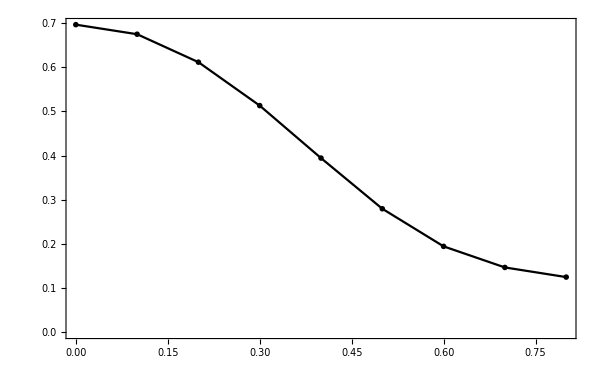

```mathematica
Module[{p0,p,l},p0=1;p=1;l=1;    enV0pure={};enV4pure={};enVΔpure={};
Do[Module[{jG0,LG0,χ0,ω0,ξ0,EnG0,χ,ω,ξ,jG,LG,EnG ,gauge="g4", 
Jv,Kv,Γv,J,K,Γ,L,Nc,h ,u0,H,enH,T,u,t,t0,c11,c21,c12,c22,sNN,sNNN,δn,tp,hp,λ1,λ2,Heff,Jmod,Kmod,Γmod}, 		 
	tp=⌈p/(Length@hV)⌉;hp=Mod[p,Length@hV,1];
	(*{J,K,Γ,h}=parameters⟦ev,p⟧[[1;;4]];*)    L=Ls⟦l⟧; Nc=L^2;
	{jG0,LG0,χ0,ω0,ξ0,EnG0}=Chop@loadDataPure[toPathPure800[parametersMat[[ev,p0]],L,acuracy, "g0",NbName ]  ]; 
	{jG,LG,χ,ω,ξ,EnG}=Chop@loadDataPure[toPathPure800[parametersMat[[ev,p0]],L,acuracy, "g4",NbName ]  ];  

AppendTo[enV0pure,{eVs[[ev]]/(U-3JH),EnG0[[-1]]}  ];
AppendTo[enV4pure,{eVs[[ev]]/(U-3JH),EnG[[-1]]}  ];
AppendTo[enVΔpure,{eVs[[ev]]/(U-3JH), L^2(EnG[[-1]]-EnG0[[-1]])}  ];           
]; ,{ev,1, Length@eVs}]; 

Module[ {En, Disp,h0,θ,φ,L, Nc,J,K,Γ, h ,η, χ0,ω0 ,title, color, j0, L0,tp,hp,size,plotInset,Jmat,JmatMod},
{h0,θ,φ}=ToString/@(NumberForm[#,2]&/@hV[[ 1]]);size=0.012; 
{Jmat,h}=parametersMat[[1,p]][[1;;2]]; {JmatMod,hv}=parametersMat[[1,p]][[3;;4]];
(*title=StringReplace[" a ",{"X1"-> ToString[J],"X2"-> ToString[K],"X3"-> ToString[Γ] ,"X4"-> ToString[Norm@h]  }] ;*)
title=
StringReplace["J\\!=\\!X1, \\; \\Gamma\\!=\\!X3, \\; \\mathbf{h}=Y1",{"X1"->ToString@NumberForm[J,{2,2}],"X2"->ToString@NumberForm[K,{2,2}],"X3"->ToString@NumberForm[Γ,{2,2}], "Y1"->StringJoin@{  "(",h0,",",θ,",",φ,")" }   }      ];

 ListPlot[ enVΔpure, Joined->True ,(*  PlotRange-> {-1.635,-1.6175} ,*)FrameLabel->{MaTeX["\\xi",Magnification->1] , MaTeX["E_{4\\textrm{v}\\!}\\!-\\!E_{0\\textrm{v}}",Magnification->1.2] }, Frame->True ,  ImageSize->600,  FrameStyle ->Directive[Black,14], PlotMarkers->"OpenMarkers",FrameTicksStyle->Directive[Black,12], PlotStyle->  {{ Black,PointSize[2*size]}    } ]
]  ]
```

#### more

```mathematica
ListPlot[ {enV0pure,enV4pure}, Joined->True ,FrameLabel->{MaTeX["\\xi=eV_0/(U-3J_H)",Magnification->1.4] , MaTeX["E_{4\\textrm{v}\\!} , \\; E_{0\\textrm{v}}",Magnification->1.5] }, Frame->True ,  ImageSize->600,  FrameStyle ->Directive[Black,14], PlotMarkers->"OpenMarkers",FrameTicksStyle->Directive[Black,12], PlotStyle->  {{Darker@ Green,PointSize[0.05]},{ Darker@Blue,PointSize[0.05]}    } ]
```

```mathematica
ListPlot[ {enVΔpure}, Joined->True ,(*  PlotRange-> {-1.635,-1.6175}, *)FrameLabel->{MaTeX["\\xi=eV_0/(U-3J_H)",Magnification->1.4] , MaTeX["E_{4\\textrm{v}\\!}\\!-\\!E_{0\\textrm{v}}",Magnification->1.5] }, Frame->True ,  ImageSize->600,  FrameStyle ->Directive[Black,14], PlotMarkers->"OpenMarkers",FrameTicksStyle->Directive[Black,12], PlotStyle->  {{ Black,PointSize[0.05]},{ Darker@Red,PointSize[0.05]}    } ]
```

```mathematica
Module[{p0,p,l},p0=1;p=1;l=1;   enV02pure={};enV42pure={};enVΔpure2={}; enVΔ2pure={};enMZM0={};enMZM={}; dispMZM0={};dispMZM={};
Do[Module[{jG0,LG0,χ0,ω0,ξ0,EnG0,χ,ω,ξ,jG,LG,EnG ,gauge="g4", 
Jv,Kv,Γv,J,K,Γ,L,Nc,h ,u0,H,enH,T,u,t,t0,c11,c21,c12,c22,sNN,sNNN,δn,tp,hp,λ1,λ2,Heff,Jmod,Kmod,Γmod,en0,en}, 		 
	tp=⌈p/(Length@hV)⌉;hp=Mod[p,Length@hV,1];
	{J,K,Γ,h}=parameters⟦ev,p⟧[[1;;4]];L=Ls⟦l⟧; Nc=L^2;
	{jG0,LG0,χ0,ω0,ξ0,EnG0}=Chop@loadDataPure[toPathPure[parameters[[ev,p0]],L,acuracy, "g0" ,NbName]  ]; 
          ω0=Table[ωGA,2,{r,1,Nc} ];
          ξ0=Table[0 ωGA,2,3,{r,1,Nc} ];
	{jG,LG,χ,ω,ξ,EnG}=Chop@loadDataPure[toPathPure[parameters[[ev,p0]],L,acuracy, "g4" ,NbName]  ];  
          ω=Table[ωGA,2,{r,1,Nc} ];
          ξ=Table[0 ωGA,2,3,{r,1,Nc} ];

 {J,K,Γ,h,Jmod,Kmod,Γmod}=parameters[[ev,p]][[1;;7]]; 

Kv=uniform[K,L,L];Kv=add4VorticesMaxSpaced[ Kv,Kmod,L];
Jv=uniform[0,L,L];
Γv=uniform[0,L,L];
en0=EnMF[Jv,Kv,Γv,h,χ0,ω0,L,L]; 
en=EnMF[Jv,Kv,Γv,h,χ,ω,L,L];
AppendTo[enVΔpure2,{eVs[[ev]]/(U-3JH), L^2(en-en0)}  ];      

Jv=uniform[J,L,L];Jv=add4VorticesMaxSpaced[ Jv,Jmod,L];
Γv=uniform[Γ,L,L];Γv=add4VorticesMaxSpaced[ Γv,Γmod,L];
en0=EnMF[Jv,Kv,Γv,h,χ0,ω0,L,L]; 
en=EnMF[Jv,Kv,Γv,h,χ,ω,L,L];

AppendTo[enV02pure,{eVs[[ev]]/(U-3JH),en0}  ];
AppendTo[enV42pure,{eVs[[ev]]/(U-3JH),en}  ];
AppendTo[enVΔ2pure,{eVs[[ev]]/(U-3JH), L^2(en-en0)}  ];           
           
]; ,{ev,1, Length@eVs}]; 

Module[ {En, Disp,h0,θ,φ,L, Nc,J,K,Γ, h ,η, χ0,ω0 ,title, color, j0, L0,tp,hp,size,plotInset},
{h0,θ,φ}=ToString/@(NumberForm[#,2]&/@hV[[ 1]]);
size=0.012;
tp=⌈p/(Length@hV)⌉;hp=Mod[p,Length@hV,1];
{J,K,Γ,h}=parameters⟦1,p⟧[[1;;4]];L=Ls⟦l⟧; Nc=L^2;
(*title=StringReplace[" a ",{"X1"-> ToString[J],"X2"-> ToString[K],"X3"-> ToString[Γ] ,"X4"-> ToString[Norm@h]  }] ;*)
title=
StringReplace["J\\!=\\!X1, \\; \\Gamma\\!=\\!X3, \\; \\mathbf{h}=Y1",{"X1"->ToString@NumberForm[J,{2,2}],"X2"->ToString@NumberForm[K,{2,2}],"X3"->ToString@NumberForm[Γ,{2,2}], "Y1"->StringJoin@{  "(",h0,",",θ,",",φ,")" }   }      ];

plotInset= ListPlot[ enVΔ2pure, Joined->True ,(*  PlotRange-> {-1.635,-1.6175} ,*)FrameLabel->{MaTeX["\\xi",Magnification->1] , MaTeX["E_{4\\textrm{v}\\!}\\!-\\!E_{0\\textrm{v}}",Magnification->1.2] }, Frame->True ,  ImageSize->600,  FrameStyle ->Directive[Black,14], PlotMarkers->"OpenMarkers",FrameTicksStyle->Directive[Black,12], PlotStyle->  {{ Black,PointSize[2*size]}    } ]; 
]  ]
```

```mathematica
ListPlot[ {enV02pure,enV42pure}, Joined->True ,FrameLabel->{MaTeX["\\xi=eV_0/(U-3J_H)",Magnification->1.4] , MaTeX["E_{4\\textrm{v}\\!} , \\; E_{0\\textrm{v}}",Magnification->1.5] }, Frame->True ,  ImageSize->600,  FrameStyle ->Directive[Black,14], PlotMarkers->"OpenMarkers",FrameTicksStyle->Directive[Black,12], PlotStyle->  {{Darker@ Green,PointSize[0.05]},{ Darker@Blue,PointSize[0.05]}    } ]
```

```mathematica
plotInset= ListPlot[ {enVΔpure2,enVΔ2pure}, Joined->True ,(*  PlotRange-> {-1.635,-1.6175}, *)FrameLabel->{MaTeX["\\xi=eV_0/(U-3J_H)",Magnification->1.4] , MaTeX["E_{4\\textrm{v}\\!}\\!-\\!E_{0\\textrm{v}}",Magnification->1.5] }, Frame->True ,  ImageSize->600,  FrameStyle ->Directive[Black,14], PlotMarkers->"OpenMarkers",FrameTicksStyle->Directive[Black,12], PlotStyle->  {{ Black,PointSize[0.05]},{ Darker@Red,PointSize[0.05]}    } ]
```

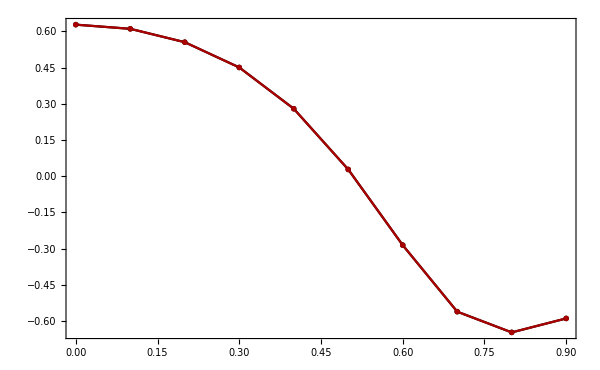
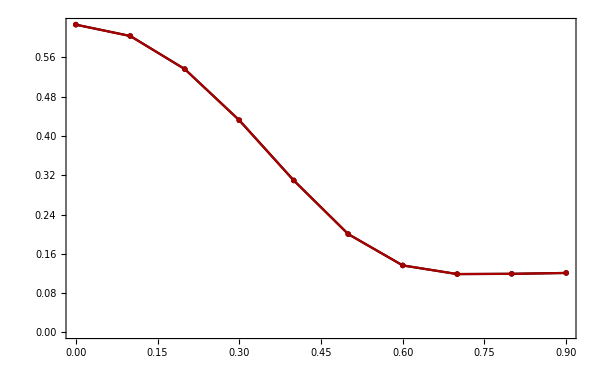

### MF

```mathematica
Module[{Np=Length@parametersMat[[1]],l=1},
enV0=Table[{},Np]; enV4=Table[{},Np];enVΔ=Table[{},Np];enVΔ1=Table[{},Np];enVΔ2=Table[{},Np];
Do[Module[{JmatMod,Jmat,jG0,LG0,χ0,ω0,ξ0,EnG0,χ,ω,ξ,jG,LG,EnG ,L,Nc,h ,u0,H,enH,T,u,t,t0,sNN,sNNN,δn,tp,hp,p}, 		 
p=Length[hV](pt-1)+ph;      L=Ls⟦l⟧;    Nc=L^2; T=Tmat[L,L]; 

{Jmat,h}=parametersMat[[ev,p]][[1;;2]]; {JmatMod,hv}=parametersMat[[ev,p]][[3;;4]];
          Print["JmatMod ",fromJmat[JmatMod],"; L=",L,"; h=(", hV[[ ph,1 ]],",",hV[[ ph,2 ]],",",hV[[ ph,3]],"); "];
	(*{jG0,LG0,χ0,ω0,ξ0,EnG0}*)
EnG0=loadData[toPath800[parametersMat[[ev,p]],L,acuracy, "g0",NbName ]  ][[6]];  
EnG=  loadData[toPath800[parametersMat[[ev,p]],L,acuracy, "g4",NbName ]   ][[6]];  

AppendTo[enV0[[p]],{eVs[[ev]],EnG0[[;;,-1,2]]}  ];
AppendTo[enV4[[p]],{eVs[[ev]],EnG[[;;,-1,2]]}  ];
AppendTo[enVΔ[[p]],{eVs[[ev]]/(U-3JH), 2L^2(EnG[[3,-1,2]]-EnG0[[3,-1,2]])}  ];           
AppendTo[enVΔ1[[p]],{eVs[[ev]]/(U-3JH),2 L^2(EnG[[1,-1,2]]-EnG0[[1,-1,2]])}  ];    
AppendTo[enVΔ2[[p]],{eVs[[ev]]/(U-3JH), 2L^2(EnG[[2,-1,2]]-EnG0[[2,-1,2]])}  ];           
]; ,{ev,1,Length[parametersMat]} , {pt,1,Length@tV},  {ph,1,Length@hV} ]; 
]
```

JmatMod {0.,-1.,0.,0.,0.}; L=16; h=(0.1,0,0);

JmatMod {0.,-1.02316,0.,0.,0.0511578}; L=16; h=(0.1,0,0);

JmatMod {0.,-1.09642,0.,0.,0.109642}; L=16; h=(0.1,0,0);

JmatMod {0.,-1.23261,0.,0.,0.184891}; L=16; h=(0.1,0,0);

JmatMod {0.,-1.45877,0.,0.,0.291755}; L=16; h=(0.1,0,0);

JmatMod {0.,-1.82959,0.,0.,0.457398}; L=16; h=(0.1,0,0);

JmatMod {0.,-2.46258,0.,0.,0.738775}; L=16; h=(0.1,0,0);

JmatMod {0.,-3.64728,0.,0.,1.27655}; L=16; h=(0.1,0,0);

JmatMod {0.,-6.29158,0.,0.,2.51663}; L=16; h=(0.1,0,0);

```mathematica
Module[{Np=Length@parametersMat[[1]],l=1},
en2V0=Table[{},Np]; en2V4=Table[{},Np];
en2VΔ=Table[{},Np];en2VΔ1=Table[{},Np];en2VΔ2=Table[{},Np];
Do[Module[{JmatMod,Jmat,jG0,LG0,χ0,ω0,ξ0,EnG0,χ,ω,ξ,jG,LG,EnG ,L,Nc,h ,u0,H,enH,T,u,t,t0,sNN,sNNN,δn,tp,hp,p}, 		 
p=Length[hV](pt-1)+ph;      L=Ls⟦l⟧;    Nc=L^2; T=Tmat[L,L]; 

{Jmat,h}=parametersMat[[ev,p]][[1;;2]]; {JmatMod,hv}=parametersMat[[ev,p]][[3;;4]];
          Print["JmatMod ",fromJmat[JmatMod],"; L=",L,"; h=(", hV[[ ph,1 ]],",",hV[[ ph,2 ]],",",hV[[ ph,3]],"); "];
	(*{jG0,LG0,χ0,ω0,ξ0,EnG0}*)
EnG0=loadData[toPath800[parametersMat[[ev,p]],L,acuracy, "g0",NbName ]  ][[6]];  
EnG=  loadData[toPath800[parametersMat[[ev,p]],L,acuracy, "g4",NbName ]   ][[6]];  

AppendTo[en2V0[[p]],{eVs[[ev]],EnG0[[;;,-1,2]]}  ];
AppendTo[en2V4[[p]],{eVs[[ev]],EnG[[;;,-1,2]]}  ];
AppendTo[en2VΔ[[p]],{eVs[[ev]]/(U-3JH), 2L^2(EnG[[3,-1,2]]-EnG0[[3,-1,2]])}  ];           
AppendTo[en2VΔ1[[p]],{eVs[[ev]]/(U-3JH),2 L^2(EnG[[1,-1,2]]-EnG0[[1,-1,2]])}  ];    
AppendTo[en2VΔ2[[p]],{eVs[[ev]]/(U-3JH), 2L^2(EnG[[2,-1,2]]-EnG0[[2,-1,2]])}  ];           
]; ,{ev,1,Length[parametersMat]} , {pt,1,Length@tV},  {ph,1,Length@hV} ]; 
]
```

JmatMod {0.,-1.,0.,0.,0.}; L=16; h=(0.1,0,0);

JmatMod {0.,-1.02316,0.,0.,0.102316}; L=16; h=(0.1,0,0);

JmatMod {0.,-1.09642,0.,0.,0.219285}; L=16; h=(0.1,0,0);

JmatMod {0.,-1.23261,0.,0.,0.369782}; L=16; h=(0.1,0,0);

JmatMod {0.,-1.45877,0.,0.,0.58351}; L=16; h=(0.1,0,0);

JmatMod {0.,-1.82959,0.,0.,0.914797}; L=16; h=(0.1,0,0);

JmatMod {0.,-2.46258,0.,0.,1.47755}; L=16; h=(0.1,0,0);

JmatMod {0.,-3.64728,0.,0.,2.5531}; L=16; h=(0.1,0,0);

JmatMod {0.,-6.29158,0.,0.,5.03326}; L=16; h=(0.1,0,0);

```mathematica
(*Module[{J,K,Γ,Γp,DM,h,ev=1,p=1,L,l=1,title,h0,θ,φ,Jmat},
{Jmat,h}=parametersMat[[ev,p]][[1;;2]]; (*{JmatMod,hv}=parametersMat[[ev,p]][[3;;4]];*)
{J,K,Γ,Γp,DM}=fromJmat[Jmat];L=Ls[[l]];
{h0,θ,φ}=ToString/@parametersMat⟦ev,p⟧[[4]];
title=StringReplace["J\\!=\\!X1, \\; \\Gamma\\!=\\!X3, \\; \\mathbf{h}=Y1, \\; L=Y2",{"X1"->ToString@NumberForm[J,{2,2}],"X2"->ToString@NumberForm[K,{2,2}],"X3"->ToString@NumberForm[Γ,{2,2}],"Y2"-> ToString[L], "Y1"->StringJoin@{  "(",h0,",",θ,",",φ,")" }   }      ];

ListPlot[   {enVΔpure,enVΔ[[1]]}   , Joined->True ,  PlotRange-> {{0,1},{-.25,.75}},FrameLabel->{MaTeX["\\xi=eV_0/(U-3J_H)",Magnification->1.4] , MaTeX["E_{4\\textrm{v}\\!}\\!-\\!E_{0\\textrm{v}}",Magnification->1.5] }, Frame->True ,  ImageSize->600,
PlotLegends-> Placed[ MaTeX[#,Magnification->1.4]&/@{"\\Delta E_{\\text{pure K}}","\\Delta \\left< H_{\\text{MF} }\\right>_{0}","\\Delta\\big(-\\sum_{n}\\varepsilon_n\\big)"  } , {Scaled[{0.01,.008}], Scaled[{0,0}]}  ]   , PlotLabel->MaTeX[ title,Magnification->1.4]  ,  FrameStyle ->Directive[Black,14], PlotMarkers->"OpenMarkers",FrameTicksStyle->Directive[Black,12], PlotStyle->  {{ Darker@Orange,PointSize[0.05]} ,{ Darker@Blue,PointSize[0.05]},{ Darker@Red,PointSize[0.05]},{ Hue[0.5,0.5,0,0.5],PointSize[0.05]}    } ]
]*)
```

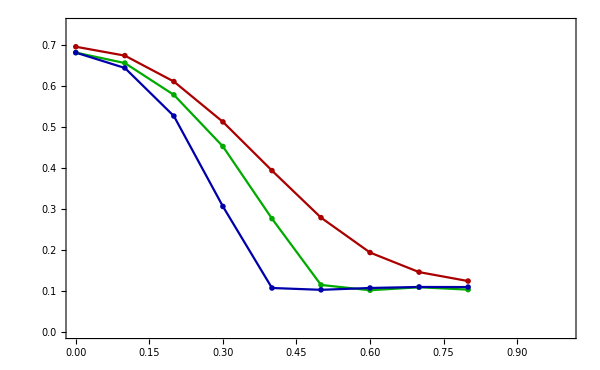

```mathematica
Module[{J,K,Γ,Γp,DM,h,ev=1,p=1,L,l=1,title,h0,θ,φ,Jmat},
{Jmat,h}=parametersMat[[ev,p]][[1;;2]]; (*{JmatMod,hv}=parametersMat[[ev,p]][[3;;4]];*)
{J,K,Γ,Γp,DM}=fromJmat[Jmat];L=Ls[[l]];
{h0,θ,φ}=ToString/@parametersMat⟦ev,p⟧[[4]];
title=StringReplace["\\mathbf{h}=Y1, \\; L=Y2",{"X1"->ToString@NumberForm[J,{2,2}],"X2"->ToString@NumberForm[K,{2,2}],"X3"->ToString@NumberForm[Γ,{2,2}],"Y2"-> ToString[L], "Y1"->StringJoin@{  "(",h0,",",θ,",",φ,")" }   }      ];

ListPlot[   {enVΔpure,enVΔ[[1]],en2VΔ[[1]]}   , Joined->True ,  PlotRange-> {{0,1},{0,.75}},FrameLabel->{MaTeX["\\xi=eV_0/(U-3J_H)",Magnification->1.4] , MaTeX["E_{4\\textrm{v}\\!}\\!-\\!E_{0\\textrm{v}}",Magnification->1.5] }, Frame->True ,  ImageSize->600,
PlotLegends-> Placed[ MaTeX[#,Magnification->1.4]&/@{"\\Gamma=0.0, \\; \\mathrm{D}(\\xi)=0","\\Gamma=0.0, \\; \\mathrm{D}(1)=0.1","\\Gamma=0.0, \\; \\mathrm{D}(1)=0.5"  } , {Scaled[{0.01,.008}], Scaled[{0,0}]}  ]   , PlotLabel->MaTeX[ title,Magnification->1.4]  ,  FrameStyle ->Directive[Black,14], PlotMarkers->"OpenMarkers",FrameTicksStyle->Directive[Black,12], PlotStyle->  {{ Darker@Red,PointSize[0.05]} ,{ Darker@Green,PointSize[0.05]},{ Darker@Blue,PointSize[0.05]},{ Hue[0.5,0.5,0,0.5],PointSize[0.05]}    } ]
]
```

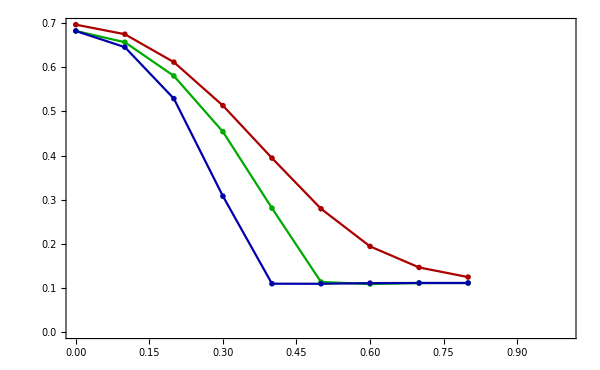

```mathematica
Module[{J,K,Γ,Γp,DM,h,ev=1,p=1,L,l=1,title,h0,θ,φ,Jmat},
{Jmat,h}=parametersMat[[ev,p]][[1;;2]]; (*{JmatMod,hv}=parametersMat[[ev,p]][[3;;4]];*)
{J,K,Γ,Γp,DM}=fromJmat[Jmat];L=Ls[[l]];
{h0,θ,φ}=ToString/@parametersMat⟦ev,p⟧[[4]];
title=StringReplace["\\mathbf{h}=Y1, \\; L=Y2",{"X1"->ToString@NumberForm[J,{2,2}],"X2"->ToString@NumberForm[K,{2,2}],"X3"->ToString@NumberForm[Γ,{2,2}],"Y2"-> ToString[L], "Y1"->StringJoin@{  "(",h0,",",θ,",",φ,")" }   }      ];

ListPlot[   {enVΔpure,enVΔ2[[1]],en2VΔ2[[1]]}   , Joined->True ,  PlotRange-> {{0,1},Full},FrameLabel->{MaTeX["\\xi=eV_0/(U-3J_H)",Magnification->1.4] , MaTeX["E_{4\\textrm{v}\\!}\\!-\\!E_{0\\textrm{v}}",Magnification->1.5] }, Frame->True ,  ImageSize->600,
PlotLegends-> Placed[ MaTeX[#,Magnification->1.4]&/@{"\\Gamma=0, \\; \\mathrm{D}(\\xi)=0","\\Gamma=0.0, \\; \\mathrm{D}(1)=0.5","\\Gamma=0.0, \\; \\mathrm{D}(1)=1"  } , {Scaled[{0.01,.008}], Scaled[{0,0}]}  ]   , PlotLabel->MaTeX[ title,Magnification->1.4]  ,  FrameStyle ->Directive[Black,14], PlotMarkers->"OpenMarkers",FrameTicksStyle->Directive[Black,12], PlotStyle->  {{ Darker@Red,PointSize[0.05]} ,{ Darker@Green,PointSize[0.05]},{ Darker@Blue,PointSize[0.05]},{ Hue[0.5,0.5,0,0.5],PointSize[0.05]}    } ]
]
```

```mathematica
(*Module[{J,K,Γ,Γp,DM,h,p=1,ev=1, Np,L,l=1,title,h0,θ,φ,legends,Jmat},
{Jmat,h}=parametersMat[[ev,p]][[1;;2]]; (*{JmatMod,hv}=parametersMat[[ev,p]][[3;;4]];*)
{J,K,Γ,Γp,DM}=fromJmat[Jmat];L=Ls[[l]]; {h0,θ,φ}=ToString/@parametersMat⟦ev,p⟧[[4]]; Np=Length@parametersMat[[1]]; 
J=Table[0,Np];K=Table[0,Np];Γ=Table[0,Np];Γp=Table[0,Np];DM=Table[0,Np];

Do[   {J[[p]],K[[p]],Γ[[p]],Γp[[p]],DM[[p]] }=fromJmat[  parametersMat⟦ev,p⟧[[1]]  ]   ,{p,1,Np}]; L=Ls[[l]];
{h0,θ,φ}=ToString/@parametersMat⟦ev,1⟧[[4]];

title=StringReplace[" \\mathbf{h}=Y1, \\; L=Y2",{"X1"->ToString@NumberForm[J,{2,2}],"X2"->ToString@NumberForm[K,{2,2}],"X3"->ToString@NumberForm[Γ,{2,2}],"Y2"-> ToString[L], "Y1"->StringJoin@{  "(",h0,",",θ,",",φ,")" }   }      ];
legends=Table[
StringReplace["\\Gamma(0) \\!=\\!X3, \\mathrm{D}(1) \\!=\\! 0.5",{"X1"->ToString@NumberForm[J[[p]],{2,2}],"X2"->ToString@NumberForm[K[[p]],{2,2}],"X3"->ToString@NumberForm[Γ[[p]],{2,2}]  }      ], {p,1,Np}];

ListPlot[ enVΔ2, Joined->True ,  PlotRange-> {{0,1},{-.18,.75}},FrameLabel->{MaTeX["\\xi=eV_0/(U-3J_H)",Magnification->1.4] , MaTeX["E_{4\\textrm{v}\\!}\\!-\\!E_{0\\textrm{v}}",Magnification->1.5] }, Frame->True ,  ImageSize->600,
PlotLegends-> Placed[ MaTeX[#,Magnification->1.2]&/@legends , {Scaled[{0.01,.008}], Scaled[{0,0}]}  ]   , PlotLabel->MaTeX[ title,Magnification->1.4]  ,  FrameStyle ->Directive[Black,14], PlotMarkers->"OpenMarkers",FrameTicksStyle->Directive[Black,12] (*, PlotStyle->  {{ Darker@Blue,PointSize[0.05]},{ Black,PointSize[0.05]},{ Darker@Red,PointSize[0.05]}    }*)  ]
]*)
```

## To do:

× Change W -> V                                                                                              done
× define mf energy   (via <> and eigenvalue)                                done
×     test  it for pure Kitaev h=0                                                                  done
× Wilson loop  ( change order r and σ )                                                done
× function Jmicro[t] output Jmat coupling for each t                  done
× Change def parameters  (define DM as function of eV)             done
× Define DM interaction as uniform 0 + 4v                                          done
× Rewrite code for vortex free  (for 4v  then copy it making the trivial changes)